# 三体微分截面与天然氙事件率（矢量-矢量耦合）

## 计算路线与运行顺序

阅读与运行：先设置第一节物理量与第二节积分设置，再按顺序运行至 4.6.1 查看固定速度单核素结果；固定速度曲线、总截面和事件率是多层数值积分，可能耗时很长。最后的模型验证状态表需在相关检查运行后重新执行。修改输入、模型或积分设置后，从头依次重算依赖它们的单元；旧输出不会自动更新。

检查点说明：1.4 节的速度仅用于固定速度单核素截面；默认 776 km/s 是当前地球系速率分布的上限，并不是平均速度。事件率对速度分布积分，并对各同位素按数目丰度求和。检查点未打开不代表该 benchmark 在其他反冲能量或核素中都没有贡献。

本笔记本先计算 vector-vector 模型：设置物理和 NIntegrate 精度参数，加载 FeynCalc 构造两张费米子链及自旋迹；Mathematica NIntegrate 对三体相空间和晕速度分布积分，再得到截面、天然氙事件率和图。后面用手写迹、Gauss 求积、FeynRules/FeynArts 等做对照。完整曲线是嵌套数值积分，耗时可能很长；修改输入后从头运行。

## 一、物理输入（先在这里修改数值）

本节按标注的单位输入。数值程序统一使用 GeV；单位换算集中在后面的宽度计算和求解步骤。

### 1.1 粒子质量与耦合

三个耦合均无量纲。数值由下面输入单元指定。核子耦合采用质子和中子相同的约定；原稿中普适夸克耦合 gVq=gVN/3，因此由 gVN 推出。

```mathematica
(* 暗物质 chi1 和矢量媒介 V 的质量，单位 GeV。 *)
darkMatterMassGeV = 1000.;  (* 输入暗物质 chi1 质量，单位 GeV *)
mediatorMassGeV = 10.;  (* 输入矢量媒介质量，单位 GeV *)

(* 暗费米子与矢量媒介的非对角耦合。 *)
g1val = 1.0;  (* 设置暗物质与矢量媒介的耦合 g1 *)

(* 暗费米子与标量 s 的非对角耦合。 *)
g2val = 1.0;  (* 设置暗物质与标量的耦合 g2，同时影响极点宽度 *)

(* 矢量媒介与单个核子的耦合，取质子与中子相同。 *)
gVNval = 1.0;  (* 设置矢量媒介与核子的耦合 *)

(* 原稿的普适夸克耦合和截面前因子均由上述输入推导。 *)
gVqval = gVNval/3;  (* 按当前核子与夸克耦合约定计算夸克耦合 *)
couplingProductSquared = Abs[g1val * g2val * gVNval]^2;  (* 计算三个耦合乘积的模平方 *)

Print["gVq = ", gVqval];  (* 显示当前说明或计算结果 *)
Print["|g1 g2 gVN|^2 = ", couplingProductSquared];  (* 显示当前说明或计算结果 *)
```

gVq = 0.333333

|g1 g2 gVN|^2 = 1.

### 1.2 四组质量组合

Figure 2 的标量质量 m_s 单位采用 keV（由用户明确确认）；下表每一行的第二个数是质量劈裂 Delta m，单位仍为 MeV。若原图中出现其他标注，以本处确认的物理输入为准。

每行依次填写标量质量 ms（keV）和暗费米子质量劈裂 Δm（MeV）。宽度表、事件率和图例均读取这张表。第三、四行的 keV 输入沿用对原图图例的条件性解释。

```mathematica
benchmarks = {  (* 设置每组标量质量 keV 与质量劈裂 MeV *)
  {200.,  1.},   (* 第 1 组 *)  (* 设置一组标量质量 keV 与质量劈裂 MeV *)
  {300.,  1.},   (* 第 2 组 *)  (* 设置一组标量质量 keV 与质量劈裂 MeV *)
  {360.,  1.},   (* 第 3 组 *)  (* 设置一组标量质量 keV 与质量劈裂 MeV *)
  {300., 10.}    (* 第 4 组 *)  (* 设置一组标量质量 keV 与质量劈裂 MeV *)
};  (* 结束当前参数列表、计算块或表达式 *)
Print["Benchmark 输入（每行是 ms [keV], Δm [MeV]）：", benchmarks];
```

Benchmark 输入（每行是 ms [keV], Δm [MeV]）：{{200.,1.},{300.,1.},{360.,1.},{300.,10.}}

### 1.3 暗物质晕与氙靶

```mathematica
(* 局域暗物质密度，单位 GeV/cm.b3。 *)
localDensityGeVPerCm3 = 0.3;  (* 设置局域暗物质密度 GeV/cm.b3 *)

(* 晕速度尺度、地球速度及逃逸速度，单位 km/s。 *)
haloSpeedScaleKmPerS = 220.;  (* 设置晕速度尺度 km/s *)
earthSpeedKmPerS = 232.;  (* 设置地球相对晕速度 km/s *)
escapeSpeedKmPerS = 544.;  (* 设置逃逸速度截断 km/s *)

(* 天然氙摩尔质量，单位 g/mol。每个箭头右侧是数目丰度。 *)
xenonMolarMassGPerMol = 131.293;  (* 设置天然氙平均摩尔质量 g/mol *)
abundances = <|  (* 按质量数记录天然氙同位素数目丰度 *)
  128 -> 0.019102,  (* 设置 Xe-128 的天然数目丰度 *)
  129 -> 0.264006,  (* 设置 Xe-129 的天然数目丰度 *)
  130 -> 0.040710,  (* 设置 Xe-130 的天然数目丰度 *)
  131 -> 0.212324,  (* 设置 Xe-131 的天然数目丰度 *)
  132 -> 0.269086,  (* 设置 Xe-132 的天然数目丰度 *)
  134 -> 0.104357,  (* 设置 Xe-134 的天然数目丰度 *)
  136 -> 0.088573  (* 设置 Xe-136 的天然数目丰度 *)
|>;  (* 接续上一行的参数或表达式 *)
isotopes = Keys[abundances];  (* 从丰度表提取参与计算的同位素 *)
Print["局域密度 GeV/cm.b3：",localDensityGeVPerCm3,"；速度 v0、vEarth、vEsc (km/s)：",{haloSpeedScaleKmPerS,earthSpeedKmPerS,escapeSpeedKmPerS}];
Print["氙同位素数目丰度：",abundances,"；丰度总和：",Total[Values[abundances]]];
```

局域密度 GeV/cm.b3：0.3；速度 v0、vEarth、vEsc (km/s)：{220.,232.,544.}

氙同位素数目丰度：<|128→0.019102,129→0.264006,130→0.04071,131→0.212324,132→0.269086,134→0.104357,136→0.088573|>；丰度总和：0.998158

### 1.4 固定速度微分截面的检查点

先指定同位素、质量组合、反冲能量和入射速度。运行下面的截面计算后，可以逐项检查核响应、三体积分、前因子和最终截面。

```mathematica
(* 固定速度微分截面的示例输入。 *)
diagnosticIsotope = 131;             (* 氙同位素的质量数 A *)  (* 选择单核截面的同位素质量数 *)
diagnosticBenchmarkIndex = 2;       (* 选用 1.2 节中的第几组 ms、Delta m *)  (* 选择质量组合序号 *)
diagnosticRecoilKeV = 200.;          (* 核反冲能量 ER，单位 keV *)  (* 设置检查用反冲能量 keV *)
diagnosticSpeedKmPerS = 776.;       (* 入射暗物质速度，单位 km/s *)  (* 设置检查用入射速度 km/s *)
diagnosticWidthMode = "pole";  (* 固定采用当前模型的极点宽度 *)
```

## 二、数值设置

```mathematica
(* 三体相空间积分：phaseSpaceOrders 这个历史变量名现在保存 NIntegrate 设置。 *)
phaseSpaceOrders=<|
 "AccuracyGoal"->3,     (* 绝对误差精度目标 *)
 "PrecisionGoal"->3,    (* 相对误差精度目标 *)
 "WorkingPrecision"->30,(* 计算使用的数字精度；不能增加输入本身的有效数字 *)
 "MaxRecursion"->6      (* 自适应细分的最大递归次数 *)
|>;
(* 实验室速度积分；Infinity 表示主要控制相对精度。 *)
speedOrder=<|
 "AccuracyGoal"->Infinity, (* 不使用有限的绝对误差目标 *)
 "PrecisionGoal"->3,       (* 速度积分相对误差目标 *)
 "MaxRecursion"->5         (* 速度积分最大递归次数 *)
|>;
(* 这些参数只用于末尾 Gauss 对照。 *)
gaussCheckOrders={6,6,4};
(* 反冲能量网格及代表点，单位 keV。 *)
recoilMinKeV=10.;       (* 能量网格下限 *)
recoilMaxKeV=800.;      (* 能量网格上限 *)
recoilStepKeV=10.;      (* 能量网格步长 *)
extraRecoilEnergiesKeV={101.,267.,542.}; (* 附加网格点 *)
comparisonEnergiesKeV={200.,300.,542.};  (* 输出结果的代表能量 *)
convergenceBenchmarkIndex=2; (* 收敛检查所选质量组合 *)
convergenceRecoilKeV=200.;   (* 收敛检查反冲能量，keV *)
(* 收敛检查采用更严格的精度目标。 *)
finePhaseSpaceOrders=<|"AccuracyGoal"->5,"PrecisionGoal"->5,"WorkingPrecision"->40,"MaxRecursion"->9|>;
fineSpeedOrder=<|"AccuracyGoal"->Infinity,"PrecisionGoal"->5,"MaxRecursion"->8|>;
Print["三体 NIntegrate 设置：",phaseSpaceOrders];
Print["速度 NIntegrate 设置：",speedOrder];
Print["反冲能量网格 (最小, 最大, 步长) keV：",{recoilMinKeV,recoilMaxKeV,recoilStepKeV}];
```

三体 NIntegrate 设置：<|AccuracyGoal→3,PrecisionGoal→3,WorkingPrecision→30,MaxRecursion→6|>

速度 NIntegrate 设置：<|AccuracyGoal→∞,PrecisionGoal→3,MaxRecursion→5|>

反冲能量网格 (最小, 最大, 步长) keV：{10.,800.,10.}

## 三、加载 FeynCalc（主计算必需）

在本单元按 Shift+Enter。程序先查找本机 FeynCalc，再加载并显示成功信息；如找不到，会输出明确提示。首次加载可能需要几十秒。

```mathematica
(* 第一步：检查本机是否能找到 FeynCalc。 *)
feynCalcPath = FindFile["FeynCalc`"];  (* 查找本机 FeynCalc 安装路径 *)
Print["FeynCalc 路径：", feynCalcPath];  (* 显示当前说明或计算结果 *)

(* 第二步：加载 FeynCalc。 *)
If[feynCalcPath === $Failed,  (* 判断条件，根据结果执行相应分支 *)
  Print["未找到 FeynCalc，请先安装后重新运行本单元。"],  (* 显示当前说明或计算结果 *)
  Needs["FeynCalc`"];  (* 加载所需 Mathematica 软件包 *)
  Print["FeynCalc 已加载，可以继续主模型计算。"]  (* 显示当前说明或计算结果 *)
]  (* 结束当前参数列表、计算块或表达式 *)
```

FeynCalc 路径：C:\Users\local-user\AppData\Roaming\Wolfram\Applications\FeynCalc\Kernel\init.m

FeynCalc 已加载，可以继续主模型计算。

## 四、模型、振幅、核响应与微分截面

### 4.1 物理约定

这里把 chi1、chi2 当作 Dirac 费米子，把 s 当作实标量，并假设 chi2 → chi1 s 是唯一开放衰变道，因而用这一分宽作为总宽。mchi2=mchi1+Delta m，采用纯标量 Yukawa 耦合 g₂ s bar(chi2) chi1 + h.c.。如果实际粒子类型、顶点或其他衰变道不同，须重算宽度。

宽度公式为 Gamma = |g₂|.b2 sqrt(Delta m.b2-ms.b2) [(2 mchi1+Delta m).b2-ms.b2]^(3/2) / [16 pi (mchi1+Delta m).b3]；Delta m≤ms 时该衰变道关闭。masses 统一用 GeV；公式写成分解形式以降低数值消减。

遵循原稿的固定极点宽度方案：标量在交换之后发射的传播子分母使用 W.b2-mchi2.b2+i mchi2 Gamma，另一张图保持原稿中的无宽度形式；两图先相加再做自旋迹。程序仍要求 Wmax < mchi2，不将上壳区域当成普通离壳散射。该 Breit–Wigner 处方是固定宽度近似，不是完整动量依赖一圈费米子自能。

g₂ 同时进入截面前因子和 χ₂ 的极点宽度；所有散射和事件率使用该宽度。mV=10 GeV 是演示输入。

核反冲微分截面（原稿 radiative-recoil 公式）

(d σ_A)/(d E_R)=(m_A(g_1 g_2 g_VN)^2 ℛ_A(E_R))/(256 π^3 p_χ_1^2(m_V^2+2 m_A E_R)^2)
×∫_(W_min^2)^(W_max^2) d W^2 √(λ(W^2,m_χ_1^2,m_s^2)) ∫_-1^1 dz ⟨ℒ_00⟩_(φ_*)

式中 mA 是靶核质量，pχ₁ 是入射暗物质动量，ℛA 是相干核响应。λ 是原稿定义的无量纲相空间函数，W.b2 为 χ₁s 系统的不变质量平方，z 为标量发射极角余弦。角括号表示对方位角 φ* 取平均。程序 I6 计算两个显式积分及方位角平均，Rate 再乘截面前因子并做晕速度积分。

### 4.2 模型计算函数与 AFH 核响应

AFH 默认数据涵盖这里列出的七种同位素。丰度是天然数目份额，按输入值直接加权。

#### 计算函数准备

请从上到下运行本节，逐步定义计算函数。

```mathematica
(* 函数直接在笔记本中定义。 *)
```

#### 公开函数说明

列出用户可直接调用的函数和单位。

```mathematica
LoadResponses::usage="LoadResponses[path, isotopes] loads AFH and freezes a response for each isotope.";  (* 准备各同位素核响应 *)

I6::usage="I6[m,ms,dm,mA,er,v,options,width] computes the FeynCalc spin-weighted phase-space integral using NIntegrate; options is phaseSpaceOrders.";  (* 进行三体相空间积分 *)

Chi2Width::usage="Chi2Width[m,ms,dm,g2] computes the Dirac pure-scalar chi2 -> chi1 s pole partial width in GeV.";  (* 检查激发态传播子的适用条件 *)

NuclearResponse::usage="NuclearResponse[A, ERkeV] returns the normalized AFH response for an already loaded xenon isotope.";  (* 计算该反冲能量对应的核响应 *)

DifferentialCrossSection::usage="DifferentialCrossSection[A, ERkeV, speedKms, msGeV, deltaMGeV, parameters] returns d sigma/d ER in GeV^-3 at fixed speed.";  (* 说明此函数的用途、输入和输出；具体实现位于下方 *)

VMin::usage="VMin[m,ms,mA,er] is the threshold speed in km/s.";  (* 说明此函数的用途、输入和输出；具体实现位于下方 *)

SpeedPDF::usage="SpeedPDF[v,v0,ve,vesc] is the normalized truncated lab speed PDF.";  (* 使用实验室系速度分布 *)

Rate::usage="Rate[erKeV,ms,dm,parameters] returns events/(tonne year keV).";  (* 说明此函数的用途、输入和输出；具体实现位于下方 *)

MakeCurves::usage="MakeCurves[energies,benchmarks,parameters] evaluates every curve.";  (* 说明此函数的用途、输入和输出；具体实现位于下方 *)
```

#### 辅助函数准备

下面依次定义模型使用的辅助函数和计算函数。按顺序运行单元即可。

```mathematica
(* 函数直接在笔记本中定义。 *)
```

#### 常数、积分节点与四动量工具

建立单位换算、对照用 Gauss 节点、四矢量和 Dirac 矩阵。

```mathematica
cKm=299792.458;  (* 光速，单位 km/s，用于速度转成 v/c *)
 cCm=2.99792458*10^10;  (* 光速，单位 cm/s，用于粒子通量换算 *)
 GeV2cm2=0.3893793721*10^-27;  (* 将自然单位 GeV^-2 换算为 cm.b2 *)

(* GL weights from Jacobi matrix. The angular phi weights sum to one. *)
gl[n_Integer?Positive]:=gl[n]=Module[{b,vals,vec,order},
 b=Table[k/Sqrt[4. k^2-1.],{k,1,n-1}];  (* 生成 Gauss 积分节点和权重 *)

 {vals,vec}=Eigensystem[DiagonalMatrix[b,1]+DiagonalMatrix[b,-1]];  (* Jacobi 矩阵的本征值是 Gauss 节点，本征向量用于计算权重 *)

 order=Ordering[vals];  (* 按节点大小排序 *)
 Transpose[{vals[[order]],2 (vec[[order,1]])^2}]];  (* 返回有序的节点和对应权重 *)

mdot[a_,b_]:=a[[1]] b[[1]]-a[[2;;4]].b[[2;;4]];  (* 计算四矢量点积，度规取 (+,−,−,−) *)

boost[a_,beta_]:=Module[{b2=beta.beta,g,p},
 If[b2<10^-30,Return[a]];  (* 速度接近零时直接返回原四矢量 *)
 If[b2>=1,Throw["Invalid boost"]];  (* 超光速不是有效的洛伦兹变换，停止计算 *)

 g=1/Sqrt[1-b2];  (* 计算洛伦兹因子 γ *)
 p=a[[2;;4]].beta;  (* 计算四动量空间部分与变换速度的点积 *)

 Join[{g(a[[1]]+p)},a[[2;;4]]+(((g-1)p/b2)+g a[[1]]) beta]];  (* 输出洛伦兹变换后的四动量 *)

i2=IdentityMatrix[2];  (* 定义 2×2 单位矩阵 *)
z2=ConstantArray[0,{2,2}];  (* 定义 2×2 零矩阵 *)

s1={{0,1},{1,0}};  (* 定义第一泡利矩阵 σ1 *)
s2={{0,-I},{I,0}};  (* 定义第二泡利矩阵 σ2 *)
s3={{1,0},{0,-1}};  (* 定义第三泡利矩阵 σ3 *)

g0=ArrayFlatten[{{i2,z2},{z2,-i2}}];  (* 由泡利矩阵构造 γ0 *)

g1=ArrayFlatten[{{z2,s1},{-s1,z2}}];  (* 由泡利矩阵构造 γ1；不是耦合 g1val *)

g2=ArrayFlatten[{{z2,s2},{-s2,z2}}];  (* 由泡利矩阵构造 γ2；不是耦合 g2val *)

g3=ArrayFlatten[{{z2,s3},{-s3,z2}}];  (* 由泡利矩阵构造 γ3 *)
 id=IdentityMatrix[4];  (* 定义 4×4 单位矩阵 *)

slash[p_]:=g0 p[[1]]-g1 p[[2]]-g2 p[[3]]-g3 p[[4]];  (* 按正负负负度规定义 Dirac 斜杠 p̸ *)
```

#### 两张辐射图的振幅与自旋迹

计算标量在相互作用前后辐射的两项及其干涉；只保留核流时间分量。

```mathematica
trace[pin_,pp_,k_,m_,m2_,w2_,width_]:=Module[{d1,d2,gb,ga,g,bar},
 (* As in the manuscript: only the after-emission denominator has i m2 Gamma. *)
 d1=mdot[pin-k,pin-k]-m2^2;  (* 计算自旋平均的两图振幅平方 *)
d2=w2-m2^2+I m2 width;  (* 辐射后 χ2 传播子分母，含 i mχ2 Γχ2 *)

 If[Abs[d1]<10^-12 || Abs[d2]<10^-12,Throw["Propagator pole or invalid kinematics"]];  (* 若分母过小则停止，避免数值奇异 *)

 gb=g0.(slash[pin-k]+m2 id)/d1;  (* 构造辐射前的暗物质矩阵链及传播子 *)

 ga=(slash[pp+k]+m2 id).g0/d2;  (* 构造辐射后的暗物质矩阵链及传播子 *)

 g=gb+ga;  (* 相加两张费曼图的矩阵链，干涉项随后产生 *)
bar=g0.ConjugateTranspose[g].g0;  (* 构造两图总矩阵链的 Dirac 共轭 *)

 Re[Tr[(slash[pp]+m id).g.(slash[pin]+m id).bar]]/2];  (* 求两图相干振幅的自旋迹，并对初态自旋平均 *)
```

#### Gauss 对照代码移至最后的验证部分

Gauss 求积实现只作为后面的验证对照；主计算直接在 NIntegrate 部分定义 I6。为兼容独立子内核，旧源码另以隐藏程序单元保留。

I6[m_?NumericQ,ms_?NumericQ,dm_?NumericQ,mA_?NumericQ,er_?NumericQ,v_?NumericQ,order_List,width_?NumericQ]:=Module[
 {beta,lor,ee,pz,qq,wlo,whi,pin,quadrW,quadrZ,quadrP,sum=0.,w2,weight,cq,q,K,bK,ps,e3,ref,e1,e2,lam,W,kabs,Ek,Ep,z,phi,n,k,pp,ang,pa,m2},
 If[!NumericQ[width] || !TrueQ[width>=0],Throw["Invalid constant pole width"]];  (* 设置相空间积分节点 *)

 If[er<=0 || v<=0,Return[0.]];  (* 运动学不允许时返回零 *)

 beta=v/cKm;  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
lor=1/Sqrt[1-beta^2];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
ee=m lor;  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
pz=m lor beta;  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
qq=Sqrt[2 mA er+er^2];  (* 计算核反冲对应的四动量 *)

 wlo=(m+ms)^2;  (* 设置三体不变质量积分下限 *)
whi=m^2+2 pz qq-2(ee+mA)er;  (* 设置三体不变质量积分上限 *)

 If[whi<=wlo,Return[0.]];  (* 运动学不允许时返回零 *)

 m2=m+dm;  (* 计算激发态质量 *)

 If[whi>=m2^2,Throw["On-shell chi2 accessible: off-shell calculation aborted"]];  (* 检查激发态传播子的适用条件 *)

 pin={ee,0.,0.,pz};  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
quadrW=gl[order[[1]]];  (* 生成 Gauss 积分节点和权重 *)
quadrZ=gl[order[[2]]];  (* 生成 Gauss 积分节点和权重 *)
quadrP=gl[order[[3]]];  (* 生成 Gauss 积分节点和权重 *)

 Do[
  w2=(whi+wlo)/2+(whi-wlo)node[[1]]/2;  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
weight=node[[2]](whi-wlo)/2;  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

  cq=Clip[(w2-m^2+2(ee+mA)er)/(2 pz qq),{-1.,1.}];  (* 计算核反冲对应的四动量 *)

  q={er,qq Sqrt[Max[0.,1-cq^2]],0.,qq cq};  (* 计算核反冲对应的四动量 *)
K=pin-q;  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
bK=K[[2;;4]]/K[[1]];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

  ps=boost[pin,-bK];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
e3=Normalize[ps[[2;;4]]];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
ref=If[Abs[e3[[1]]]>.9,{0.,1.,0.},{1.,0.,0.}];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

  e1=Normalize[Cross[ref,e3]];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
e2=Cross[e3,e1];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

  lam=Max[0.,(w2-(m+ms)^2)(w2-(m-ms)^2)];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
 W=Sqrt[w2];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

  kabs=Sqrt[lam]/(2 W);  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
Ek=(w2-m^2+ms^2)/(2 W);  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
Ep=(w2+m^2-ms^2)/(2 W);  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

  ang=0.;  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
Do[z=zn[[1]];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
pa=0.;  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
Do[phi=Pi(pn[[1]]+1);  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

   n=z e3+Sqrt[Max[0.,1-z^2]](Cos[phi] e1+Sin[phi] e2);  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

   k=boost[Join[{Ek},kabs n],bK];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)
pp=boost[Join[{Ep},-kabs n],bK];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

   pa+=pn[[2]]/2 trace[pin,pp,k,m,m2,w2,width],{pn,quadrP}];  (* 设置相空间积分节点 *)

   ang+=zn[[2]] pa,{zn,quadrZ}];  (* 设置相空间积分节点 *)

  sum+=weight Sqrt[lam]/w2 ang,{node,quadrW}];  (* 设置相空间积分节点 *)
sum];  (* 完成“三体相空间积分 I6”中的当前计算步骤 *)

#### 激发态衰变宽度 Chi2Width

计算 chi2 → chi1+s 的纯标量部分宽度；质量统一为 GeV。闭合或恰处阈值时返回零。因式分解避免大质量相减损失精度。

```mathematica
(* Factorized Kallen function avoids loss of precision for TeV masses and keV splittings.
   Assumptions: Dirac fermions, pure scalar Yukawa g2 s chibar2 chi1,
   one open decay channel. The returned partial width is used as the total width. *)
Chi2Width[m_?NumericQ,ms_?NumericQ,dm_?NumericQ,g_?NumericQ]:=Module[{m2,phase,heavy},
 If[!TrueQ[m>0 && ms>=0 && dm>=0],Throw["Invalid masses in Chi2Width"]];  (* 计算激发态部分宽度 *)

 If[dm<=ms,Return[0.]];  (* 衰变阈值未打开时宽度为零 *)

 m2=m+dm;  (* 计算激发态质量 *)
phase=dm^2-ms^2;  (* 计算质量劈裂对应的阈值因子 *)
heavy=(2 m+dm)^2-ms^2;  (* 计算质量和对应的运动学因子 *)

 Abs[g]^2 Sqrt[phase] heavy^(3/2)/(16 Pi m2^3)];  (* 计算 χ2→χ1 s 的极点部分衰变宽度 *)
```

#### 最小速度与速度分布

计算最小入射速度和截断速度分布。

```mathematica
VMin[m_,ms_,mA_,er_]:=Module[{q,a},If[er<=0,Return[Infinity]];  (* 定义产生指定反冲能量所需的最小入射速率 *)

 q=Sqrt[2 mA er+er^2];  (* 计算核反冲对应的四动量 *)
a=ms+(mA er+ms^2/2)/m;  (* 定义求解最低速率时使用的运动学组合 *)

 cKm (q er+a Sqrt[q^2-er^2+a^2])/(q^2+a^2)];  (* 将最低速率 βmin 换成 km/s *)

SpeedPDF[v_,v0_,ve_,vesc_]:=Module[{z,n,b},
 If[v<0 || v>=vesc+ve,Return[0.]];  (* 运动学不允许时返回零 *)

 z=vesc/v0;  (* 计算逃逸速度与速度尺度之比 *)
n=Erf[z]-2 z Exp[-z^2]/Sqrt[Pi];  (* 计算截断 Maxwell 速率分布的归一化因子 *)

 b=If[v<vesc-ve,Exp[-((v-ve)/v0)^2]-Exp[-((v+ve)/v0)^2],Exp[-((v-ve)/v0)^2]-Exp[-z^2]];  (* 按速度区间计算地球系截断速率分布 *)

 v b/(Sqrt[Pi] v0 ve n)];  (* 返回每 km/s 的归一化速率概率密度 *)
```

#### AFH 核响应

本节对每个氙同位素读取 AFH 默认密度矩阵下的 M 型等标量响应 W_M^00(y)。代码使用 RA=A.b2 W(y)/W(0)，强制 RA(0)=A.b2；这是等质子、中子矢量耦合下的归一化约定。RA 已包含相干增强与核 form factor，不应再次乘同一个核 form factor。单核子耦合 gVN 取常数，未单独计入核子有限尺寸的动量依赖。

加载外部 AFH 程序，提取并缓存各氙同位素的 M 型等标量响应。

```mathematica
(* Normalization R(0)=A^2 removes finite-precision density table offset. *)
LoadResponses[path_String,isotopes_List]:=Module[{expr,aa,b},
 If[!FileExistsQ[path],Throw["AFH package missing"]];  (* 准备各同位素核响应 *)
Get[path];  (* 加载 AFH 原程序 *)

 Do[aa=iso;  (* 逐个选择天然氙同位素 *)
dmformfactor`SetIsotope[54,aa,"default","default"];  (* 选择核素及其核密度 *)

 expr=dmformfactor`ResponseNuclear[Global`y,1,0,0];  (* 提取 M 型核响应 *)

 If[!NumericQ[N[expr/.Global`y->0]],Throw["AFH response failed"]];  (* 检查 AFH 响应在零动量处能否得到数值 *)

 b=5.0677 Sqrt[41.467/(45. aa^(-1./3.)-25. aa^(-2./3.))];  (* 按 AFH 默认振子参数公式计算 b，并转成 GeV^-1 *)

 responseExpr[aa]=expr;  (* 保存该同位素的完整 AFH 响应表达式 *)
responseZero[aa]=N[expr/.Global`y->0];  (* 保存零动量响应，用于归一化 *)
bInv[aa]=b,
 {iso,isotopes}];  (* 结束对同位素列表的循环 *)
isotopes];  (* 返回已加载的同位素列表 *)

response[a_,er_,mA_]:=a^2 N[responseExpr[a]/.Global`y->((Sqrt[2 mA er+er^2] bInv[a]/2)^2)]/responseZero[a];  (* 计算 A.b2 W(y)/W(0)，包含相干增强与核 form factor *)

(* The recoil energy accepted by this public function is in keV. *)
NuclearResponse[a_Integer, recoilKeV_?NumericQ] := Module[{nuclearMass},
 If[!TrueQ[recoilKeV >= 0], Throw["Recoil energy must be nonnegative"]];  (* 计算该反冲能量对应的核响应 *)

 If[!ValueQ[responseZero[a]], Throw["Load the requested isotope before evaluating its response"]];  (* 尚未加载该同位素时停止，避免使用错误的核响应 *)

 nuclearMass = a*0.93149410242;  (* 用质量数乘原子质量单位近似核质量，单位 GeV *)

 response[a, recoilKeV*10^-6, nuclearMass]
];  (* 结束当前核响应函数定义 *)
```

#### 计算模型的极点宽度

根据质量和 g₂ 计算极点宽度；此宽度只包含已建模的衰变道。

```mathematica
(* 截面和事件率共用同一极点宽度；不提供零宽度计算处方。 *)
widthForParameters[mass_, scalarMass_, splitting_, params_Association] := Module[{mode},
 mode = Lookup[params, "widthMode", "pole"];  (* 默认为极点宽度 *)
 If[mode =!= "pole" || !KeyExistsQ[params, "g2"],
  Throw["Only pole width is supported; g2 is required"]];
 Chi2Width[mass, scalarMass, splitting, params["g2"]]  (* 按质量和 g2 计算宽度 *)
];
```

#### 固定速度三体微分截面

将自旋迹、相空间积分、传播子和 AFH 核响应合成为固定速度截面。

```mathematica
(* Eq. (radiative-recoil): I6 includes dW^2, dz and the phi average.
   Inputs are GeV except speedKms. The result is in GeV^-3. *)
fixedSpeedCrossSection[nuclearMass_, recoilGeV_, speedKms_, mass_, scalarMass_,
   splitting_, mediatorMass_, couplingSquared_, orders_, width_, nuclearResponse_] :=
 Module[{beta, incomingMomentum, mediatorDenominator, integral},
  If[!TrueQ[0 < speedKms < cKm], Throw["Fixed-speed cross section requires 0 < v < c"]];  (* 检查输入速度在 0 与光速之间 *)

  beta = speedKms/cKm;  (* 将输入速度 km/s 转换为无量纲 v/c *)

  incomingMomentum = mass*beta/Sqrt[1-beta^2];  (* 计算入射暗物质的相对论三动量大小 *)

  mediatorDenominator = (mediatorMass^2+2*nuclearMass*recoilGeV)^2;  (* 计算矢量传播子分母 (mV.b2+2 mA ER).b2 *)

  If[!TrueQ[mediatorDenominator > 0], Throw["Vector mediator denominator is zero"]];  (* 防止传播子分母为零 *)

  integral = I6[mass, scalarMass, splitting, nuclearMass, recoilGeV, speedKms, orders, width];  (* 进行三体相空间积分 *)

  nuclearMass*couplingSquared*nuclearResponse*integral/
   (256*Pi^3*incomingMomentum^2*mediatorDenominator)
 ];  (* 结束当前截面函数定义 *)


DifferentialCrossSection[a_Integer, recoilKeV_?NumericQ, speedKms_?NumericQ,
   scalarMassGeV_?NumericQ, splittingGeV_?NumericQ, params_Association] :=
 Module[{nuclearMass, nuclearResponse, width},
  nuclearResponse = NuclearResponse[a, recoilKeV];  (* 计算该反冲能量对应的核响应 *)

  nuclearMass = a*0.93149410242;  (* 用质量数乘原子质量单位近似核质量，单位 GeV *)

  width = widthForParameters[params["mchi"], scalarMassGeV, splittingGeV, params];  (* 按宽度选项决定传播子宽度 *)

  fixedSpeedCrossSection[nuclearMass, recoilKeV*10^-6, speedKms,
   params["mchi"], scalarMassGeV, splittingGeV, params["mV"],
   params["couplingSq"], params["quad"], width, nuclearResponse]
 ];  (* 设置相空间积分节点 *)
```

#### 同位素加权、速度积分与作图数据

对速度分布与天然氙同位素丰度求和，转换单位并计算曲线。

Rate[erKeV_?NumericQ,ms_?NumericQ,dm_?NumericQ,p_Association]:=Module[
 {er=erKeV 10^-6,m=p["mchi"],v0=p["v0"],ve=p["vEarth"],vesc=p["vEsc"],coupling=p["couplingSq"],mv=p["mV"],order=p["quad"],isotopes=p["isotopes"],weights=p["abundance"],nv=p["nv"],rho=p["rho"],sum=0.,mA,vmin,vmax,acc,v,w,conv,width,nuclearResponse},
 width=widthForParameters[m,ms,dm,p];  (* 设置相空间积分节点 *)

 vmax=ve+vesc;  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)

 Do[mA=a 0.93149410242;  (* 设置靶核质量 *)
vmin=VMin[m,ms,mA,er];  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)

 If[vmin<vmax,
  acc=0.;  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)
nuclearResponse=NuclearResponse[a,erKeV];  (* 计算该反冲能量对应的核响应 *)

  Do[v=(vmax+vmin)/2+(vmax-vmin)node[[1]]/2;  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)
w=node[[2]](vmax-vmin)/2;  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)

   acc+=w SpeedPDF[v,v0,ve,vesc] (v/cKm)*
    fixedSpeedCrossSection[mA,er,v,m,ms,dm,mv,coupling,order,width,nuclearResponse],
   {node,gl[nv]}];  (* 生成 Gauss 积分节点和权重 *)

  sum+=weights[a] acc],{a,isotopes}];  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)

 (* isotope weights are number fractions; average target molar mass is explicit *)
 conv=(rho/m) cCm (6.02214076 10^23 1000/p["molarMass"]) GeV2cm2 10^-6 86400 365250;  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)

 conv sum];  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)

MakeCurves[energies_List,bench_List,p_Association]:=Table[
 Print["Computing benchmark ",i," / ",Length[bench],"; ms,dm = ",bench[[i]]];  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)

 Table[{er,Rate[er,bench[[i,1]] 10^-6,bench[[i,2]] 10^-3,p]}, {er,energies}],{i,Length[bench]}];  (* 完成“同位素加权、速度积分与作图数据”中的当前计算步骤 *)

旧 Gauss 速度积分保存在独立验证源码中；这里先定义 MakeCurves，主 Rate 在 NIntegrate 部分直接定义。

```mathematica
MakeCurves[energies_List,bench_List,p_Association]:=Table[
 Print["Computing benchmark ",i," / ",Length[bench],"; ms,dm = ",bench[[i]]];  (* 输出当前正在计算的 benchmark 序号与质量 *)

 Table[{er,Rate[er,bench[[i,1]] 10^-6,bench[[i,2]] 10^-3,p]}, {er,energies}],{i,Length[bench]}];  (* 对所有能量点计算该 benchmark 的微分事件率 *)


Print["事件率曲线数据函数 MakeCurves 已定义。"];
```

事件率曲线数据函数 MakeCurves 已定义。

#### 计算函数准备完成

计算函数定义完成，后面的单元将调用这些函数。

```mathematica
(* 函数直接在笔记本中定义。 *)
```

```mathematica
baseDir = NotebookDirectory[];
afhPath = FileNameJoin[{baseDir, "dmformfactor-V6.m"}];
If[!FileExistsQ[afhPath], Print["AFH package missing: ", afhPath]; Abort[]];
LoadResponses[afhPath, isotopes];
Print["AFH 核响应初始化完成；下表使用当前检查反冲能量 ER = ", diagnosticRecoilKeV, " keV。"]; (* 说明表格使用的输入 *)
Print[Grid[Prepend[Table[{a,NuclearResponse[a,diagnosticRecoilKeV]}, {a,isotopes}],{"氙同位素质量数 A","核响应 RA（无量纲）"}],Frame->All]]; (* 显示各同位素的 AFH 核响应 *)
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

Getting default matrix...

Setting isotope to xenon-128.

Getting default matrix...

Setting isotope to xenon-129.

Getting default matrix...

Setting isotope to xenon-130.

Getting default matrix...

Setting isotope to xenon-131.

Getting default matrix...

Setting isotope to xenon-132.

Getting default matrix...

Setting isotope to xenon-134.

Getting default matrix...

Setting isotope to xenon-136.

AFH 核响应初始化完成；下表使用当前检查反冲能量 ER = 200. keV。

氙同位素质量数 A | 核响应 RA（无量纲）
128 | 9.02915
129 | 10.3583
130 | 8.58812
131 | 9.56767
132 | 7.9168
134 | 8.37337
136 | 6.65286

### FeynCalc：两张费曼图与自旋迹

下面显示两张辐射图各自的暗物质电流矩阵链及传播子分母。输出省略公共耦合、矢量媒介传播子、核流和外部旋量；fcWidth 是符号宽度，数值计算会代入 Chi2Width。随后显示 FeynCalc 的 2×2 自旋迹矩阵，对角元素是单图平方，非对角元素是干涉项；矩阵输出未乘传播子分母。

在本模型中手动写出两条费米子链；FeynCalc 计算自旋迹和干涉项，随后把结果用于 I6、微分截面和事件率。这里不依赖 FeynArts 自动生成费曼图。

```mathematica
FCClearScalarProducts[];  (* 清除此前设置的 FeynCalc 标量积 *)
fcChain1 = GA[0].(GS[fcP]-GS[fcK]+fcM2);  (* 构造第一张辐射图的 Dirac 矩阵链 *)
fcChain2 = (GS[fcR]+GS[fcK]+fcM2).GA[0];  (* 构造第二张辐射图的 Dirac 矩阵链 *)
fcChains = {fcChain1, fcChain2};  (* 收集两张图的矩阵链 *)
(* FeynCalc 的 ComplexConjugate 生成 Dirac 共轭，交换链的顺序。 *)
fcTraceMatrix = Table[  (* 逐对计算振幅的自旋迹，包括干涉项 *)
 DiracSimplify[DiracTrace[(GS[fcR]+fcM).fcChains[[i]].(GS[fcP]+fcM).  (* 化简 FeynCalc 的 Dirac 迹 *)
   ComplexConjugate[fcChains[[j]]]], DiracTraceEvaluate->True]/2,  (* 构造振幅的 Dirac 共轭 *)
 {i,2},{j,2}];  (* 组织当前列表、函数参数或计算块 *)
Print["FeynCalc 已计算两张图的 2×2 自旋迹矩阵；非对角项是干涉项。完整符号结果保存在 fcTraceMatrix。"];
Print["矩阵维数：", Dimensions[fcTraceMatrix], "；未化简 DiracTrace 数：", Length[Cases[fcTraceMatrix,_DiracTrace,Infinity]]];
(* 这两项是去掉公共耦合、媒介传播子和外部旋量后的暗物质电流矩阵链。 *)
fcDenBefore = SP[fcP-fcK,fcP-fcK]-fcM2^2; (* 第一条中间态传播子分母 *)
fcDenAfter = SP[fcR+fcK,fcR+fcK]-fcM2^2+I fcM2 fcWidth; (* 第二条传播子含极点宽度 *)
Print["第一张图的暗物质电流矩阵链：", TraditionalForm[fcChain1/fcDenBefore]]; (* 显示图一振幅结构 *)
Print["第二张图的暗物质电流矩阵链：", TraditionalForm[fcChain2/fcDenAfter]]; (* 显示图二振幅结构 *)
Print["完整符号自旋迹矩阵（对角项为单图平方，非对角项为干涉项）："]; (* 解释矩阵元素 *)
Print[MatrixForm[fcTraceMatrix]]; (* 显示 FeynCalc 计算的完整符号结果，不含传播子系数 *)
```

FeynCalc 已计算两张图的 2×2 自旋迹矩阵；非对角项是干涉项。完整符号结果保存在 fcTraceMatrix。

矩阵维数：{2,2}；未化简 DiracTrace 数：0

第一张图的暗物质电流矩阵链：((γ̄)^0.(-γ̄·OverBar[fcK]+γ̄·OverBar[fcP]+fcM2))/((OverBar[fcP]-OverBar[fcK])^2-fcM2^2)

第二张图的暗物质电流矩阵链：((γ̄·OverBar[fcK]+γ̄·OverBar[fcR]+fcM2).(γ̄)^0)/((OverBar[fcK]+OverBar[fcR])^2-fcM2^2+ⅈ fcM2 fcWidth)

完整符号自旋迹矩阵（对角项为单图平方，非对角项为干涉项）：

(1/2 (4 fcM^2 fcM2^2+4 fcM^2 Pair[Momentum[fcK],Momentum[fcK]]-8 fcM^2 Pair[Momentum[fcK],Momentum[fcP]]-8 fcM fcM2 Pair[Momentum[fcK],Momentum[fcP]]+8 fcM fcM2 Pair[Momentum[fcK],Momentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcP]] Pair[Momentum[fcK],Momentum[fcR]]+4 fcM^2 Pair[Momentum[fcP],Momentum[fcP]]+8 fcM fcM2 Pair[Momentum[fcP],Momentum[fcP]]+8 Pair[Momentum[fcK],Momentum[fcR]] Pair[Momentum[fcP],Momentum[fcP]]-8 fcM fcM2 Pair[Momentum[fcP],Momentum[fcR]]-4 fcM2^2 Pair[Momentum[fcP],Momentum[fcR]]+4 Pair[Momentum[fcK],Momentum[fcK]] Pair[Momentum[fcP],Momentum[fcR]]-4 Pair[Momentum[fcP],Momentum[fcP]] Pair[Momentum[fcP],Momentum[fcR]]-16 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+16 Pair[Momentum[fcK],Momentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]-16 Pair[Momentum[fcP],Momentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+16 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 fcM2^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 Pair[Momentum[fcP],Momentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]) | 1/2 (4 fcM^2 fcM2^2+4 fcM^2 Pair[Momentum[fcK],Momentum[fcK]]-4 fcM^2 Pair[Momentum[fcK],Momentum[fcP]]-8 fcM fcM2 Pair[Momentum[fcK],Momentum[fcP]]+4 fcM^2 Pair[Momentum[fcK],Momentum[fcR]]+8 fcM fcM2 Pair[Momentum[fcK],Momentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcP]] Pair[Momentum[fcK],Momentum[fcR]]+4 fcM fcM2 Pair[Momentum[fcP],Momentum[fcP]]+4 Pair[Momentum[fcK],Momentum[fcR]] Pair[Momentum[fcP],Momentum[fcP]]-4 fcM^2 Pair[Momentum[fcP],Momentum[fcR]]-8 fcM fcM2 Pair[Momentum[fcP],Momentum[fcR]]-4 fcM2^2 Pair[Momentum[fcP],Momentum[fcR]]+4 Pair[Momentum[fcK],Momentum[fcK]] Pair[Momentum[fcP],Momentum[fcR]]+4 fcM fcM2 Pair[Momentum[fcR],Momentum[fcR]]-4 Pair[Momentum[fcK],Momentum[fcP]] Pair[Momentum[fcR],Momentum[fcR]]+4 Pair[Momentum[fcP],Momentum[fcP]] Pair[Momentum[fcR],Momentum[fcR]]-8 fcM^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]]^2-8 Pair[Momentum[fcP],Momentum[fcR]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]]^2+8 fcM^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]+8 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]+8 Pair[Momentum[fcK],Momentum[fcR]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]-8 fcM^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]-8 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 Pair[Momentum[fcK],Momentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 fcM^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+16 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 fcM2^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]])
1/2 (4 fcM^2 fcM2^2+4 fcM^2 Pair[Momentum[fcK],Momentum[fcK]]-4 fcM^2 Pair[Momentum[fcK],Momentum[fcP]]-8 fcM fcM2 Pair[Momentum[fcK],Momentum[fcP]]+4 fcM^2 Pair[Momentum[fcK],Momentum[fcR]]+8 fcM fcM2 Pair[Momentum[fcK],Momentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcP]] Pair[Momentum[fcK],Momentum[fcR]]+4 fcM fcM2 Pair[Momentum[fcP],Momentum[fcP]]+4 Pair[Momentum[fcK],Momentum[fcR]] Pair[Momentum[fcP],Momentum[fcP]]-4 fcM^2 Pair[Momentum[fcP],Momentum[fcR]]-8 fcM fcM2 Pair[Momentum[fcP],Momentum[fcR]]-4 fcM2^2 Pair[Momentum[fcP],Momentum[fcR]]+4 Pair[Momentum[fcK],Momentum[fcK]] Pair[Momentum[fcP],Momentum[fcR]]+4 fcM fcM2 Pair[Momentum[fcR],Momentum[fcR]]-4 Pair[Momentum[fcK],Momentum[fcP]] Pair[Momentum[fcR],Momentum[fcR]]+4 Pair[Momentum[fcP],Momentum[fcP]] Pair[Momentum[fcR],Momentum[fcR]]-8 fcM^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]]^2-8 Pair[Momentum[fcP],Momentum[fcR]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]]^2+8 fcM^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]+8 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]+8 Pair[Momentum[fcK],Momentum[fcR]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]-8 fcM^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]-8 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 Pair[Momentum[fcK],Momentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 fcM^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+16 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 fcM2^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]) | 1/2 (4 fcM^2 fcM2^2+4 fcM^2 Pair[Momentum[fcK],Momentum[fcK]]-8 fcM fcM2 Pair[Momentum[fcK],Momentum[fcP]]+8 fcM^2 Pair[Momentum[fcK],Momentum[fcR]]+8 fcM fcM2 Pair[Momentum[fcK],Momentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcP]] Pair[Momentum[fcK],Momentum[fcR]]-8 fcM fcM2 Pair[Momentum[fcP],Momentum[fcR]]-4 fcM2^2 Pair[Momentum[fcP],Momentum[fcR]]+4 Pair[Momentum[fcK],Momentum[fcK]] Pair[Momentum[fcP],Momentum[fcR]]+4 fcM^2 Pair[Momentum[fcR],Momentum[fcR]]+8 fcM fcM2 Pair[Momentum[fcR],Momentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcP]] Pair[Momentum[fcR],Momentum[fcR]]-4 Pair[Momentum[fcP],Momentum[fcR]] Pair[Momentum[fcR],Momentum[fcR]]+16 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]+16 Pair[Momentum[fcK],Momentum[fcR]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]+16 Pair[Momentum[fcR],Momentum[fcR]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]]+16 fcM fcM2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 fcM2^2 TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]-8 Pair[Momentum[fcK],Momentum[fcK]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]+8 Pair[Momentum[fcR],Momentum[fcR]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcP]] TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[fcR]]))

将 FeynCalc 符号自旋迹代入四动量和传播子；后续用 NIntegrate 积分。

```mathematica
Clear[fcTraceNumeric];  (* 清除旧定义 *)
fcTraceNumeric[pin_, pp_, k_, m_, m2_, w2_, width_] := Module[  (* 定义将 FeynCalc 迹代入数值四动量的函数 *)
 {vectors, dot, rules, d1, d2, coeff, matrix},  (* 组织当前列表、函数参数或计算块 *)
 vectors = <|fcP->pin, fcR->pp, fcK->k|>;  (* 关联符号四动量与数值四动量 *)
 dot[a_,b_] := a[[1]] b[[1]] - a[[2;;4]].b[[2;;4]];  (* 定义闵可夫斯基标量积，度规为正负负负 *)
 rules = {HoldPattern[Pair[Momentum[a_],Momentum[b_]]] :> dot[vectors[a],vectors[b]],  (* 建立 FeynCalc 符号与数值标量积的替换规则 *)
   HoldPattern[TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[a_]]] :> vectors[a][[1]],  (* 本行涉及：关联符号四动量与数值四动量 *)
   fcM->m,fcM2->m2};  (* 指定该函数的参数、替换规则或显示选项 *)
 d1=dot[pin-k,pin-k]-m2^2; d2=w2-m2^2+I m2 width;  (* 计算辐射前中间态的传播子分母 *)
 coeff={1/d1,1/d2};  (* 保存两张图的传播子系数 *)
 matrix=fcTraceMatrix /. rules;  (* 把数值四动量代入 FeynCalc 自旋迹矩阵 *)
 Re[Sum[coeff[[i]] Conjugate[coeff[[j]]] matrix[[i,j]],{i,2},{j,2}]]  (* 对指定指标求和 *)
];  (* 结束当前参数列表、计算块或表达式 *)
(* 复用原三体运动学和 Gauss 积分节点，将自旋迹替换为 FeynCalc 结果。 *)
Clear[fcI6];  (* 清除旧定义 *)
fcI6[m_,ms_,dm_,mA_,er_,v_,orders_,width_] :=  (* 以 FeynCalc 自旋迹代替原矩阵迹并执行积分 *)
 Block[{trace=fcTraceNumeric},  (* 临时替换局部函数或变量 *)
  I6[m,ms,dm,mA,er,v,orders,width]];  (* 计算固定运动学的三体相空间积分 *)
Print["FeynCalc trace prepared. ",FreeQ[fcTraceMatrix,DiracTrace]];  (* 显示当前说明或计算结果 *)
```

FeynCalc trace prepared. True

#### 启用 FeynCalc 作为主计算

后续固定速度截面、天然氙事件率及作图默认使用 FeynCalc 迹。手写迹只作为最后的对照；更改源代码后请从头运行。

```mathematica
(* 保留手写矩阵迹，供笔记本末尾独立对照使用。 *)
If[!ValueQ[fcTraceMatrix] || !FreeQ[fcTraceMatrix, _DiracTrace],
  Print["错误：FeynCalc 自旋迹尚未完成，不能开始主计算。"]; Abort[]
];
If[FreeQ[DownValues[trace], fcTraceNumeric],
  Clear[manualTrace];
  DownValues[manualTrace] = DownValues[trace] /. HoldPattern[trace] -> manualTrace;
];
(* 三体积分的自旋迹改由 FeynCalc 的表达式计算；积分使用后面的 NIntegrate 单元。 *)
Clear[trace];
trace[args___] := fcTraceNumeric[args];
Print["主计算已启用 FeynCalc 自旋迹；手写矩阵迹保留在 manualTrace 中。"];
```

主计算已启用 FeynCalc 自旋迹；手写矩阵迹保留在 manualTrace 中。

### Mathematica NIntegrate：三体相空间和晕速度积分

公式约定：λK(W.b2,m.b2,ms.b2)=[W.b2−(m+ms).b2][W.b2−(m−ms).b2] 有 GeV⁴ 量纲；代码的 phase=Sqrt[λK]/W.b2 是无量纲因子。若原稿使用无量纲 λ̂=λK/W⁴，那么 Sqrt[λ̂]=Sqrt[λK]/W.b2，两种记号对应同一权重。方位角平均包含 1/(2π)，不可重复相乘。I6 含自旋迹，不只是纯几何相空间体积。

I6 是这份程序给积分结果起的历史变量名，并非 Mathematica 的专用函数；数字 6 在此没有额外物理含义。下方 niIntegrand 明确给出被积函数，niI6 直接调用 NIntegrate 对 u、z 和 phi 积分。FeynCalc 先算两图自旋迹；niKinematics 在每个数值积分点构造四动量。

I6==∫_0^1 ∫_-1^1 ∫_0^(2 π) ((2 delta u) √lambda L00)/(W2 (2 π))ⅆphiⅆzⅆu

先构造四动量与相空间 Jacobian，再用 NIntegrate 对不变质量和两个角积分；对每种氙同位素，再用 NIntegrate 对实验室速率分布积分。积分精度由第二节控制。

```mathematica
(* 构造末态四动量；相空间映射不调用原程序的 boost 或 Gauss 求积函数。 *)
ClearAll[niDot,niKinematics,niIntegrand,niI6];  (* 清除符号的旧定义及属性 *)
niDot[a_,b_]:=a[[1]] b[[1]]-a[[2;;4]].b[[2;;4]];  (* 定义闵可夫斯基四向量点积 *)
niKinematics[m_?NumericQ,ms_?NumericQ,mA_?NumericQ,er_?NumericQ,v_?NumericQ,u_?NumericQ,z_?NumericQ,phi_?NumericQ]:=Module[  (* 独立定义相空间点和末态四动量的构造 *)
 {beta,e,p,q,wmin,wmax,w2,angle,qvec,pin,Q,W,Qvec,Qmag,ez,ex,ey,rad,est,kstar,ks,ks4,pp,threshold,delta},  (* 组织当前列表、函数参数或计算块 *)
 beta=v/(299792458/1000);e=m/Sqrt[1-beta^2];p=e beta;q=Sqrt[er (2 mA+er)];  (* 计算入射粒子的无量纲速度 *)
 wmin=(m+ms)^2;wmax=m^2+2 p q-2(e+mA)er;delta=wmax-wmin;  (* 计算不变质量平方的上下限及区间宽度 *)
 If[delta<=0,Return[$Failed]];  (* 若不变质量上下限倒置，返回失败 *)
 w2=wmin+delta u^2;  (* 用 u 的平方映射到不变质量积分区间 *)
 angle=(w2-m^2+2(e+mA)er)/(2 p q);  (* 由能量动量守恒计算核反冲方向余弦 *)
 If[Abs[angle]>1+10^-8,Return[$Failed]];  (* 检查反冲角余弦是否超出允许范围 *)
 qvec=q {Sqrt[Max[0,1-angle^2]],0,angle};  (* 构造实验室系核反冲三动量 *)
 pin={e,0,0,p};Q=Join[{e-er},{0,0,p}-qvec];  (* 构造入射暗物质四动量 *)
 W=Sqrt[w2];Qvec=Q[[2;;4]];Qmag=Norm[Qvec];  (* 计算末态不变质量与总三动量的大小 *)
 ez=If[Qmag>0,Qvec/Qmag,{0,0,1}];  (* 以末态总动量方向定义极轴 *)
 ex=Normalize[Cross[If[Abs[ez[[3]]]<0.9,{0,0,1},{0,1,0}],ez]];ey=Cross[ez,ex];  (* 建立与末态总动量垂直的两个正交基方向 *)
 rad=Sqrt[Max[0,(w2-(m+ms)^2)(w2-(m-ms)^2)]];  (* 计算有量纲 Källén 函数的平方根 *)
 est=(w2-m^2+ms^2)/(2 W);kstar=rad/(2 W);  (* 计算标量在末态质心系的能量 *)
 ks=kstar (z ez+Sqrt[Max[0,1-z^2]](Cos[phi] ex+Sin[phi] ey));  (* 按质心系极角和方位角构造标量三动量 *)
 ks4=Join[{(Q[[1]] est+Qvec.ks)/W},ks+Qvec (est/W+(Qvec.ks)/(W (Q[[1]]+W)))];  (* 将标量四动量从质心系变换至实验室系 *)
 pp=Q-ks4;  (* 由四动量守恒得到末态暗物质四动量 *)
 <|"pin"->pin,"pout"->pp,"k"->ks4,"Q"->Q,"w2"->w2,"qvec"->qvec,  (* 指定该函数的参数、替换规则或显示选项 *)
   "jac"->2 delta u,"phase"->rad/w2,"delta"->delta|>  (* 指定该函数的参数、替换规则或显示选项 *)
];  (* 结束当前参数列表、计算块或表达式 *)
Print["已定义相空间运动学：u→W.b2，z=cosθ*，phi 为方位角。具体四动量将在下面的固定点检查显示。"];
```

已定义相空间运动学：u→W.b2，z=cosθ*，phi 为方位角。具体四动量将在下面的固定点检查显示。

```mathematica
niIntegrand[m_?NumericQ,ms_?NumericQ,dm_?NumericQ,mA_?NumericQ,er_?NumericQ,v_?NumericQ,width_?NumericQ,u_?NumericQ,z_?NumericQ,phi_?NumericQ]:=Module[{kin},  (* 定义含 Jacobian、相空间权重和自旋迹的被积函数 *)
 kin=niKinematics[m,ms,mA,er,v,u,z,phi];  (* 在当前积分点构造运动学四动量 *)
 If[kin===$Failed,Return[0.]];  (* 运动学点无效时令该积分点贡献为零 *)
 kin["jac"] kin["phase"] trace[kin["pin"],kin["pout"],kin["k"],m,m+dm,kin["w2"],width]/(2 Pi)  (* 相空间 Jacobian 乘相空间因子、自旋迹及方位平均系数 *)
];  (* 结束当前参数列表、计算块或表达式 *)
Options[niI6]={AccuracyGoal->3,PrecisionGoal->3,MaxRecursion->6,WorkingPrecision->30};  (* 指定数值积分的精度目标或最大递归次数 *)
niI6[m_?NumericQ,ms_?NumericQ,dm_?NumericQ,mA_?NumericQ,er_?NumericQ,v_?NumericQ,width_?NumericQ,OptionsPattern[]]:=Module[{b,e,p,q,wmax},  (* 定义局部变量和局部计算 *)
 If[!TrueQ[m>0&&ms>=0&&dm>=0&&mA>0&&er>0&&0<v<(299792458/1000)&&width>=0],Print["Invalid inputs"];Return[$Failed]];  (* 检查质量、反冲能量、速度和宽度是否位于允许范围 *)
 b=v/(299792458/1000);e=m/Sqrt[1-b^2];p=e b;q=Sqrt[er(2mA+er)];wmax=m^2+2p q-2(e+mA)er;  (* 计算入射速度、能量、动量与不变质量上限 *)
 If[wmax<=(m+ms)^2,Return[0.]];  (* 若末态相空间关闭，返回零 *)
 If[wmax>=(m+dm)^2,Print["On-shell chi2 accessible; off-shell calculation aborted."];Return[$Failed]];  (* 若中间态可在壳，停止当前离壳近似计算 *)
 NIntegrate[niIntegrand[m,ms,dm,mA,er,v,width,u,z,phi],{u,0,1},{z,-1,1},{phi,0,2Pi},  (* 进行数值积分 *)
   WorkingPrecision->OptionValue[WorkingPrecision], Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->OptionValue[AccuracyGoal],  (* 指定数值积分的精度目标或最大递归次数 *)
   PrecisionGoal->OptionValue[PrecisionGoal],MaxRecursion->OptionValue[MaxRecursion]]  (* 指定数值积分的精度目标或最大递归次数 *)
];  (* 结束当前参数列表、计算块或表达式 *)
Print["已定义 NIntegrate 被积函数与三维相空间积分；计算结果在固定点及 benchmark 表显示。"];
```

已定义 NIntegrate 被积函数与三维相空间积分；计算结果在固定点及 benchmark 表显示。

```mathematica
(* 主计算直接采用 NIntegrate；Gauss 比较函数在验证部分定义。 *)
(* 主计算：使用 Mathematica NIntegrate 积分三体相空间。 *)
Clear[I6];
I6[m_?NumericQ,ms_?NumericQ,dm_?NumericQ,mA_?NumericQ,er_?NumericQ,
 v_?NumericQ,opts_Association,width_?NumericQ]:=Module[{wp,vals,result},
 If[er<=0,Return[0.]];
 wp=opts["WorkingPrecision"];
 (* 以指定工作精度计算；这不会恢复用户输入本身未提供的有效数字。 *)
 vals=N[Rationalize[{m,ms,dm,mA,er,v,width},0],wp];
 result=niI6[Sequence@@vals,AccuracyGoal->opts["AccuracyGoal"],
  PrecisionGoal->opts["PrecisionGoal"],MaxRecursion->opts["MaxRecursion"],WorkingPrecision->wp];
 If[!NumericQ[result],Throw["NIntegrate phase-space calculation failed"]];result
];
(* 主计算：每个氙同位素的实验室速度分布也用 NIntegrate 积分。 *)
Clear[Rate];
Rate[erKeV_?NumericQ,ms_?NumericQ,dm_?NumericQ,pars_Association]:=Module[
 {m=pars["mchi"],v0=pars["v0"],ve=pars["vEarth"],vesc=pars["vEsc"],
  rho=pars["rho"],weights=pars["abundance"],speedOpts=pars["nv"],vmax,vmin,mA,acc,sum=0.,conv,integrand},
 vmax=ve+vesc;
 Do[mA=a*0.93149410242;vmin=VMin[m,ms,mA,erKeV*10^-6];
  If[vmin<vmax,
   integrand[v_?NumericQ]:=SpeedPDF[v,v0,ve,vesc]*(v/299792.458)*
    DifferentialCrossSection[a,erKeV,v,ms,dm,pars];
   acc=NIntegrate[integrand[v],{v,vmin,vmax},
    Method->{"GlobalAdaptive","SymbolicProcessing"->0},
    AccuracyGoal->speedOpts["AccuracyGoal"],PrecisionGoal->speedOpts["PrecisionGoal"],
    MaxRecursion->speedOpts["MaxRecursion"]];
   If[!NumericQ[acc],Throw["NIntegrate velocity calculation failed"]];sum+=weights[a]*acc],
  {a,pars["isotopes"]}];
 (* 数密度、单位靶核数、截面、能量与时间单位转换。 *)
 conv=(rho/m)*2.99792458*10^10*(6.02214076*10^23*1000/pars["molarMass"])*
  0.3893793721*10^-27*10^-6*86400*365250;
 conv*sum
];
Print["主计算已启用 FeynCalc + NIntegrate（三体相空间及速度分布）。"];
```

主计算已启用 FeynCalc + NIntegrate（三体相空间及速度分布）。

### 4.4 将物理输入传给数值程序

下面的关联表把物理变量对应到求解器参数；统一使用极点宽度。

```mathematica
parameters = <|  (* 汇总后续事件率函数使用的输入参数 *)
  "mchi"       -> darkMatterMassGeV,  (* 参数 mchi：暗物质 chi1 质量 GeV *)
  "mV"         -> mediatorMassGeV,  (* 参数 mV：矢量媒介质量 GeV *)
  "g2"         -> g2val,  (* 参数 g2：暗物质与标量耦合 *)
  "couplingSq" -> couplingProductSquared,  (* 参数 couplingSq：耦合乘积的模平方 *)
  "rho"        -> localDensityGeVPerCm3,  (* 参数 rho：暗物质局域密度 *)
  "v0"         -> haloSpeedScaleKmPerS,  (* 参数 v0：晕速度尺度 km/s *)
  "vEarth"     -> earthSpeedKmPerS,  (* 参数 vEarth：地球速度 km/s *)
  "vEsc"       -> escapeSpeedKmPerS,  (* 参数 vEsc：逃逸速度 km/s *)
  "molarMass"  -> xenonMolarMassGPerMol,  (* 参数 molarMass：天然氙摩尔质量 g/mol *)
  "isotopes"   -> isotopes,  (* 参数 isotopes：参与计算的氙同位素 *)
  "abundance"  -> abundances,  (* 参数 abundance：同位素数目丰度 *)
  "quad"       -> phaseSpaceOrders,  (* 参数 quad：三体相空间 NIntegrate 参数 *)
  "nv"         -> speedOrder  (* 参数 nv：速度 NIntegrate 参数 *)
|>;  (* 接续上一行的参数或表达式 *)

pPole = Append[parameters, "widthMode" -> "pole"];  (* 创建极点宽度参数组 *)
```

### 4.5 计算各组极点宽度

```mathematica
(* 输入的质量先换算为 GeV，宽度结果再换回 keV。 *)
keVToGeV = 10^-6;  (* 定义 keV 到 GeV 的换算因子 *)
megaElectronVoltToGeV = 10^-3;  (* 定义 MeV 到 GeV 的换算因子 *)
gevToKeV = 10^6;  (* 定义 GeV 到 keV 的换算因子 *)

poleWidthRow[{scalarMassKeV_, massSplittingMeV_}] := Module[  (* 定义单组质量的极点宽度计算函数 *)
  {scalarMassGeV, massSplittingGeV, widthGeV},  (* 组织当前列表、函数参数或计算块 *)
  scalarMassGeV = scalarMassKeV * keVToGeV;  (* 将标量质量从 keV 换算为 GeV *)
  massSplittingGeV = massSplittingMeV * megaElectronVoltToGeV;  (* 将质量劈裂从 MeV 换算为 GeV *)

  widthGeV = Chi2Width[  (* 按当前耦合和质量计算极点宽度 *)
    darkMatterMassGeV,  (* 传入参数：输入暗物质 chi1 质量，单位 GeV *)
    scalarMassGeV,  (* 传入参数：将标量质量从 keV 换算为 GeV *)
    massSplittingGeV,  (* 传入参数：将质量劈裂从 MeV 换算为 GeV *)
    g2val  (* 传入参数：设置暗物质与标量的耦合 g2，同时影响极点宽度 *)
  ];  (* 结束当前参数列表、计算块或表达式 *)

  {scalarMassKeV, massSplittingMeV, widthGeV * gevToKeV}  (* 组织当前列表、函数参数或计算块 *)
];  (* 结束当前参数列表、计算块或表达式 *)

widthTable = poleWidthRow /@ benchmarks;  (* 对全部质量组合逐一计算极点宽度 *)
Print["Included isotope abundance: ", Total[Values[abundances]]];  (* 显示当前说明或计算结果 *)
Print["g2 = ", g2val];  (* 显示当前说明或计算结果 *)

Print["各 benchmark 的宽度已计算；下方将与传播子分母一起显示。"];
```

Included isotope abundance: 0.998158

g2 = 1.

各 benchmark 的宽度已计算；下方将与传播子分母一起显示。

#### 4.5.1 每组 benchmark 的极点宽度与传播子

每组 benchmark 先由 mχ1、ms、Δm 和 g2 计算极点部分宽度 Γ(χ2→χ1s)，再把该组的宽度代入辐射后传播子。当前假设该部分宽度代表总宽度；如果其他衰变通道打开，需要加入它们的宽度。以下只显示传播子的一处示例积分点，实际 NIntegrate 会遍历整个允许相空间。

极点宽度采用 Γ=|g2|.b2 Sqrt[Δm.b2−ms.b2] ((2mχ1+Δm).b2−ms.b2)^(3/2)/(16 π mχ2.b3)，其中 mχ2=mχ1+Δm；Δm≤ms 时此衰变通道关闭。两张图的分母分别是 D1=(p−k).b2−mχ2.b2，D2=W.b2−mχ2.b2+i mχ2 Γ。下表的 Im(D2)=mχ2 Γ；这不是宽度自身，单位是 GeV.b2。

```mathematica
(* 使用第一节的 benchmark 和检查点；质量内部统一换算为 GeV。 *)
widthPropagationRows = Table[ (* 对每组质量单独计算，而不是重复使用默认宽度 *)
 Module[{m,ms,dm,m2,ma,er,v,g,width,kin,w2,realDen,imagDen,status}, (* 局部变量分别表示质量、宽度与示例传播子分母 *)
  {m,ms,dm,ma,er,v,g}=N[Rationalize[{darkMatterMassGeV,benchmark[[1]]*10^-6,benchmark[[2]]*10^-3,diagnosticIsotope*0.93149410242,diagnosticRecoilKeV*10^-6,diagnosticSpeedKmPerS,g2val},0],30]; (* 换算单位并使用 30 位工作精度；不增加输入精度 *)
  m2=m+dm; (* 激发态极点质量 mχ2=mχ1+Δm *)
  width=Chi2Width[m,ms,dm,g]; (* 对本组参数计算 χ2→χ1 s 极点部分宽度，单位 GeV *)
  imagDen=m2*width; (* 第二个传播子分母的虚部系数，单位 GeV.b2 *)
  kin=niKinematics[m,ms,ma,er,v,2/5,1/4,6/5]; (* 示例取 u=0.4、z=0.25、phi=1.2，W.b2 随积分点变化 *)
  If[kin===$Failed, realDen="相空间关闭"; status="该检查点关闭", (* 没有允许相空间时不构造该点的 W.b2 *)
   w2=kin["w2"]; realDen=N[w2-m2^2,8]; (* 计算示例分母的实部 W.b2−mχ2.b2，单位 GeV.b2 *)
   status=If[TrueQ[kin["delta"]+(m+ms)^2>=m2^2],"可能到达极点：主积分会停止","离壳：主积分可继续"] (* 标示当前程序的极点条件 *)
  ];
  {benchmark[[1]],benchmark[[2]],N[m2,12],N[width*10^6,8],N[imagDen,8],realDen,status} (* 按顺序保存本组输入、宽度和传播子分母 *)
 ], {benchmark,benchmarks} (* 遍历第一节全部 benchmark *)
];
Print["共同输入：mχ1 = ",darkMatterMassGeV," GeV，g2 = ",g2val,"；示例点 Xe-",diagnosticIsotope,"，ER = ",diagnosticRecoilKeV," keV，v = ",diagnosticSpeedKmPerS," km/s。"]; (* 显示共同输入，便于确认参数 *)
Print["示例积分变量：u=0.4，z=0.25，phi=1.2；传播子的实部随 W.b2 改变，宽度按该 benchmark 固定。"]; (* 解释示例点与实际积分的关系 *)
Grid[Prepend[widthPropagationRows,{"ms (keV)","Δm (MeV)","mχ2 (GeV)","Γ (keV)","Im(D2) (GeV.b2)","示例 Re(D2) (GeV.b2)","相空间状态"}],Frame->All,Alignment->Left] (* 显示每组的参数、宽度与传播子分母 *)
```

共同输入：mχ1 = 1000. GeV，g2 = 1.；示例点 Xe-131，ER = 200. keV，v = 776. km/s。

示例积分变量：u=0.4，z=0.25，phi=1.2；传播子的实部随 W.b2 改变，宽度按该 benchmark 固定。

ms (keV) | Δm (MeV) | mχ2 (GeV) | Γ (keV) | Im(D2) (GeV.b2) | 示例 Re(D2) (GeV.b2) | 相空间状态
200. | 1. | 1000.001 | 155.93913 | 0.15593928 | -1.552812 | 离壳：主积分可继续
300. | 1. | 1000.001 | 151.82391 | 0.15182406 | -1.3848119 | 离壳：主积分可继续
360. | 1. | 1000.001 | 148.48375 | 0.1484839 | 相空间关闭 | 该检查点关闭
300. | 10. | 1000.01 | 1590.8092 | 1.5908251 | -19.384911 | 离壳：主积分可继续

.fr 与 UFO 的 WChiTwo 默认值只是一个 benchmark 的外部输入。下表不修改这些文件或 UFO 参数；若在其他程序中改变质量或 g2，需重新计算并更新它实际使用的宽度，同时核对两张图的宽度处方。

### 4.6 实际计算固定速度微分截面

其中三体相空间积分 I6 对应下式，角括号内是包含两张图及干涉项的自旋迹。

I_6=∫_(W_min^2)^(W_max^2) d W^2 √(λ(W^2,m_χ_1^2,m_s^2)) ∫_-1^1 dz ⟨ℒ_00⟩_(φ_*)

其中 λ 为无量纲相空间函数，定义如下。

λ(W^2,m_χ_1^2,m_s^2)=[1-(m_χ_1+m_s)^2/W^2] [1-(m_χ_1-m_s)^2/W^2]

下列输入单元分别计算运动学、三体积分和截面前因子。表格中的结果基于第一节保存的输入；修改任何输入后，请从头运行所有单元以更新结果。质量使用 GeV，速度换算为 v/c。

```mathematica
(* 从第一节选择同位素、质量组合、反冲能量和速度。 *)
If[!MemberQ[isotopes, diagnosticIsotope],  (* 判断条件，根据结果执行相应分支 *)
  Print["错误：请在 1.3 节的同位素表中加入所选同位素。"]; Abort[]];  (* 显示当前说明或计算结果 *)
If[!IntegerQ[diagnosticBenchmarkIndex] ||  (* 判断条件，根据结果执行相应分支 *)
   !Between[diagnosticBenchmarkIndex, {1, Length[benchmarks]}],  (* 继续检查输入条件或数值有效性 *)
  Print["错误：质量组合序号超出 benchmarks 范围。"]; Abort[]];  (* 显示当前说明或计算结果 *)
If[!TrueQ[0 < diagnosticSpeedKmPerS < 299792.458] ||  (* 判断条件，根据结果执行相应分支 *)
   !TrueQ[diagnosticRecoilKeV >= 0],  (* 继续检查输入条件或数值有效性 *)
  Print["错误：要求 0 < v < c 且 ER >= 0。"]; Abort[]];  (* 显示当前说明或计算结果 *)

diagnosticParameters = pPole;  (* 固定使用极点宽度参数组 *)

selectedScalarMassGeV = benchmarks[[diagnosticBenchmarkIndex, 1]] * keVToGeV;  (* 选择并换算标量质量为 GeV *)
selectedSplittingGeV = benchmarks[[diagnosticBenchmarkIndex, 2]] * megaElectronVoltToGeV;  (* 选择并换算质量劈裂为 GeV *)
selectedNuclearMassGeV = diagnosticIsotope * 0.93149410242;  (* 用 A 乘原子质量单位近似核质量 *)
selectedRecoilGeV = diagnosticRecoilKeV * keVToGeV;  (* 将反冲能量换算为 GeV *)
selectedBeta = diagnosticSpeedKmPerS / 299792.458;  (* 计算无量纲速度 v/c *)
selectedChiEnergyGeV = darkMatterMassGeV / Sqrt[1 - selectedBeta^2];  (* 计算入射暗物质相对论能量 *)
selectedChiMomentumGeV = selectedChiEnergyGeV * selectedBeta;  (* 计算入射暗物质动量大小 *)
selectedQGeV = Sqrt[2 * selectedNuclearMassGeV * selectedRecoilGeV + selectedRecoilGeV^2];  (* 由反冲能量计算转移三动量大小 *)

(* 原稿中的不变质量积分上下限，单位 GeV.b2。 *)
selectedW2Min = (darkMatterMassGeV + selectedScalarMassGeV)^2;  (* 计算 chi1 与标量不变质量平方下限 *)
selectedW2Max = darkMatterMassGeV^2 + 2 * selectedChiMomentumGeV * selectedQGeV -  (* 计算当前运动学下的不变质量平方上限 *)
  2 * (selectedChiEnergyGeV + selectedNuclearMassGeV) * selectedRecoilGeV;  (* 计算当前公式的这一项并接续上下文 *)

Grid[{  (* 将数据整理为表格 *)
  {"物理量", "数值", "单位"},  (* 定义或输出表格的一行及其对应物理量 *)
  {"A", diagnosticIsotope, "无量纲"},  (* 定义或输出表格的一行及其对应物理量 *)
  {"mA", selectedNuclearMassGeV, "GeV"},  (* 定义或输出表格的一行及其对应物理量 *)
  {"p chi1", selectedChiMomentumGeV, "GeV"},  (* 定义或输出表格的一行及其对应物理量 *)
  {"Wmin.b2", NumberForm[selectedW2Min, {16, 6}, ExponentFunction -> (Null &)], "GeV.b2"},  (* 控制数字的显示格式 *)
  {"Wmax.b2", NumberForm[selectedW2Max, {16, 6}, ExponentFunction -> (Null &)], "GeV.b2"},  (* 控制数字的显示格式 *)
  {"Wmax.b2 - Wmin.b2", selectedW2Max - selectedW2Min, "GeV.b2"},  (* 定义或输出表格的一行及其对应物理量 *)
  {"三体相空间", If[selectedW2Max > selectedW2Min, "打开", "关闭"], ""}  (* 根据条件选择对应分支 *)
}, Frame -> All]  (* 设置表格边框或绘图边框 *)
```

物理量 | 数值 | 单位
A | 131 | 无量纲
mA | 122.026 | GeV
p chi1 | 2.58847 | GeV
Wmin.b2 | 1000000.600000 | GeV.b2
Wmax.b2 | 1000000.694931 | GeV.b2
Wmax.b2 - Wmin.b2 | 0.094931 | GeV.b2
三体相空间 | 打开 |

I6 对 W.b2、z 和方位角进行数值积分，其中方位角权重已经包含平均因子 1/(2π)。AFH 的核响应采用所选同位素和当前反冲能量。

```mathematica
(* 计算极点宽度和 AFH 相干核响应 R_A。 *)
selectedWidthGeV = Chi2Width[  (* 根据当前质量及耦合计算极点宽度 *)
  darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV, g2val];
selectedNuclearResponse = NuclearResponse[diagnosticIsotope, diagnosticRecoilKeV];  (* 读取所选同位素的 AFH 核响应 *)

(* I6 = 积分 dW.b2 sqrt(lambda) 积分 dz <L00>_phi。
   I6 使用 2 节中给定的三体积分阶数。 *)
selectedI6GeV2 = I6[  (* 对三体相空间和角度计算 I6 *)
  darkMatterMassGeV,  (* 传入参数：输入暗物质 chi1 质量，单位 GeV *)
  selectedScalarMassGeV,  (* 传入参数：选择并换算标量质量为 GeV *)
  selectedSplittingGeV,  (* 传入参数：选择并换算质量劈裂为 GeV *)
  selectedNuclearMassGeV,  (* 传入参数：用 A 乘原子质量单位近似核质量 *)
  selectedRecoilGeV,  (* 传入参数：将反冲能量换算为 GeV *)
  diagnosticSpeedKmPerS,  (* 传入参数：设置检查用入射速度 km/s *)
  phaseSpaceOrders,  (* 传入参数：设置 W.b2、极角和方位角求积阶数 *)
  selectedWidthGeV  (* 传入参数：根据宽度处方确定中间态宽度 *)
];  (* 结束当前参数列表、计算块或表达式 *)

(* 同一固定点展示一个积分点的被积函数；仅是采样值，不是积分结果。 *)
Print["被积函数采样点 u=0.4，z=0.25，phi=1.2：", niIntegrand@@Join[N[Rationalize[{darkMatterMassGeV,selectedScalarMassGeV,selectedSplittingGeV,selectedNuclearMassGeV,selectedRecoilGeV,diagnosticSpeedKmPerS,selectedWidthGeV},0],30],{2/5,1/4,6/5}]];
Grid[{  (* 将数据整理为表格 *)
  {"物理量", "数值", "单位"},  (* 定义或输出表格的一行及其对应物理量 *)
  {"Gamma chi2", selectedWidthGeV * gevToKeV, "keV"},  (* 定义或输出表格的一行及其对应物理量 *)
  {"R_A(ER)", selectedNuclearResponse, "无量纲"},  (* 定义或输出表格的一行及其对应物理量 *)
  {"I6", selectedI6GeV2, "GeV.b2"}  (* 定义或输出表格的一行及其对应物理量 *)
}, Frame -> All]  (* 设置表格边框或绘图边框 *)
```

被积函数采样点 u=0.4，z=0.25，phi=1.2：31717.3425652320417604

物理量 | 数值 | 单位
Gamma chi2 | 151.824 | keV
R_A(ER) | 9.56767 | 无量纲
I6 | 869799.631806812805733514037296 | GeV.b2

下面直接把刚得到的 R_A 和 I6 代入上方公式。事件率积分使用同一截面公式；与截面接口的一致性检查放在笔记本末尾。

```mathematica
(* 计算矢量传播子分母和截面前因子。 *)
selectedMediatorDenominator = (mediatorMassGeV^2 + 2 selectedNuclearMassGeV selectedRecoilGeV)^2;
If[!TrueQ[selectedMediatorDenominator > 0], Print["错误：矢量传播子分母为零。"]; Abort[]];
selectedPrefactorGeVMinus5 = selectedNuclearMassGeV couplingProductSquared selectedNuclearResponse/
 (256 Pi^3 selectedChiMomentumGeV^2 selectedMediatorDenominator);
(* 将 FeynCalc 自旋迹所得的三体积分 I6 乘以前因子，得到微分截面。 *)
selectedDSigmaGeVMinus3 = selectedPrefactorGeVMinus5 selectedI6GeV2;
gevMinus2ToCm2 = 0.3893793721 * 10^-27;
selectedDSigmaCm2PerKeV = selectedDSigmaGeVMinus3 gevMinus2ToCm2 * 10^-6;
Grid[{{"物理量", "数值", "单位"}, {"截面前因子", selectedPrefactorGeVMinus5, "GeV^-5"},
 {"d sigma / d ER", selectedDSigmaGeVMinus3, "GeV^-3"},
 {"d sigma / d ER", selectedDSigmaCm2PerKeV, "cm.b2/keV"}}, Frame -> All]
```

物理量 | 数值 | 单位
截面前因子 | 2.1931×10^-6 | GeV^-5
d sigma / d ER | 1.90756 | GeV^-3
d sigma / d ER | 7.42765×10^-34 | cm.b2/keV

### 4.6.1 各 benchmark 的三体积分与微分截面

下表逐行计算第一节 benchmarks 中的每组标量质量和质量劈裂。所有行使用相同的所选氙核素、核反冲能量和入射速度；这些值可以在 1.4 节修改。表中的 I6 包含 FeynCalc 自旋迹和三体相空间积分，截面由同一积分乘前面定义的前因子得到。它是固定速度、单一核素的结果，不是天然氙速度平均事件率。运动学关闭时 I6 和截面为零；宽度为零也可能表示衰变通道未打开。

```mathematica
(* 每个 benchmark 的标量质量以 keV、质量劈裂以 MeV 输入。 *)
benchmarkSummaryRows = Table[ (* 依次处理全部 benchmark *)
  Module[{msGeV, dmGeV, widthGeV, integralI6, dsigmaGeV}, (* 该行的局部物理量 *)
    msGeV = benchmark[[1]] * keVToGeV; (* 标量质量转换成 GeV *)
    dmGeV = benchmark[[2]] * megaElectronVoltToGeV; (* 质量劈裂转换成 GeV *)
    widthGeV = Chi2Width[darkMatterMassGeV, msGeV, dmGeV, g2val]; (* 计算该组的极点宽度 *)
    integralI6 = I6[darkMatterMassGeV, msGeV, dmGeV, selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS, phaseSpaceOrders, widthGeV]; (* FeynCalc 自旋迹与 NIntegrate 相空间积分 *)
    dsigmaGeV = selectedPrefactorGeVMinus5 * integralI6; (* 截面前因子与 I6 相乘，单位 GeV^-3 *)
    {benchmark[[1]], benchmark[[2]], widthGeV * gevToKeV, selectedNuclearResponse, integralI6, dsigmaGeV, dsigmaGeV * gevMinus2ToCm2 * 10^-6} (* 保存质量、宽度、AFH 核响应、积分和两种截面单位；核响应已包含相干增强及核 form factor *)
  ],
  {benchmark, benchmarks} (* 遍历第一节定义的质量组合 *)
];
Print["共同输入：Xe-", diagnosticIsotope, "，ER = ", diagnosticRecoilKeV, " keV，v = ", diagnosticSpeedKmPerS, " km/s"]; (* 显示核素和运动学输入 *)
Print["mχ1 = ", darkMatterMassGeV, " GeV，mV = ", mediatorMassGeV, " GeV；g1 = ", g1val, "，g2 = ", g2val, "，gVN = ", gVNval]; (* 显示质量和所有耦合 *)
benchmarkSummaryTable = Grid[Prepend[benchmarkSummaryRows, {"ms (keV)", "Δm (MeV)", "Γχ2 (keV)", "核响应 RA (无量纲)", "I6 (GeV.b2)", "dσ/dER (GeV^-3)", "dσ/dER (cm.b2/keV)"}], Frame -> All]; (* 添加表头与边框 *)
benchmarkSummaryTable (* 显示结果；benchmarkSummaryRows 保存原始数值 *)
```

共同输入：Xe-131，ER = 200. keV，v = 776. km/s

mχ1 = 1000. GeV，mV = 10. GeV；g1 = 1.，g2 = 1.，gVN = 1.

ms (keV) | Δm (MeV) | Γχ2 (keV) | 核响应 RA (无量纲) | I6 (GeV.b2) | dσ/dER (GeV^-3) | dσ/dER (cm.b2/keV)
200. | 1. | 155.939 | 9.56767 | 3.99996713048206659387094268406×10^6 | 8.77234 | 3.41577×10^-33
300. | 1. | 151.824 | 9.56767 | 869799.631806812805733514037296 | 1.90756 | 7.42765×10^-34
360. | 1. | 148.484 | 9.56767 | 0. | 0. | 0.
300. | 10. | 1590.81 | 9.56767 | 6974.46430405611357712939470788 | 0.0152957 | 5.95584×10^-36

如果 Wmax.b2 不大于 Wmin.b2，I6 和截面为零。上述截面是在给定入射速度下针对一个同位素的计算；下一节的事件率再对晕速度分布积分并按同位素丰度加权。

### 4.7 固定速度微分截面曲线

下图使用第一节的同位素与入射速度，以及第二节的能量网格。每条曲线对应一组标量质量和质量劈裂，纵轴单位为 cm.b2/keV。

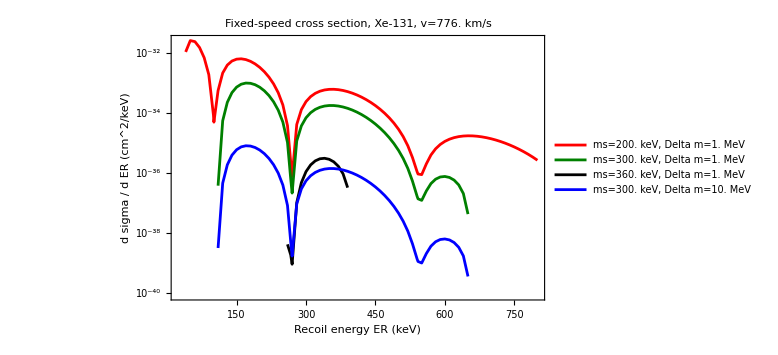

```mathematica
(* 使用第二节的反冲能量网格，并把额外检查点加入。 *)
fixedSpeedEnergyGridKeV = Sort[DeleteDuplicates[N[Join[  (* 合并并排序固定速度截面所需能量点 *)
  Range[recoilMinKeV, recoilMaxKeV, recoilStepKeV],  (* 生成指定范围的数值点 *)
  extraRecoilEnergiesKeV,  (* 传入参数：把额外检查能量加入网格 *)
  comparisonEnergiesKeV  (* 传入参数：设置输出对照表的反冲能量 *)
]]]];  (* 结束当前参数列表、计算块或表达式 *)

(* 对每组质量逐点计算本节公式，结果保存为 {ER, d sigma/d ER}。 *)
fixedSpeedCrossSections = Table[  (* 逐质量组合和能量计算固定速度截面 *)
  Table[{  (* 按给定变量遍历并生成表格 *)
    recoilKeV,  (* 传入参数 recoilKeV，供当前函数使用 *)
    DifferentialCrossSection[  (* 计算单核固定速度微分截面 *)
      diagnosticIsotope, recoilKeV, diagnosticSpeedKmPerS,  (* 本行涉及：选择单核截面的同位素质量数；设置检查用入射速度 km/s *)
      benchmark[[1]] * keVToGeV, benchmark[[2]] * megaElectronVoltToGeV,  (* 本行涉及：定义 keV 到 GeV 的换算因子；定义 MeV 到 GeV 的换算因子 *)
      diagnosticParameters  (* 传入参数 diagnosticParameters，供当前函数使用 *)
    ] * gevMinus2ToCm2 * 10^-6  (* 组织当前列表、函数参数或计算块 *)
  }, {recoilKeV, fixedSpeedEnergyGridKeV}],  (* 组织当前列表、函数参数或计算块 *)
  {benchmark, benchmarks}  (* 设置该循环的变量和遍历范围，或组织当前结果 *)
];  (* 结束当前参数列表、计算块或表达式 *)

(* 对数坐标只绘制截面为正的点。 *)
positiveCrossSections = (Select[#, Last[#] > 0 &] &) /@ fixedSpeedCrossSections;  (* 筛选正值以便使用对数坐标 *)
activeCrossSectionIndices = Select[Range[Length[benchmarks]],  (* 找出有正值数据的质量组合 *)
  Length[positiveCrossSections[[#]]] > 0 &];  (* 本行涉及：筛选正值以便使用对数坐标 *)

If[Length[activeCrossSectionIndices] == 0,  (* 判断条件，根据结果执行相应分支 *)
  Print["所选速度和能量范围内的截面均为零。"],  (* 显示当前说明或计算结果 *)
  fixedSpeedLabels = ("ms=" <> ToString[#[[1]]] <> " keV, Delta m=" <>  (* 由质量组合自动生成图例 *)
      ToString[#[[2]]] <> " MeV" &) /@ benchmarks;  (* 将数值或表达式转换为文字 *)
  fixedSpeedPlot = ListLogPlot[  (* 绘制固定速度微分截面曲线 *)
    positiveCrossSections[[activeCrossSectionIndices]],  (* 本行涉及：筛选正值以便使用对数坐标；找出有正值数据的质量组合 *)
    Joined -> True,  (* 指定该函数的参数、替换规则或显示选项 *)
    PlotRange -> All,  (* 指定该函数的参数、替换规则或显示选项 *)
    Frame -> True,  (* 设置表格边框或绘图边框 *)
    (* 和后面的事件率图使用相同的基准颜色。 *)
    PlotStyle -> Table[  (* 按给定变量遍历并生成表格 *)
      {Red, RGBColor[0, .5, 0], Black, Blue}[[1 + Mod[index - 1, 4]]],  (* 组织当前列表、函数参数或计算块 *)
      {index, activeCrossSectionIndices}  (* 组织当前列表、函数参数或计算块 *)
    ],  (* 结束当前参数列表、计算块或表达式 *)
    FrameLabel -> {"Recoil energy ER (keV)", "d sigma / d ER (cm^2/keV)"},  (* 设置绘图坐标轴名称和单位 *)
    PlotLegends -> Placed[fixedSpeedLabels[[activeCrossSectionIndices]], Below],  (* 设置曲线图例和显示位置 *)
    PlotLabel -> "Fixed-speed cross section, Xe-" <> ToString[diagnosticIsotope] <>  (* 将数值或表达式转换为文字 *)
      ", v=" <> ToString[diagnosticSpeedKmPerS] <> " km/s",  (* 将数值或表达式转换为文字 *)
    ImageSize -> Large  (* 指定该函数的参数、替换规则或显示选项 *)
  ];  (* 结束当前参数列表、计算块或表达式 *)
  fixedSpeedPlot  (* 传入参数：绘制固定速度微分截面曲线 *)
]  (* 结束当前参数列表、计算块或表达式 *)
```

### 4.8 从单核固定速度结果继续

本节计算 chi1 + A -> chi1 + A + s。AFH 原程序提供各氙同位素的核响应，DifferentialCrossSection 使用本模型的两张辐射图、chi2 传播子和三体相空间积分。AFH 的 DiffCrossSection 是弹性 2→2 EFT 截面，不作为这里的三体截面。

固定速度截面使用 1.4 节所选单一同位素和速度；天然氙率对第一节的全部氙同位素及实验室速度分布求和积分。质量、g1、g2、gVN 和晕参数都从第一、二节读取，修改后请从头运行。

```mathematica
(* 固定单核素和单速度的截面已在上方逐项计算；继续下一节计算速度和同位素平均。 *)
```

## 五、速度分布与天然氙的微分截面

前一节得到固定速度、单一同位素 A 的 dσA/dER。这里用实验室速率概率密度 F(v) 计算普通速度平均，再用同位素数目丰度 ηA 加权。各同位素有各自的核响应、核质量和速度阈值。已列同位素丰度直接相加，不重新归一化；结果单位为 GeV^-3，乘 0.3893793721×10^-33 可换算为 cm.b2/keV。

⟨dσ/dER⟩ = ∑A ηA ∫vmin,A^vmax F(v) [dσA(v)/dER] dv

```mathematica
Clear[SpeedAveragedCrossSection, NaturalAveragedCrossSection];
SpeedAveragedCrossSection[a_Integer, er_?NumericQ, ms_?NumericQ, dm_?NumericQ, p_Association] := Module[
  {vmin, vmax, opt, integrand}, (* 设置速度上下限和积分选项 *)
  vmin = VMin[p["mchi"], ms, a*0.93149410242, er*10^-6]; (* 该同位素的阈值，km/s *)
  vmax = p["vEarth"] + p["vEsc"]; (* 地球系最大速度，km/s *)
  If[vmin >= vmax, Return[0.]]; (* 无可用速度时截面为零 *)
  opt = p["nv"]; (* 使用主计算中的速度积分设置 *)
  integrand[v_?NumericQ] := SpeedPDF[v,p["v0"],p["vEarth"],p["vEsc"]] DifferentialCrossSection[a,er,v,ms,dm,p]; (* 概率密度乘微分截面 *)
  NIntegrate[integrand[v],{v,vmin,vmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0}, AccuracyGoal->opt["AccuracyGoal"],PrecisionGoal->opt["PrecisionGoal"],MaxRecursion->opt["MaxRecursion"]] (* 普通速度平均 *)
];
NaturalAveragedCrossSection[er_?NumericQ,ms_?NumericQ,dm_?NumericQ,p_Association] := Total[Table[p["abundance"][a] SpeedAveragedCrossSection[a,er,ms,dm,p],{a,p["isotopes"]}]]; (* 各同位素数目丰度加权 *)
Print["已定义单同位素及天然氙的普通速度平均微分截面；实际数值由下一节的扩展计算开关控制。"];
```

已定义单同位素及天然氙的普通速度平均微分截面；实际数值由下一节的扩展计算开关控制。

## 六、总截面：对允许的核反冲能量积分

总截面是 dσA/dER 在运动学允许的完整 ER 范围上的积分。上下限由 χ1+A→(χ1+s)+A 的两体运动学求得，其中组合末态的最小不变质量为 mχ1+ms。这里使用与主计算相同的核质量近似 mA=A×0.93149410242 GeV。

σA(v) = ∫ER,min^ER,max (dσA/dER) dER；  ⟨σ⟩Xe = ∑A ηA ∫ F(v) σA(v) dv。

```mathematica
Clear[RecoilEnergyBoundsKeV, TotalCrossSection];
RecoilEnergyBoundsKeV[a_Integer,v_?NumericQ,ms_?NumericQ,p_Association] := Module[
 {m,ma,beta,e,s,root,ein,eout,pii,pf,lo,hi}, (* 质心系运动学变量 *)
 {m,ma,beta}=N[Rationalize[{p["mchi"],a*0.93149410242,v/299792.458},0],40]; (* 提高计算精度以减少大质量相减误差 *)
 e=m/Sqrt[1-beta^2]; s=m^2+ma^2+2 ma e; root=Sqrt[s]; (* 入射能量与总不变量 *)
 If[root <= ma+m+ms,Return[{0.,0.}]]; (* 三体末态阈值未打开 *)
 ein=(s+ma^2-m^2)/(2 root); (* 初态核在质心系中的能量 *)
 eout=(s+ma^2-(m+ms)^2)/(2 root); (* 最小组合质量对应的末态核能量 *)
 pii=Sqrt[Max[0,ein^2-ma^2]]; pf=Sqrt[Max[0,eout^2-ma^2]]; (* 初末态质心动量 *)
 lo=(ein eout-pii pf-ma^2)/ma; hi=(ein eout+pii pf-ma^2)/ma; (* t=-2 mA ER *)
 N[10^6 {Max[0,lo],Max[0,hi]},16] (* GeV 转 keV *)
];
TotalCrossSection[a_Integer,v_?NumericQ,ms_?NumericQ,dm_?NumericQ,p_Association] := Module[{bounds,integrand},
 bounds=RecoilEnergyBoundsKeV[a,v,ms,p]; (* 全部运动学允许反冲能量，keV *)
 If[bounds[[2]]<=bounds[[1]],Return[0.]]; (* 阈值以下总截面为零 *)
 integrand[er_?NumericQ]:=10^-6 DifferentialCrossSection[a,er,v,ms,dm,p]; (* dER 从 keV 换为 GeV *)
 NIntegrate[integrand[er],{er,bounds[[1]],bounds[[2]]},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->Infinity,PrecisionGoal->2,MaxRecursion->5] (* 结果 GeV^-2 *)
];
Clear[NaturalAveragedTotalCrossSection];
NaturalAveragedTotalCrossSection[ms_?NumericQ,dm_?NumericQ,p_Association] := Module[{vmax,opt,integrand},
 vmax=p["vEarth"]+p["vEsc"]; opt=p["nv"]; (* 最大速度及速度积分设置 *)
 Total[Table[
  integrand[v_?NumericQ]:=SpeedPDF[v,p["v0"],p["vEarth"],p["vEsc"]] TotalCrossSection[a,v,ms,dm,p]; (* 每个速度的总截面乘概率密度 *)
  p["abundance"][a] NIntegrate[integrand[v],{v,0,vmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->Infinity,PrecisionGoal->2,MaxRecursion->opt["MaxRecursion"]], (* 每种同位素独立积分再加权 *)
  {a,p["isotopes"]}]] (* 天然氙平均总截面，GeV^-2 *)
];
Print["已定义反冲能量边界和总截面；完整数值积分在下一单元选择运行。"];
```

已定义反冲能量边界和总截面；完整数值积分在下一单元选择运行。

下面的完整嵌套积分计算量较大。首次运行时仅定义函数；把 runExtendedCrossSections 改为 True 后重新运行本单元，即可计算当前检查点的速度平均微分截面和固定速度总截面。总截面单位换算为 cm.b2 使用 1 GeV^-2 = 0.3893793721×10^-27 cm.b2。

```mathematica
runExtendedCrossSections = False; (* 改为 True 后运行耗时较长的积分 *)
If[TrueQ[runExtendedCrossSections],
 averagedXeDSigma = NaturalAveragedCrossSection[diagnosticRecoilKeV,selectedScalarMassGeV,selectedSplittingGeV,diagnosticParameters]; (* 天然氙与速度平均微分截面 *)
 totalXe131 = TotalCrossSection[diagnosticIsotope,diagnosticSpeedKmPerS,selectedScalarMassGeV,selectedSplittingGeV,diagnosticParameters]; (* 单核素、固定速度总截面 *)
 Print["天然氙速度平均微分截面 GeV^-3: ",averagedXeDSigma]; (* 显示平均微分截面 *)
 Print["固定速度总截面 GeV^-2: ",totalXe131]; (* 显示总截面 *)
 Print["固定速度总截面 cm^2: ",totalXe131*0.3893793721*10^-27]; (* 显示厘米单位结果 *)
];
If[!TrueQ[runExtendedCrossSections], Print["速度平均截面和总截面尚未计算；将本单元开关设为 True 后重新运行。"]];
```

速度平均截面和总截面尚未计算；将本单元开关设为 True 后重新运行。

## 七、事件率：速度平均时加入入射通量

事件率使用 F(v) v dσA/dER 的速度积分，并乘暗物质数密度、靶核数和单位转换。故普通速度平均截面不能直接代入事件率；截面还需通量加权。曝光量和探测效率还需另行计入，当前结果是单位质量、单位时间、单位反冲能量的理论事件率。

(d R_Xe)/(d E_R)=N_Av/OverBar[M_Xe]ρ_χ/m_χ_1∑_A x_A ∫d^3 v f_lab(v) v (d σ_A)/(d E_R)

每种同位素分别使用自身核响应、核质量和三体运动学，再对实验室速度积分并按天然数丰度求和。横截面末态为 chi1 + A + s。

单位质量天然氙的理论反冲率为 N_Av / Mbar × rhoχ / mχ × Σ_A x_A × ∫ d.b3v f_lab(v) v (dσ_A / dER)。Mbar 用 g/mol 时，每千克靶材的总核数为 1000 N_Av/Mbar。

速度分布采用归一化的截断 Maxwell 分布。对于仅依赖速率大小的截面，f_speed(v) dv = ∫dΩ v.b2 f_lab(v) dv，积分为 ∫dv f_speed(v) (v/c) (dσ/dER)。程序在单位换算时乘 c。

本节速率公式中，N_Av 是阿伏伽德罗常数，Mbar_Xe 是天然氙平均摩尔质量，rho_chi/m_chi1 是暗物质数密度，x_A 是 A 同位素的数目丰度；f_lab(v) 按本节采用的实验室速度分布归一化。每个 A 的 d sigma_A/dER 均单独使用该核的质量、AFH 核响应及三体运动学阈值。

单位核数也要与靶材质量单位一致：若 Mbar_Xe 以 g/mol 表示，则 N_Av/Mbar_Xe 给出每克氙的核数；换成每千克乘 1000，换成每吨再乘 10^6。速率函数内部继续把时间、能量和自然单位截面统一转换，笔记本表格报告 events/(tonne year keV)。

为避免把自然单位速度和实验室单位混用，代码将 d^3v 先化为速率概率密度 f_speed(v) dv，再使用相对速度 v/c 形成通量因子，并在单位换算中恢复 c。积分的是速度分布内所有允许速度的 f_speed(v) (v/c) d sigma/dER，不是把截面简单乘以平均速度。

同位素丰度求和使用第一节定义的 abundances。未提供 AFH 核响应的同位素不会自动补入，也不会把剩余七种丰度重新缩放到 1；修改丰度字典或 isotope 列表后，应重新检查表格的丰度和。

## 八、计算极点宽度事件率

曲线是单位曝光、单位核反冲能量的理论事件率，单位 events/(tonne year keV)，未加探测器效率、能量分辨率或背景。用于论文时需逐点检查积分及能量网格收敛。

```mathematica
(* 合并用户设置的反冲能量网格和代表能量。 *)
energies = Sort[DeleteDuplicates[N[Join[Range[recoilMinKeV,recoilMaxKeV,recoilStepKeV],
 extraRecoilEnergiesKeV, comparisonEnergiesKeV]]]];
(* 每个能量点使用当前模型算出的极点宽度，计算四组质量参数的事件率。 *)
Print["计算极点宽度事件率，g2 = ", g2val];
poleSeconds = AbsoluteTiming[curvesPole = MakeCurves[energies,benchmarks,pPole];][[1]];
Print["能量点数：",Length[energies],"；耗时（秒）：",poleSeconds];
```

计算极点宽度事件率，g2 = 1.

Computing benchmark 1 / 4; ms,dm = {200.,1.}

Computing benchmark 2 / 4; ms,dm = {300.,1.}

Computing benchmark 3 / 4; ms,dm = {360.,1.}

Computing benchmark 4 / 4; ms,dm = {300.,10.}

能量点数：83；耗时（秒）：458.532

## 九、绘制天然氙事件率曲线

每个颜色对应一组质量参数；所有曲线都使用相应参数下的极点宽度。

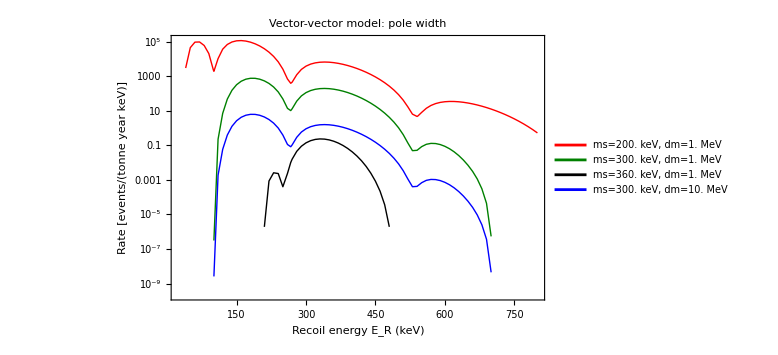

```mathematica
(* 每组质量使用一种颜色；只绘制包含极点宽度的事件率。 *)
baseColors={Red,RGBColor[0,.5,0],Black,Blue};
colors=Table[baseColors[[1+Mod[i-1,Length[baseColors]]]],{i,Length[benchmarks]}];
benchmarkLabel[{msKeV_,dmMeV_}]:="ms="<>ToString[msKeV]<>" keV, dm="<>ToString[dmMeV]<>" MeV";
labels=benchmarkLabel/@benchmarks;
positivePole=(Select[#,Last[#]>0&]&)/@curvesPole;  (* 对数图只保留正值 *)
activeRateIndices=Select[Range[Length[positivePole]],Length[positivePole[[#]]]>0&];
ratePlot=If[activeRateIndices==={},
 Print["当前网格没有正的事件率。"];Graphics[{}],
 ListLogPlot[positivePole[[activeRateIndices]],Joined->True,
 PlotStyle->(Directive[#,Thick]&/@colors[[activeRateIndices]]),PlotRange->All,Frame->True,
 FrameLabel->{"Recoil energy E_R (keV)","Rate [events/(tonne year keV)]"},
 PlotLegends->Placed[labels[[activeRateIndices]],Below],ImageSize->Large,
 PlotLabel->"Vector-vector model: pole width"]];
ratePlot
```

## 十、输出代表能量处的事件率

下表列出各质量组合在指定能量处的极点宽度事件率；相空间关闭时事件率为零。

```mathematica
(* 列出各组质量参数在选定能量处的极点宽度事件率。 *)
energiesToCheck=N[comparisonEnergiesKeV];
compareRows=Flatten[Table[Module[{idx},idx=First@FirstPosition[energies,er];
 {i,er,curvesPole[[i,idx,2]]}],{i,Length[benchmarks]},{er,energiesToCheck}],1];
Grid[Prepend[compareRows,{"benchmark","ER [keV]","pole-width rate [events/(tonne year keV)]"}],Frame->All]
```

benchmark | ER [keV] | pole-width rate [events/(tonne year keV)]
1 | 200. | 56004.2
1 | 300. | 3817.79
1 | 542. | 5.05837
2 | 200. | 670.822
2 | 300. | 112.039
2 | 542. | 0.0570487
3 | 200. | 0.
3 | 300. | 0.139141
3 | 542. | 0.
4 | 200. | 5.47905
4 | 300. | 0.907263
4 | 542. | 0.000466825

## 十一、可选：导出图像和数据

执行本单元才会导出极点宽度事件率曲线和数据；重复运行会覆盖相同的新文件名。

```mathematica
(* 可选导出：只保存极点宽度曲线及对应的宽度表。 *)
outDir=FileNameJoin[{baseDir,"g2_output"}];If[!DirectoryQ[outDir],CreateDirectory[outDir]];
Do[Export[FileNameJoin[{outDir,"benchmark_"<>ToString[i]<>"_pole.csv"}],
 Prepend[curvesPole[[i]],{"ER_keV","pole_rate_events_per_tonne_year_keV"}],"CSV"],{i,Length[benchmarks]}];
Export[FileNameJoin[{outDir,"pole_widths.csv"}],Prepend[widthTable,{"ms_keV","delta_m_MeV","gamma_keV"}],"CSV"];
Export[FileNameJoin[{outDir,"selected_pole_energies.csv"}],Prepend[compareRows,{"benchmark","ER_keV","pole_rate"}],"CSV"];
Export[FileNameJoin[{outDir,"rate_pole.png"}],ratePlot,"PNG",ImageResolution->180];
Print["结果已导出至：",outDir];
```

结果已导出至：C:\Users\local-user\Documents\ChatGPT\3 body HDM\天然氙三体散射\g2_output

本笔记本输出的是给定近似和参数的理论预测，不能单独确定原图真实输入或实验事件数。固定极点宽度、离壳自能处理、Dirac/Majorana 约定、核响应与完整截面归一化均应单独审计。

## 以下为独立验证与数值检查

验证前先运行主计算。下方 gaussI6 与主 I6 使用不同的数值求积和运动学构造，但共用物理模型、宽度处方和自旋迹；它用于数值方法对照，并不能单独证明核响应或整个理论归一化。每个验证都应核对当前输入、运行状态和比较范围。

### Gauss 求积对照函数

```mathematica
gaussI6[m_?NumericQ,ms_?NumericQ,dm_?NumericQ,mA_?NumericQ,er_?NumericQ,v_?NumericQ,order_List,width_?NumericQ]:=Module[
 {beta,lor,ee,pz,qq,wlo,whi,pin,quadrW,quadrZ,quadrP,sum=0.,w2,weight,cq,q,K,bK,ps,e3,ref,e1,e2,lam,W,kabs,Ek,Ep,z,phi,n,k,pp,ang,pa,m2},
 If[!NumericQ[width] || !TrueQ[width>=0],Throw["Invalid constant pole width"]];  (* 设置相空间积分节点 *)

 If[er<=0 || v<=0,Return[0.]];  (* 运动学不允许时返回零 *)

 beta=v/cKm;  (* Gauss 对照：速度转为无量纲 β *)
lor=1/Sqrt[1-beta^2];  (* Gauss 对照：计算洛伦兹因子 *)
ee=m lor;  (* Gauss 对照：计算入射暗物质能量 *)
pz=m lor beta;  (* Gauss 对照：计算入射暗物质沿 z 轴的动量 *)
qq=Sqrt[2 mA er+er^2];  (* 计算核反冲对应的四动量 *)

 wlo=(m+ms)^2;  (* 设置三体不变质量积分下限 *)
whi=m^2+2 pz qq-2(ee+mA)er;  (* 设置三体不变质量积分上限 *)

 If[whi<=wlo,Return[0.]];  (* 运动学不允许时返回零 *)

 m2=m+dm;  (* 计算激发态质量 *)

 If[whi>=m2^2,Throw["On-shell chi2 accessible: off-shell calculation aborted"]];  (* 检查激发态传播子的适用条件 *)

 pin={ee,0.,0.,pz};  (* Gauss 对照：构造入射暗物质四动量 *)
quadrW=gl[order[[1]]];  (* 生成 Gauss 积分节点和权重 *)
quadrZ=gl[order[[2]]];  (* 生成 Gauss 积分节点和权重 *)
quadrP=gl[order[[3]]];  (* 生成 Gauss 积分节点和权重 *)

 Do[
  w2=(whi+wlo)/2+(whi-wlo)node[[1]]/2;  (* 将 Gauss 节点映射到 W.b2 积分区间 *)
weight=node[[2]](whi-wlo)/2;  (* 计算该 W.b2 节点的权重和区间 Jacobian *)

  cq=Clip[(w2-m^2+2(ee+mA)er)/(2 pz qq),{-1.,1.}];  (* 计算核反冲对应的四动量 *)

  q={er,qq Sqrt[Max[0.,1-cq^2]],0.,qq cq};  (* 计算核反冲对应的四动量 *)
K=pin-q;  (* 由四动量守恒得到 χ1+s 系统四动量 *)
bK=K[[2;;4]]/K[[1]];  (* 计算 χ1+s 质心系相对实验室系的速度 *)

  ps=boost[pin,-bK];  (* 将入射动量变换到 χ1+s 质心系 *)
e3=Normalize[ps[[2;;4]]];  (* 以质心系入射方向定义极轴 *)
ref=If[Abs[e3[[1]]]>.9,{0.,1.,0.},{1.,0.,0.}];  (* 选择不与极轴近乎平行的参考方向 *)

  e1=Normalize[Cross[ref,e3]];  (* 计算垂直于极轴的第一个单位矢量 *)
e2=Cross[e3,e1];  (* 计算第二个横向单位矢量 *)

  lam=Max[0.,(w2-(m+ms)^2)(w2-(m-ms)^2)];  (* 计算 Källén 函数，并限制阈值处舍入误差 *)
 W=Sqrt[w2];  (* 从不变质量平方得到质心系总能量 *)

  kabs=Sqrt[lam]/(2 W);  (* 计算质心系中的末态动量大小 *)
Ek=(w2-m^2+ms^2)/(2 W);  (* 计算标量在质心系的能量 *)
Ep=(w2+m^2-ms^2)/(2 W);  (* 计算末态 χ1 在质心系的能量 *)

  ang=0.;  (* 初始化极角积分的累加值 *)
Do[z=zn[[1]];  (* 遍历 Gauss 极角余弦节点 *)
pa=0.;  (* 初始化该极角下方位角平均的累加值 *)
Do[phi=Pi(pn[[1]]+1);  (* 将方位角节点映射到 0 到 2π *)

   n=z e3+Sqrt[Max[0.,1-z^2]](Cos[phi] e1+Sin[phi] e2);  (* 由极角和方位角构造标量的单位方向 *)

   k=boost[Join[{Ek},kabs n],bK];  (* 将标量四动量变换到实验室系 *)
pp=boost[Join[{Ep},-kabs n],bK];  (* 将末态 χ1 四动量变换到实验室系 *)

   pa+=pn[[2]]/2 trace[pin,pp,k,m,m2,w2,width],{pn,quadrP}];  (* 设置相空间积分节点 *)

   ang+=zn[[2]] pa,{zn,quadrZ}];  (* 设置相空间积分节点 *)

  sum+=weight Sqrt[lam]/w2 ang,{node,quadrW}];  (* 设置相空间积分节点 *)
sum];  (* 返回各积分节点的加权和 *)


Print["Gauss 对照函数已定义；主计算仍使用 FeynCalc 和 NIntegrate。"];
```

Gauss 对照函数已定义；主计算仍使用 FeynCalc 和 NIntegrate。

先运行前面的模型计算，再按需运行以下验证。不同方法的比较及其共享输入在各节标明。

### A. 数值基准、内部一致性与收敛

#### 固定基准点及宽度检验

本检查使用固定历史基准 mχ1=1000 GeV、ms=300 keV、Δm=1 MeV、mA=122 GeV、ER=200 keV、v=776 km/s、g2=1。这里的 mA 恰好设为 122 GeV，并不等于主检查点的 131×0.93149410242≈122.02573 GeV，因此 I6 基准不应与主 benchmark 表的数值直接比较。晕归一化与宽度单独比较；I6 的历史数值只是回归参考，不构成独立物理证明。

```mathematica
(* 独立基准：速度分布、衰变宽度和含极点宽度的 I6。 *)
haloNorm=NIntegrate[SpeedPDF[v,220.,232.,544.],{v,0,312,776}];
testWidth=Chi2Width[1000.,0.0003,0.001,1.];
testPole=I6[1000.,0.0003,0.001,122.,0.0002,776.,finePhaseSpaceOrders,testWidth];
Grid[{{"check","Mathematica","reference"},{"halo integral",haloNorm,1.},
 {"pole width [keV]",10^6 testWidth,151.8239115788},
 {"I6 pole [GeV^2]",testPole,868246.7879206}},Frame->All]
```

check | Mathematica | reference
halo integral | 1. | 1.
pole width [keV] | 151.824 | 151.824
I6 pole [GeV^2] | 868218.7489790512882607245368261787207048 | 868247.

```mathematica
If[Abs[haloNorm-1.]>10^-6 || Abs[testWidth/0.0001518239115787696-1]>10^-8 ||
 Abs[testPole/868246.7879206-1]>2*10^-4,
 Print["ERROR: diagnostic check failed."];Abort[],Print["PASS: pole-width benchmark checks."]]
```

PASS: pole-width benchmark checks.

#### FeynCalc 与手写矩阵迹对照

两种自旋迹使用同一 NIntegrate 相空间实现；此表检验自旋迹，不独立验证相空间归一化。

```mathematica
(* 同一个运动学点和积分节点，分别使用手写迹和 FeynCalc 迹。 *)
fcOriginalI6 = Block[{trace = manualTrace},
 I6[darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV,
  selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS,
  phaseSpaceOrders, selectedWidthGeV]];
fcFeynCalcI6 = I6[darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV,
 selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS,
 phaseSpaceOrders, selectedWidthGeV];
fcRelativeDifference = If[fcOriginalI6 != 0, fcFeynCalcI6/fcOriginalI6 - 1, Indeterminate];
Grid[{{"计算方式", "I6 [GeV.b2]"}, {"手写 Dirac 矩阵迹", fcOriginalI6},
 {"FeynCalc 自旋迹（主计算）", fcFeynCalcI6}, {"FeynCalc / 手写 - 1", fcRelativeDifference}}, Frame -> All]
```

计算方式 | I6 [GeV.b2]
手写 Dirac 矩阵迹 | 869799.631806812805733514037296
FeynCalc 自旋迹（主计算） | 869799.631806812805733514037296
FeynCalc / 手写 - 1 | 0.

#### 分项计算与截面接口的内部一致性

两种调用共用相同公式和 FeynCalc 自旋迹，不能视为独立物理验证。

```mathematica
(* 分项计算与公共截面接口使用同一公式，是内部一致性检查。 *)
selectedDSigmaCheck = DifferentialCrossSection[diagnosticIsotope, diagnosticRecoilKeV,
 diagnosticSpeedKmPerS, selectedScalarMassGeV, selectedSplittingGeV, diagnosticParameters];
selectedRelativeDifference = If[selectedDSigmaGeVMinus3 != 0,
 selectedDSigmaCheck/selectedDSigmaGeVMinus3 - 1, If[selectedDSigmaCheck == 0, 0, Indeterminate]];
Grid[{{"计算方式", "d sigma/d ER [GeV^-3]"}, {"分项计算", selectedDSigmaGeVMinus3},
 {"公共截面接口", selectedDSigmaCheck}, {"接口 / 分项 - 1", selectedRelativeDifference}}, Frame -> All]
```

计算方式 | d sigma/d ER [GeV^-3]
分项计算 | 1.90756
公共截面接口 | 1.90756
接口 / 分项 - 1 | -1.11022×10^-16

#### 固定速度 NIntegrate 精度检查

比较两组 NIntegrate 精度参数对固定速度截面的影响。

```mathematica
(* 增大 W.b2、极角和方位角的NIntegrate 精度设置后重新计算。 *)
selectedI6FineGeV2 = I6[  (* 使用更高NIntegrate 精度设置重新计算 I6 *)
  darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV,  (* 本行涉及：输入暗物质 chi1 质量，单位 GeV；选择并换算标量质量为 GeV；选择并换算质量劈裂为 GeV *)
  selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS,  (* 本行涉及：设置检查用入射速度 km/s；用 A 乘原子质量单位近似核质量；将反冲能量换算为 GeV *)
  finePhaseSpaceOrders, selectedWidthGeV  (* 本行涉及：设置更高的三体相空间NIntegrate 精度设置；根据宽度处方确定中间态宽度 *)
];  (* 结束当前参数列表、计算块或表达式 *)
selectedDSigmaFine = selectedPrefactorGeVMinus5 * selectedI6FineGeV2;  (* 由较高精度 I6 计算对照截面 *)
selectedFineDifference = If[selectedDSigmaFine != 0,  (* 计算低阶与较高精度结果的相对差 *)
  selectedDSigmaGeVMinus3 / selectedDSigmaFine - 1,  (* 本行涉及：将截面前因子乘以 I6；由较高精度 I6 计算对照截面 *)
  If[selectedDSigmaGeVMinus3 == 0, 0, Indeterminate]  (* 判断条件，根据结果执行相应分支 *)
];  (* 结束当前参数列表、计算块或表达式 *)
Grid[{  (* 将数据整理为表格 *)
  {"NIntegrate 精度设置", "I6 [GeV.b2]", "d sigma/d ER [GeV^-3]"},  (* 定义或输出表格的一行及其对应物理量 *)
  {phaseSpaceOrders, selectedI6GeV2, selectedDSigmaGeVMinus3},  (* 组织当前列表、函数参数或计算块 *)
  {finePhaseSpaceOrders, selectedI6FineGeV2, selectedDSigmaFine},  (* 组织当前列表、函数参数或计算块 *)
  {"粗/细 - 1", "", selectedFineDifference}  (* 定义或输出表格的一行及其对应物理量 *)
}, Frame -> All]  (* 设置表格边框或绘图边框 *)
```

NIntegrate 精度设置 | I6 [GeV.b2] | d sigma/d ER [GeV^-3]
<|AccuracyGoal→3,PrecisionGoal→3,WorkingPrecision→30,MaxRecursion→6|> | 869799.631806812805733514037296 | 1.90756
<|AccuracyGoal→5,PrecisionGoal→5,WorkingPrecision→40,MaxRecursion→9|> | 869799.6056072901485676672743997034236271 | 1.90756
粗/细 - 1 |  | 3.01213×10^-8

#### 天然氙事件率 NIntegrate 收敛检查

同一极点宽度处方下比较不同 NIntegrate 精度设置；需在能量阈值和核响应谷底附近进行收敛检查。

```mathematica
(* 在同一个极点宽度处方下，比较不同 NIntegrate 精度设置。 *)
{convergenceMsKeV,convergenceDeltaMMeV}=benchmarks[[convergenceBenchmarkIndex]];
convergenceMsGeV=convergenceMsKeV*keVToGeV;
convergenceDeltaMGeV=convergenceDeltaMMeV*megaElectronVoltToGeV;
fineOrders=<|"quad"->finePhaseSpaceOrders,"nv"->fineSpeedOrder|>;
pPoleFine=Join[pPole,fineOrders];
coarse1=Rate[convergenceRecoilKeV,convergenceMsGeV,convergenceDeltaMGeV,pPole];
fine1=Rate[convergenceRecoilKeV,convergenceMsGeV,convergenceDeltaMGeV,pPoleFine];
relativeDifference[coarse_,fine_]:=If[fine>0,coarse/fine-1,"NA"];
Print["收敛点：",benchmarkLabel[benchmarks[[convergenceBenchmarkIndex]]],", ER=",convergenceRecoilKeV," keV"];
Grid[{{"宽度处方","基础精度","较高精度","粗/细 - 1"},
 {"极点宽度",coarse1,fine1,relativeDifference[coarse1,fine1]}},Frame->All]
```

收敛点：ms=300. keV, dm=1. MeV, ER=200. keV

宽度处方 | 基础精度 | 较高精度 | 粗/细 - 1
极点宽度 | 670.822 | 670.823 | -1.04076×10^-6

#### 天然氙速度分布、同位素和形状检查

这部分有两个互补的加和检查：逐个 isotope 运行同一 halo-rate 函数后相加；再以完整 isotope 列表直接运行一次。两种方式采用相同的天然氙平均摩尔质量、halo 参数和耦合，二者相对差应接近浮点舍入误差。若不一致，优先检查输入列表、丰度字典、宽度模式和参数是否从第一节完整重算。

### 检验速度分布、质量组合和同位素贡献

```mathematica
(* 选择待比较的质量组合和反冲能量。 *)
haloBenchmarkIndex = diagnosticBenchmarkIndex;  (* 选择天然氙反冲率的质量组合 *)
haloRecoilKeV = diagnosticRecoilKeV;  (* 设置天然氙同位素贡献的检查能量 *)
haloScalarMassGeV = benchmarks[[haloBenchmarkIndex, 1]] * keVToGeV;  (* 将所选标量质量换算为 GeV *)
haloSplittingGeV = benchmarks[[haloBenchmarkIndex, 2]] * megaElectronVoltToGeV;  (* 将所选质量劈裂换算为 GeV *)

(* 对实验室速率分布积分。分界点来自逃逸速度截断。 *)
haloBoundary = parameters["vEsc"] - parameters["vEarth"];  (* 计算速度分布的分段边界 *)
haloMaximum = parameters["vEsc"] + parameters["vEarth"];  (* 计算实验室系速率的最大值 *)
haloNormalization = NIntegrate[  (* 数值检查实验室速率概率密度的归一化 *)
  SpeedPDF[v, parameters["v0"], parameters["vEarth"], parameters["vEsc"]],  (* 计算实验室系速率概率密度 *)
  {v, 0, haloBoundary, haloMaximum}  (* 组织当前列表、函数参数或计算块 *)
];  (* 结束当前参数列表、计算块或表达式 *)

(* 每次只保留一个同位素，保留其天然丰度和天然氙平均摩尔质量。 *)
isotopeContributions = Table[  (* 逐种同位素计算其天然丰度加权贡献 *)
  Module[{oneIsotopeParameters, threshold, contribution},  (* 定义局部变量和局部计算 *)
    oneIsotopeParameters = Join[pPole, <|"isotopes" -> {isotope}|>];  (* 保留当前同位素及天然氙摩尔质量的参数 *)
    threshold = VMin[  (* 计算该同位素三体散射的速度阈值 *)
      darkMatterMassGeV, haloScalarMassGeV,  (* 本行涉及：输入暗物质 chi1 质量，单位 GeV；将所选标量质量换算为 GeV *)
      isotope * 0.93149410242, haloRecoilKeV * keVToGeV  (* 本行涉及：定义 keV 到 GeV 的换算因子；设置天然氙同位素贡献的检查能量 *)
    ];  (* 结束当前参数列表、计算块或表达式 *)
    contribution = Rate[  (* 计算该同位素对天然氙率的贡献 *)
      haloRecoilKeV, haloScalarMassGeV, haloSplittingGeV,  (* 本行涉及：设置天然氙同位素贡献的检查能量；将所选标量质量换算为 GeV；将所选质量劈裂换算为 GeV *)
      oneIsotopeParameters  (* 传入参数：保留当前同位素及天然氙摩尔质量的参数 *)
    ];  (* 结束当前参数列表、计算块或表达式 *)
    {isotope, abundances[isotope], threshold, contribution}  (* 设置该循环的变量和遍历范围，或组织当前结果 *)
  ],  (* 结束当前参数列表、计算块或表达式 *)
  {isotope, isotopes}  (* 设置该循环的变量和遍历范围，或组织当前结果 *)
];  (* 结束当前参数列表、计算块或表达式 *)

(* 直接求天然氙事件率，并与逐同位素结果之和对照。 *)
haloRateTotal = Rate[  (* 使用完整同位素列表直接计算总率 *)
  haloRecoilKeV, haloScalarMassGeV, haloSplittingGeV, pPole  (* 本行涉及：创建极点宽度参数组；设置天然氙同位素贡献的检查能量；将所选标量质量换算为 GeV *)
];  (* 结束当前参数列表、计算块或表达式 *)
isotopeRateSum = Total[isotopeContributions[[All, 4]]];  (* 把各同位素贡献相加 *)
sumRelativeDifference = If[haloRateTotal != 0,  (* 计算逐项相加与直接总率的相对差 *)
  isotopeRateSum / haloRateTotal - 1,  (* 本行涉及：使用完整同位素列表直接计算总率；把各同位素贡献相加 *)
  If[isotopeRateSum == 0, 0, Indeterminate]  (* 判断条件，根据结果执行相应分支 *)
];  (* 结束当前参数列表、计算块或表达式 *)

Print["速率分布归一化 = ", haloNormalization];  (* 显示当前说明或计算结果 *)
Print["纳入同位素的天然丰度之和 = ", Total[Values[abundances]]];  (* 显示当前说明或计算结果 *)
Print[Grid[  (* 显示当前说明或计算结果 *)
  Prepend[isotopeContributions,  (* 在表格前加入标题行 *)
    {"A", "数目丰度", "三体阈值速度 [km/s]", "贡献 [events/(tonne year keV)]"}],  (* 定义或输出表格的一行及其对应物理量 *)
  Frame -> All  (* 设置表格边框或绘图边框 *)
]];  (* 结束当前参数列表、计算块或表达式 *)
Grid[{  (* 将数据整理为表格 *)
  {"逐同位素之和", isotopeRateSum},  (* 定义或输出表格的一行及其对应物理量 *)
  {"直接计算天然氙总率", haloRateTotal},  (* 定义或输出表格的一行及其对应物理量 *)
  {"两者相对差", sumRelativeDifference}  (* 定义或输出表格的一行及其对应物理量 *)
}, Frame -> All]  (* 设置表格边框或绘图边框 *)
```

速率分布归一化 = 1.

纳入同位素的天然丰度之和 = 0.998158

A | 数目丰度 | 三体阈值速度 [km/s] | 贡献 [events/(tonne year keV)]
128 | 0.019102 | 719.115 | 7.27131
129 | 0.264006 | 716.577 | 138.129
130 | 0.04071 | 714.07 | 20.9829
131 | 0.212324 | 711.592 | 143.77
132 | 0.269086 | 709.143 | 176.56
134 | 0.104357 | 704.331 | 97.497
136 | 0.088573 | 699.629 | 86.6129

逐同位素之和 | 670.822
直接计算天然氙总率 | 670.822
两者相对差 | 0.

### 三层物理量的形状对照

图中每条曲线各自除以其网格最大值。核响应和固定速度截面采用 1.4 节的单一同位素，反冲率采用七种同位素的天然丰度和速度分布。归一化仅用于比较形状。

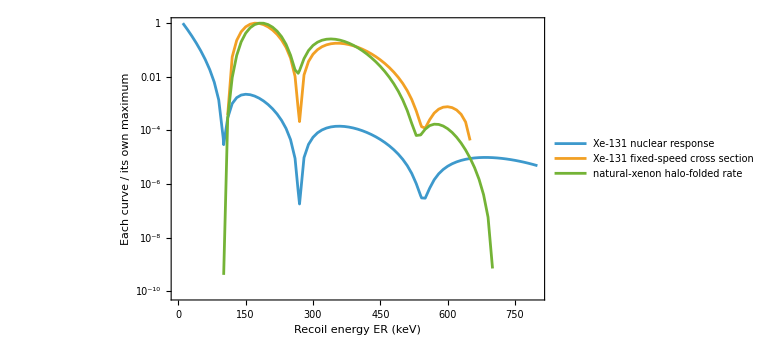

```mathematica
(* 第一条：单同位素的核响应 R_A/A.b2。 *)
nuclearShape = Table[  (* 计算单同位素核响应形状 *)
  {energy, NuclearResponse[diagnosticIsotope, energy] / diagnosticIsotope^2},  (* 读取核响应 *)
  {energy, energies}  (* 设置该循环的变量和遍历范围，或组织当前结果 *)
];  (* 结束当前参数列表、计算块或表达式 *)

(* 第二条：同一同位素、同一入射速度的微分截面。 *)
fixedSpeedShape = fixedSpeedCrossSections[[haloBenchmarkIndex]];  (* 选取相同质量组合的固定速度截面 *)

(* 第三条：同一质量组合的天然氙 halo 平均反冲率。 *)
naturalHaloShape = curvesPole[[haloBenchmarkIndex]];  (* 选取相同质量组合的天然氙 halo 率 *)

(* 三条曲线单位不同，分别按各自最大值归一化。 *)
normalizeShape[data_] := Module[{peak},  (* 定义按各自最大值归一化的函数 *)
  peak = Max[data[[All, 2]]];  (* 找出当前曲线的最大值 *)
  If[peak > 0,  (* 判断条件，根据结果执行相应分支 *)
    Select[({#[[1]], #[[2]] / peak} & /@ data), Last[#] > 0 &],  (* 筛选满足条件的数据 *)
    {}  (* 结束当前参数列表、计算块或表达式 *)
  ]  (* 结束当前参数列表、计算块或表达式 *)
];  (* 结束当前参数列表、计算块或表达式 *)
shapeCurves = normalizeShape /@ {nuclearShape, fixedSpeedShape, naturalHaloShape};  (* 分别归一化三条物理量曲线 *)
activeShapeIndices = Select[Range[3], Length[shapeCurves[[#]]] > 0 &];  (* 筛选存在正值数据的曲线 *)
shapeLabels = {  (* 设置三条曲线的图例 *)
  "Xe-131 nuclear response",  (* 结束当前参数列表、计算块或表达式 *)
  "Xe-131 fixed-speed cross section",  (* 结束当前参数列表、计算块或表达式 *)
  "natural-xenon halo-folded rate"
};  (* 结束当前参数列表、计算块或表达式 *)
(* 如修改同位素，图例自动同步。 *)
shapeLabels[[1]] = "Xe-" <> ToString[diagnosticIsotope] <> " nuclear response";  (* 将数值或表达式转换为文字 *)
shapeLabels[[2]] = "Xe-" <> ToString[diagnosticIsotope] <> " fixed-speed cross section";  (* 将数值或表达式转换为文字 *)

If[Length[activeShapeIndices] == 0,  (* 判断条件，根据结果执行相应分支 *)
  Print["当前参数下没有正值曲线。"],  (* 显示当前说明或计算结果 *)
  shapeComparisonPlot = ListLogPlot[  (* 绘制三种物理量的归一化形状对照 *)
    shapeCurves[[activeShapeIndices]],  (* 本行涉及：分别归一化三条物理量曲线；筛选存在正值数据的曲线 *)
    Joined -> True,  (* 指定该函数的参数、替换规则或显示选项 *)
    Frame -> True,  (* 设置表格边框或绘图边框 *)
    PlotRange -> All,  (* 指定该函数的参数、替换规则或显示选项 *)
    FrameLabel -> {"Recoil energy ER (keV)", "Each curve / its own maximum"},  (* 设置绘图坐标轴名称和单位 *)
    PlotLegends -> Placed[shapeLabels[[activeShapeIndices]], Below],  (* 设置曲线图例和显示位置 *)
    ImageSize -> Large  (* 指定该函数的参数、替换规则或显示选项 *)
  ];  (* 结束当前参数列表、计算块或表达式 *)
  shapeComparisonPlot  (* 传入参数：绘制三种物理量的归一化形状对照 *)
]  (* 结束当前参数列表、计算块或表达式 *)
```

所示事件率是给定晕模型和核响应下的理论核反冲率。Xe-124 和 Xe-126 未包含在 AFH 默认核响应中，七种同位素的丰度合计 0.998158；未进行丰度重新归一化。探测器效率和能量分辨率需要另行输入。

### B. FeynRules、FeynArts 与振幅核查

## 独立验证所用的内核工具

#### 独立内核运行工具

可选的 FeynRules/FeynArts 对照使用独立内核防止符号冲突。计算源代码和模型保存在第五、六、七节；运行时临时文件由笔记本生成。FeynCalc、FeynArts、FeynRules 软件包本身需要另行安装。

```mathematica
expectedModelCanonicalHash = Hash[StringTrim["M$ModelName = \"InelasticScalarRadiation\";\nM$Information = {Authors -> {\"Independent verification\"}, Version -> \"1.0\"};\nM$Parameters = {\n gX == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> \"Off-diagonal vector coupling\"},\n gS == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> \"Off-diagonal scalar coupling\"},\n gN == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> \"Pointlike nucleon vector coupling\"}\n};\nM$ClassesDescription = {\n F[1] == {ClassName -> chiOne, AntiClassName -> chiOnebar, SelfConjugate -> False, Mass -> {MChiOne,1000.}, Width -> 0, PDG -> {9000001}},\n F[2] == {ClassName -> chiTwo, AntiClassName -> chiTwobar, SelfConjugate -> False, Mass -> {MChiTwo,1000.001}, Width -> {WChiTwo,0.0001518239116}, PDG -> {9000002}},\n F[3] == {ClassName -> nuc, AntiClassName -> nucbar, SelfConjugate -> False, Mass -> {MNuc,0.938272}, Width -> 0, PDG -> {9000003}},\n V[1] == {ClassName -> med, SelfConjugate -> True, Mass -> {MMed,10.}, Width -> 0, PDG -> {9000004}},\n S[1] == {ClassName -> scal, SelfConjugate -> True, Mass -> {MScal,0.0003}, Width -> 0, PDG -> {9000005}}\n};\nLX := gX med[mu] chiTwobar.Ga[mu].chiOne;\nLS := gS scal chiTwobar.chiOne;\nLN := gN med[mu] nucbar.Ga[mu].nuc;\nLInteraction := LX + HC[LX] + LS + HC[LS] + LN;\n\n\n"], "SHA256"];
(* 从本笔记本内的程序单元读取源代码；每次运行都会读取当前内容。 *)
notebookSource[tag_String] := Module[{cells},
 cells = Cells[EvaluationNotebook[], CellTags -> tag];
 If[Length[cells] == 0, Print["Notebook source cell missing: ", tag]; Abort[]];
 StringRiffle[(First[NotebookRead[#]] &) /@ cells, "\n"]
];
(* 为避免 FeynCalc、FeynArts 和 FeynRules 的符号冲突，在临时独立内核运行；
   临时脚本的内容来自本笔记本，不读取我们原有的外部计算脚本。 *)
writeEmbeddedScript[tag_String, inRulesFolder_:False] := Module[
 {src, base, root, engineSource, niSource, modelSource, modelTemp, modelDir, hashTemp, temp},
 base = NotebookDirectory[];
 root = If[inRulesFolder, FileNameJoin[{base, "FeynRules_check"}], base];
 src = notebookSource[tag];
 engineSource = notebookSource["inlineEngine"];
 niSource = notebookSource["embeddedNI"];
 modelSource = notebookSource["embeddedModel"];
 modelTemp = CreateTemporary[] <> ".fr";
 Export[modelTemp, modelSource, "Text"];
 (* 自动导出的 FeynArts 模型也从本笔记本复制到临时目录。 *)
 modelDir = CreateDirectory[CreateTemporary[] <> "_models"];
 Export[FileNameJoin[{modelDir, "ThreeBodyVV_FA.gen"}], notebookSource["embeddedFAgen"], "Text"];
 Export[FileNameJoin[{modelDir, "ThreeBodyVV_FA.mod"}], notebookSource["embeddedFAmod"], "Text"];
 Export[FileNameJoin[{modelDir, "ChiRadiation.mod"}], notebookSource["embeddedChiFA"], "Text"];
 hashTemp = CreateTemporary[] <> ".txt";
 Export[hashTemp, "ca06a6866fc7eb34bdb8ab985f6dc2b35553dbe031e929355c84586b62b5afd6", "Text"];
 src = StringReplace[src, {
   "DirectoryName[$InputFileName]" -> ToString[InputForm[root]],
   "FileNameJoin[{workDir,\"ThreeBodyVV.fr\"}]" -> ToString[InputForm[modelTemp]],
   "FileNameJoin[{root,\"ThreeBodyVV.fr\"}]" -> ToString[InputForm[modelTemp]],
   "FileNameJoin[{workDir,\"generated_model_source_sha256.txt\"}]" -> ToString[InputForm[hashTemp]],
   "\"ThreeBodyVV_FA\"" -> ToString[InputForm[FileNameJoin[{modelDir, "ThreeBodyVV_FA"}]]],
   "\"ChiRadiation\"" -> ToString[InputForm[FileNameJoin[{modelDir, "ChiRadiation"}]]],
   "(* INSERT_NOTEBOOK_ENGINE *)" -> engineSource,
   "(* INSERT_NOTEBOOK_NINTEGRATE *)" -> StringReplace[niSource, "299792.458" -> "(299792458/1000)"]
 }];
 (* 不同系统的换行符不影响模型的物理内容；以规范化模型内容检查来源，
    同时保留导出模型时的原始 SHA256 记录检查。 *)
 src = StringReplace[src,
  "ToLowerCase[FileHash[sourceModel,\"SHA256\",\"HexString\"]]=!=StringTrim[Import[hashFile,\"Text\"]]" ->
   "(Hash[StringTrim[StringReplace[Import[sourceModel,\"Text\"],FromCharacterCode[{13,10}]->FromCharacterCode[10]]],\"SHA256\"] =!= " <>
   ToString[expectedModelCanonicalHash, InputForm] <> " || StringTrim[Import[hashFile,\"Text\"]] =!= \"ca06a6866fc7eb34bdb8ab985f6dc2b35553dbe031e929355c84586b62b5afd6\")"
 ];
 temp = CreateTemporary[] <> ".wls";
 Export[temp, src, "Text"];
 temp
];
```

#### 独立计算所用的模型与积分代码

以下代码和模型直接保存在本笔记本，供独立内核调用；FeynRules、FeynCalc、FeynArts 软件包本身仍需安装。更改模型后需要重新生成其 FeynArts 导出文件。

### FeynRules 模型与拉氏量

M$ModelName = "InelasticScalarRadiation";
M$Information = {Authors -> {"Independent verification"}, Version -> "1.0"};
M$Parameters = {
 gX == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> "Off-diagonal vector coupling"},
 gS == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> "Off-diagonal scalar coupling"},
 gN == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> "Pointlike nucleon vector coupling"}
};
M$ClassesDescription = {
 F[1] == {ClassName -> chiOne, AntiClassName -> chiOnebar, SelfConjugate -> False, Mass -> {MChiOne,1000.}, Width -> 0, PDG -> {9000001}},
 F[2] == {ClassName -> chiTwo, AntiClassName -> chiTwobar, SelfConjugate -> False, Mass -> {MChiTwo,1000.001}, Width -> {WChiTwo,0.0001518239116}, PDG -> {9000002}},
 F[3] == {ClassName -> nuc, AntiClassName -> nucbar, SelfConjugate -> False, Mass -> {MNuc,0.938272}, Width -> 0, PDG -> {9000003}},
 V[1] == {ClassName -> med, SelfConjugate -> True, Mass -> {MMed,10.}, Width -> 0, PDG -> {9000004}},
 S[1] == {ClassName -> scal, SelfConjugate -> True, Mass -> {MScal,0.0003}, Width -> 0, PDG -> {9000005}}
};
LX := gX med[mu] chiTwobar.Ga[mu].chiOne;
LS := gS scal chiTwobar.chiOne;
LN := gN med[mu] nucbar.Ga[mu].nuc;
LInteraction := LX + HC[LX] + LS + HC[LS] + LN;

### 独立相空间与 NIntegrate 源码

(* Independent construction: axes aligned with the chi1+s system momentum.
   Uses the existing trace only; no private momentum or quadrature functions. *)
ClearAll[niDot,niKinematics,niIntegrand,niI6];
niDot[a_,b_]:=a[[1]] b[[1]]-a[[2;;4]].b[[2;;4]];
niKinematics[m_?NumericQ,ms_?NumericQ,mA_?NumericQ,er_?NumericQ,v_?NumericQ,u_?NumericQ,z_?NumericQ,phi_?NumericQ]:=Module[
 {beta,e,p,q,wmin,wmax,w2,angle,qvec,pin,Q,W,Qvec,Qmag,ez,ex,ey,rad,est,kstar,ks,ks4,pp,threshold,delta},
 beta=v/299792.458;e=m/Sqrt[1-beta^2];p=e beta;q=Sqrt[er (2 mA+er)];
 wmin=(m+ms)^2;wmax=m^2+2 p q-2(e+mA)er;delta=wmax-wmin;
 If[delta<=0,Return[$Failed]];
 w2=wmin+delta u^2;
 angle=(w2-m^2+2(e+mA)er)/(2 p q);
 If[Abs[angle]>1+10^-8,Return[$Failed]];
 qvec=q {Sqrt[Max[0,1-angle^2]],0,angle};
 pin={e,0,0,p};Q=Join[{e-er},{0,0,p}-qvec];
 W=Sqrt[w2];Qvec=Q[[2;;4]];Qmag=Norm[Qvec];
 ez=If[Qmag>0,Qvec/Qmag,{0,0,1}];
 ex=Normalize[Cross[If[Abs[ez[[3]]]<0.9,{0,0,1},{0,1,0}],ez]];ey=Cross[ez,ex];
 rad=Sqrt[Max[0,(w2-(m+ms)^2)(w2-(m-ms)^2)]];
 est=(w2-m^2+ms^2)/(2 W);kstar=rad/(2 W);
 ks=kstar (z ez+Sqrt[Max[0,1-z^2]](Cos[phi] ex+Sin[phi] ey));
 ks4=Join[{(Q[[1]] est+Qvec.ks)/W},ks+Qvec (est/W+(Qvec.ks)/(W (Q[[1]]+W)))];
 pp=Q-ks4;
 <|"pin"->pin,"pout"->pp,"k"->ks4,"Q"->Q,"w2"->w2,"qvec"->qvec,
   "jac"->2 delta u,"phase"->rad/w2,"delta"->delta|>
];
niIntegrand[m_?NumericQ,ms_?NumericQ,dm_?NumericQ,mA_?NumericQ,er_?NumericQ,v_?NumericQ,width_?NumericQ,u_?NumericQ,z_?NumericQ,phi_?NumericQ]:=Module[{kin},
 kin=niKinematics[m,ms,mA,er,v,u,z,phi];
 If[kin===$Failed,Return[0.]];
 kin["jac"] kin["phase"] trace[kin["pin"],kin["pout"],kin["k"],m,m+dm,kin["w2"],width]/(2 Pi)
];
Options[niI6]={AccuracyGoal->3,PrecisionGoal->3,MaxRecursion->6};
niI6[m_?NumericQ,ms_?NumericQ,dm_?NumericQ,mA_?NumericQ,er_?NumericQ,v_?NumericQ,width_?NumericQ,OptionsPattern[]]:=Module[{b,e,p,q,wmax},
 If[!TrueQ[m>0&&ms>=0&&dm>=0&&mA>0&&er>0&&0<v<299792.458&&width>=0],Print["Invalid inputs"];Return[$Failed]];
 b=v/299792.458;e=m/Sqrt[1-b^2];p=e b;q=Sqrt[er(2mA+er)];wmax=m^2+2p q-2(e+mA)er;
 If[wmax<=(m+ms)^2,Return[0.]];
 If[wmax>=(m+dm)^2,Print["On-shell chi2 accessible; off-shell calculation aborted."];Return[$Failed]];
 NIntegrate[niIntegrand[m,ms,dm,mA,er,v,width,u,z,phi],{u,0,1},{z,-1,1},{phi,0,2Pi},
   Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->OptionValue[AccuracyGoal],
   PrecisionGoal->OptionValue[PrecisionGoal],MaxRecursion->OptionValue[MaxRecursion]]
];

### FeynArts 自动导出的通用模型

(* Patched for use with FeynCalc *)
(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)
(*                                                                               *)
(*         This file has been automatically generated by FeynRules.              *)
(*                                                                               *)
(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)



(*     Kinematic indices    *)

KinematicIndices[ F ] = {};
KinematicIndices[ V ] = {Lorentz};
KinematicIndices[ S ] = {};
KinematicIndices[ SV ] = {Lorentz};
KinematicIndices[ U ] = {};

$FermionLines = True;

(*     Simplification rules    *)

Attributes[ FAMetricTensor ] = Attributes[ FAScalarProduct ] = {Orderless}

FAFourVector/: -FAFourVector[ mom_, mu_ ] := FAFourVector[Expand[-mom], mu]

FAFourVector[ 0, _ ] = 0

SpinorType[j_Integer, ___] := MajoranaSpinor /; SelfConjugate[F[j]]

SpinorType[_Integer, __] = FADiracSpinor

(*     Generic propagators    *)

M$GenericPropagators={

(*general fermion propagator:*)

AnalyticalPropagator[External][s1 F[j1,mom]]==
FANonCommutative[SpinorType[j1][-mom,Mass[F[j1]]]],

AnalyticalPropagator[Internal][s1 F[j1,mom]]==
FANonCommutative[FADiracSlash[-mom]+Mass[F[j1]]]*
I FAPropagatorDenominator[mom,Mass[F[j1]]],

(*general vector boson propagator:*)

AnalyticalPropagator[External][s1 V[j1,mom,{li2}]]==
FAPolarizationVector[V[j1],mom,li2],

AnalyticalPropagator[Internal][s1 V[j1,mom,{li1}->{li2}]]==
-I FAPropagatorDenominator[mom,Mass[V[j1]]]*
(FAMetricTensor[li1,li2]-(1-FAGaugeXi[V[j1]])*
FAFourVector[mom,li1] FAFourVector[mom,li2]*
FAPropagatorDenominator[mom,Sqrt[FAGaugeXi[V[j1]]] Mass[V[j1]]]),

(*general mixing scalar-vector propagator:*)

AnalyticalPropagator[Internal][s1 SV[j1,mom,{li1}->{li2}]]==
I Mass[SV[j1]] FAPropagatorDenominator[mom,Mass[SV[j1]]]*
FAFourVector[mom,If[s1==1||s1==-2,li1,li2]],

(*general scalar propagator:*)

AnalyticalPropagator[External][s1 S[j1,mom]]==1,

AnalyticalPropagator[Internal][s1 S[j1,mom]]==
I FAPropagatorDenominator[mom,Sqrt[FAGaugeXi[S[j1]]] Mass[S[j1]]],

(*general Fadeev-Popov ghost propagator:*)

AnalyticalPropagator[External][s1 U[j1,mom]]==1,

AnalyticalPropagator[Internal][s1 U[j1,mom]]==
I*FAPropagatorDenominator[mom,Sqrt[FAGaugeXi[U[j1]]] Mass[U[j1]]]
}

(*     Generic couplings    *)

M$GenericCouplings = {

	 (* FFS *)

AnalyticalCoupling[s1 F[j1, mom1], s2 F[j2, mom2], s3 S[j3, mom3] ] ==
G[-1][s1 F[j1], s2 F[j2], s3 S[j3]].{FANonCommutative[FAChiralityProjector[-1]], FANonCommutative[FAChiralityProjector[+1]]},

	 (* FFV *)

AnalyticalCoupling[s1 F[j1, mom1], s2 F[j2, mom2], s3 V[j3, mom3, {li3}] ] ==
G[-1][s1 F[j1], s2 F[j2], s3 V[j3]].{FANonCommutative[FADiracMatrix[li3], FAChiralityProjector[-1] ], FANonCommutative[FADiracMatrix[li3], FAChiralityProjector[+1] ]}
}

(* FlippingRules: the flipping rules determines how Dirac
   objects change when the order of fermion fields in the
   coupling is reversed. In other words, it defines how the 
   coupling C[F, -F, ...] is derived from C[-F, F, ...].*)

M$FlippingRules = {
FANonCommutative[dm1:_FADiracMatrix | _FADiracSlash,dm2:_FADiracMatrix | _FADiracSlash, FAChiralityProjector[+1]] ->
 FANonCommutative[dm2,dm1, FAChiralityProjector[+1]],
FANonCommutative[dm1:_FADiracMatrix | _FADiracSlash,dm2:_FADiracMatrix | _FADiracSlash, FAChiralityProjector[-1]] ->
 FANonCommutative[dm2,dm1, FAChiralityProjector[-1]],
FANonCommutative[dm:_FADiracMatrix | _FADiracSlash, FAChiralityProjector[+1]] ->
-FANonCommutative[dm, FAChiralityProjector[-1]],
FANonCommutative[dm:_FADiracMatrix | _FADiracSlash, FAChiralityProjector[-1]] ->
-FANonCommutative[dm, FAChiralityProjector[+1]]}

	(* TruncationRules: rule for omitting the wave functions of
	   external Propagators defined in this file. *)

M$TruncationRules = {
  _FAPolarizationVector -> 1,
  _FADiracSpinor -> 1,
  _MajoranaSpinor -> 1 
}
	(* LastGenericRules: the very last rules that are applied to an
	   amplitude before it is returned by CreateFeynAmp. *)

M$LastGenericRules = {
  FAPolarizationVector[p_, _. mom:FourMomentum[Outgoing, _], li_] :>
    Conjugate[FAPolarizationVector][p, mom, li]
}
	(* cosmetics: *)

	(*  left spinor in chain + mom incoming -> \bar v
	    left spinor in chain + mom outgoing -> \bar u
	   right spinor in chain + mom incoming -> u
	   right spinor in chain + mom outgoing -> v *)
Format[
  FermionChain[
    FANonCommutative[_[s1_. mom1_, mass1_]],
    r___,
    FANonCommutative[_[s2_. mom2_, mass2_]]] ] :=
  Overscript[If[FreeQ[mom1, Incoming], "u", "v"], "_"][mom1, mass1] .
    r . If[FreeQ[mom2, Outgoing], "u", "v"][mom2, mass2]

Format[ FADiracSlash ] = "gs"

Format[ FADiracMatrix ] = "ga"

Format[ FAChiralityProjector[1] ] = SequenceForm["om", Subscript["+"]]

Format[ FAChiralityProjector[-1] ] = SequenceForm["om", Subscript["-"]]

Format[ FAGaugeXi[a_] ] := SequenceForm["xi", Subscript[a]]

Format[ FAPolarizationVector ] = "ep"

Unprotect[Conjugate];
Format[ Conjugate[a_] ] = SequenceForm[a, Superscript["*"]];
Protect[Conjugate]

Format[ FAMetricTensor ] = "g"

Format[ FAScalarProduct[a__] ] := Dot[a]

Format[ FAFourVector[a_, b_] ] := a[b]

### FeynArts 自动导出的场和顶角

(* Patched for use with FeynCalc *)
(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)
(*                                                                             *)
(*         This file has been automatically generated by FeynRules.            *)
(*                                                                             *)
(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)


FR$ModelInformation={
  ModelName->"InelasticScalarRadiation",
  Authors -> {"Independent verification"},
  Version -> "1.0"};

FR$ClassesTranslation={};

FR$InteractionOrderPerturbativeExpansion={{NP, 0}};

FR$GoldstoneList={};

(*     Declared indices    *)

(*     Declared particles    *)

M$ClassesDescription = {
F[1] == {
    SelfConjugate -> False,
    PropagatorLabel -> chiOne,
    PropagatorType -> Straight,
    PropagatorArrow -> Forward,
    Mass -> MChiOne,
    Indices -> {} },

F[2] == {
    SelfConjugate -> False,
    PropagatorLabel -> chiTwo,
    PropagatorType -> Straight,
    PropagatorArrow -> Forward,
    Mass -> MChiTwo,
    Indices -> {} },

F[3] == {
    SelfConjugate -> False,
    PropagatorLabel -> nuc,
    PropagatorType -> Straight,
    PropagatorArrow -> Forward,
    Mass -> MNuc,
    Indices -> {} },

V[1] == {
    SelfConjugate -> True,
    PropagatorLabel -> med,
    PropagatorType -> Sine,
    PropagatorArrow -> None,
    Mass -> MMed,
    Indices -> {} },

S[1] == {
    SelfConjugate -> True,
    PropagatorLabel -> scal,
    PropagatorType -> ScalarDash,
    PropagatorArrow -> None,
    Mass -> MScal,
    Indices -> {} }
}


(*        Definitions       *)


MChiOne[ ___ ] := MChiOne;
MChiTwo[ ___ ] := MChiTwo;
MNuc[ ___ ] := MNuc;
MMed[ ___ ] := MMed;
MScal[ ___ ] := MScal;




(*      Couplings (calculated by FeynRules)      *)

M$CouplingMatrices = {

C[ -F[1] , F[2] , S[1] ] == {{I*gc1, 0}, {I*gc1, 0}},

C[ -F[2] , F[1] , S[1] ] == {{I*gc2, 0}, {I*gc2, 0}},

C[ -F[1] , F[2] , V[1] ] == {{I*gc3, 0}, {I*gc3, 0}},

C[ -F[2] , F[1] , V[1] ] == {{I*gc4, 0}, {I*gc4, 0}},

C[ -F[3] , F[3] , V[1] ] == {{I*gc5, 0}, {I*gc5, 0}}

}

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

(* Parameter replacement lists (These lists were created by FeynRules) *)

(* FA Couplings *)

M$FACouplings = {
     gc1 -> gS,
     gc2 -> gS,
     gc3 -> gX,
     gc4 -> gX,
     gc5 -> gN};

### FeynArts 暗物质辐射模型

M$ClassesDescription = {
 F[1] == {SelfConjugate->False, Mass->Mchi1, PropagatorLabel->"chi1", PropagatorType->Straight, PropagatorArrow->Forward},
 F[2] == {SelfConjugate->False, Mass->Mchi2, PropagatorLabel->"chi2", PropagatorType->Straight, PropagatorArrow->Forward},
 V[1] == {SelfConjugate->True, Mass->MV, PropagatorLabel->"V", PropagatorType->Sine, PropagatorArrow->None},
 S[1] == {SelfConjugate->True, Mass->MS, PropagatorLabel->"s", PropagatorType->Dashes, PropagatorArrow->None}
};
M$CouplingMatrices = {
 C[-F[2],F[1],V[1]] == I gv {{1},{1}},
 C[-F[1],F[2],V[1]] == I gv {{1},{1}},
 C[-F[2],F[1],S[1]] == I gs {{1},{1}},
 C[-F[1],F[2],S[1]] == I gs {{1},{1}}
};
M$LastModelRules = {};

#### FeynRules：从拉氏量推导费曼顶角

本节使用 FeynRules 独立内核读取 本笔记本内的 FeynRules 模型单元，以原稿的非对角矢量耦合 g1 和实标量耦合 g2 推导费曼规则。gX 对应 g1，gS 对应 g2；gN 是用来检查顶角的点状 Dirac 核子矢量耦合。AFH 氙核响应没有被视作点状核子。

拉氏量取实耦合、Dirac chi1 和 chi2、实标量及中性矢量：gX V_mu chibar2 gamma^mu chi1 + gS s chibar2 chi1 + h.c. + gN V_mu Nbar gamma^mu N。程序自动进行厄米共轭检查，结果 0 个剩余顶角表示该相互作用在当前定义下通过检查。

### 5A.1 检查模型文件

```mathematica
Print[notebookSource["embeddedModel"]];  (* 显示本笔记本内的模型代码 *)
```

M$ModelName = "InelasticScalarRadiation";
M$Information = {Authors -> {"Independent verification"}, Version -> "1.0"};
M$Parameters = {
 gX == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> "Off-diagonal vector coupling"},
 gS == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> "Off-diagonal scalar coupling"},
 gN == {ParameterType -> External, ComplexParameter -> False, Value -> 1.0, InteractionOrder -> {NP,1}, Description -> "Pointlike nucleon vector coupling"}
};
M$ClassesDescription = {
 F[1] == {ClassName -> chiOne, AntiClassName -> chiOnebar, SelfConjugate -> False, Mass -> {MChiOne,1000.}, Width -> 0, PDG -> {9000001}},
 F[2] == {ClassName -> chiTwo, AntiClassName -> chiTwobar, SelfConjugate -> False, Mass -> {MChiTwo,1000.001}, Width -> {WChiTwo,0.0001518239116}, PDG -> {9000002}},
 F[3] == {ClassName -> nuc, AntiClassName -> nucbar, SelfConjugate -> False, Mass -> {MNuc,0.938272}, Width -> 0, PDG -> {9000003}},
 V[1] == {ClassName -> med, SelfConjugate -> True, Mass -> {MMed,10.}, Width -> 0, PDG -> {9000004}},
 S[1] == {ClassName -> scal, SelfConjugate -> True, Mass -> {MScal,0.0003}, Width -> 0, PDG -> {9000005}}
};
LX := gX med[mu] chiTwobar.Ga[mu].chiOne;
LS := gS scal chiTwobar.chiOne;
LN := gN med[mu] nucbar.Ga[mu].nuc;
LInteraction := LX + HC[LX] + LS + HC[LS] + LN;

### 5A.2 运行 FeynRules 并检查顶角

预期有两条标量顶角 i gS、两条非对角矢量顶角 i gX gamma^mu、一个核子矢量顶角 i gN gamma^mu。它们与第六节 FeynArts 模型中的 gs、gv 顶角一致；整体 i 因子和费米子链顺序需沿用统一约定。

#### 本节计算源代码：FeynRules：根据拉氏量推导顶角

下面的代码直接保存在本笔记本，可展开阅读或编辑；执行其后的运行单元时，将在独立内核中使用这里的代码。

root=DirectoryName[$InputFileName];
base=FileNameJoin[{root,"feynrules-current"}];
$FeynRulesPath=base;FR$Parallel=False;FeynRules`MatrixSymbol;
Get[FileNameJoin[{base,"FeynRules.m"}]];
SetDirectory[root];
LoadModel[FileNameJoin[{root,"ThreeBodyVV.fr"}]];
Print["LAGRANGIAN: ",ToString[InputForm[LInteraction],PageWidth->Infinity]];
rules=FeynmanRules[LInteraction];
Print["RULE COUNT: ",Length[rules]];
Print["RULES: ",ToString[InputForm[rules],PageWidth->Infinity]];
scalar=Select[rules,!FreeQ[#[[2]],gS]&];vector=Select[rules,!FreeQ[#[[2]],gX]&];nuclear=Select[rules,!FreeQ[#[[2]],gN]&];
Print["SCALAR, VECTOR, NUCLEON COUNTS: ",{Length[scalar],Length[vector],Length[nuclear]}];
Print["SCALAR STRUCTURE OK: ",And@@(FreeQ[#[[2]],Ga]&&!FreeQ[#[[2]],IndexDelta]& /@ scalar)];
Print["VECTOR STRUCTURE OK: ",And@@(!FreeQ[#[[2]],Ga]& /@ Join[vector,nuclear])];
Print["SCALAR COEFFICIENTS: ",ToString[InputForm[Simplify[#[[2]]/(I*gS)]& /@ scalar]]];
Print["VECTOR COEFFICIENTS: ",ToString[InputForm[Simplify[#[[2]]/(I*gX)]& /@ vector]]];
hermiticity=CheckHermiticity[LInteraction];
Print["HERMITICITY RESULT: ",ToString[InputForm[hermiticity]]];
Export[FileNameJoin[{root,"feynrules_derived_rules.txt"}],ToString[InputForm[rules],PageWidth->Infinity],"Text"];
scalarOK=And@@(FreeQ[#[[2]],Ga]&&!FreeQ[#[[2]],IndexDelta]& /@ scalar);
vectorOK=And@@(!FreeQ[#[[2]],Ga]& /@ Join[vector,nuclear]);
If[Length[rules]!=5||Length[scalar]!=2||Length[vector]!=2||Length[nuclear]!=1||!TrueQ[scalarOK]||!TrueQ[vectorOK]||hermiticity=!={},Exit[2]];
Print["CHECK: PASS"];Exit[0];

```mathematica
Clear[feynRulesRun]; (* 清除上次验证输出，避免把旧结果当作本次结果 *)
(* 通过独立内核运行 FeynRules，避免与本笔记本的 FeynCalc 符号冲突。 *)
feynRulesDirectory = FileNameJoin[{NotebookDirectory[], "FeynRules_check"}]; (* 模型和程序目录 *)
feynRulesScript = writeEmbeddedScript["embeddedRules", True]; (* 顶角推导脚本 *)
feynRulesExecutable = SelectFirst[FileNameJoin[{#, If[$OperatingSystem === "Windows", "wolframscript.exe", "wolframscript"]}] & /@ StringSplit[Environment["PATH"], If[$OperatingSystem === "Windows", ";", ":"]], FileExistsQ, $Failed]; (* 查找 Mathematica 脚本程序 *)
If[feynRulesExecutable === $Failed || !FileExistsQ[feynRulesScript], (* 检查运行依赖 *)
 Print["未找到 wolframscript 或 FeynRules 脚本，请检查完整文件包。"], (* 缺少文件时给出提示 *)
 feynRulesRun = RunProcess[{feynRulesExecutable, "-file", feynRulesScript}]; (* 推导费曼规则并检查厄米性 *)
 Print[feynRulesRun["StandardOutput"]]; (* 显示五个顶角及检查结果 *)
 If[feynRulesRun["StandardError"] =!= "", Print[feynRulesRun["StandardError"]]]; (* 显示可能的警告 *)
 Print["执行退出码：", feynRulesRun["ExitCode"]] (* 0 表示脚本检查通过 *)
]
```

- FeynRules - \r
Version: 2.3.49 (*29 September 2021).\r
Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks\r
 \r
Please cite:\r
    - Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);\r
    - Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).\r
 \r
http://feynrules.phys.ucl.ac.be\r
 \r
The FeynRules palette can be opened using the command FRPalette[].\r
This model implementation was created by\r
Independent verification\r
Model Version: 1.0\r
For more information, type ModelInformation[].\r
\r
   - Loading particle classes.\r
   - Loading parameter classes.\r
\r
Model InelasticScalarRadiation loaded.\r
LAGRANGIAN: gS*scal*chiOnebar . chiTwo + gS*scal*chiTwobar . chiOne + gX*chiOnebar . Ga[mu] . chiTwo*med[mu] + gX*chiTwobar . Ga[mu] . chiOne*med[mu] + gN*nucbar . Ga[mu] . nuc*med[mu]\r
Starting Feynman rule calculation.\r
Expanding the Lagrangian...\r
Collecting the different structures that enter the vertex.\r
5 possible non-zero vertices have been found -> starting the computation: Dynamic[FR$FeynmanRules] / 5.\r
5 vertices obtained.\r
RULE COUNT: 5\r
RULES: {{{{chiOnebar, 1}, {chiTwo, 2}, {scal, 3}}, I*gS*IndexDelta[Index[Spin, Ext[1]], Index[Spin, Ext[2]]]}, {{{chiTwobar, 1}, {chiOne, 2}, {scal, 3}}, I*gS*IndexDelta[Index[Spin, Ext[1]], Index[Spin, Ext[2]]]}, {{{chiOnebar, 1}, {chiTwo, 2}, {med, 3}}, I*gX*Ga[Index[Lorentz, Ext[3]], Index[Spin, Ext[1]], Index[Spin, Ext[2]]]}, {{{chiTwobar, 1}, {chiOne, 2}, {med, 3}}, I*gX*Ga[Index[Lorentz, Ext[3]], Index[Spin, Ext[1]], Index[Spin, Ext[2]]]}, {{{nucbar, 1}, {nuc, 2}, {med, 3}}, I*gN*Ga[Index[Lorentz, Ext[3]], Index[Spin, Ext[1]], Index[Spin, Ext[2]]]}}\r
SCALAR, VECTOR, NUCLEON COUNTS: {2, 2, 1}\r
SCALAR STRUCTURE OK: True\r
VECTOR STRUCTURE OK: True\r
SCALAR COEFFICIENTS: {IndexDelta[Index[Spin, Ext[1]], Index[Spin, Ext[2]]], IndexDelta[Index[Spin, Ext[1]], Index[Spin, Ext[2]]]}\r
VECTOR COEFFICIENTS: {Ga[Index[Lorentz, Ext[3]], Index[Spin, Ext[1]], Index[Spin, Ext[2]]], Ga[Index[Lorentz, Ext[3]], Index[Spin, Ext[1]], Index[Spin, Ext[2]]]}\r
Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].\r
If the lagrangian is hermitian, then the number of vertices should be zero.\r
Starting Feynman rule calculation.\r
Expanding the Lagrangian...\r
No vertices found.\r
0 vertices obtained.\r
The lagrangian is hermitian.\r
HERMITICITY RESULT: {}\r
CHECK: PASS\r

执行退出码：0

FeynRules 顶角输出写入 FeynRules_check/feynrules_derived_rules.txt。这里的 N 是点状 Dirac 靶，不包含 AFH 氙核响应；下面另有 FeynArts→FeynCalc 的点状靶数值计算。已导出的 UFO 是否能用于独立的 MadGraph 截面对照，需要另行运行并核对传播子宽度，不能由 UFO 文件存在推断已验证。

## FeynArts 自动生成图与振幅对照

### 完整 2→3 过程的费曼图

图中 chiOne = χ1，chiTwo = χ2，med = 矢量媒介 V，scal = 标量 s，nuc = 点状靶 N。实线表示费米子，波浪线表示矢量媒介，虚线表示标量。

运行下面单元，在独立 Mathematica 内核使用本笔记本内的 FeynRules 导出模型生成 χ1 + N → χ1 + N + s 的两张树图。N 是点状自旋 1/2 靶；核结构和 AFH 核响应在主计算中另行加入。图只展示拓扑，数值一致性要看后面的对照。

base=DirectoryName[$InputFileName];
faDir=FileNameJoin[{base,"feynarts","FeynArts-3.12"}];
If[!FileExistsQ[FileNameJoin[{faDir,"FeynArts.m"}]],Print["ERROR: FeynArts missing: ",faDir];Exit[1]];
AppendTo[$Path,faDir];Get["FeynArts`"];
$FAVerbose=0;
top=CreateTopologies[0,2->3,ExcludeTopologies->{Tadpoles,SelfEnergies}];
ins=InsertFields[top,{F[1],F[3]}->{F[1],F[3],S[1]},Model->"ThreeBodyVV_FA",GenericModel->"ThreeBodyVV_FA",InsertionLevel->{Classes}];
Print["Number of 2->3 diagrams: ",Length[ins]];
If[Length[ins]!=2,Print["ERROR: expected 2 diagrams"];Exit[2]];
Paint[ins,ColumnsXRows->{2,1},SheetHeader->None];
FeynArts`Graphics`LabelFontSize=0.7;
result=Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{900,450}];
outputPath=Last[$ScriptCommandLine];
Export[outputPath,result,"PNG"];
If[!FileExistsQ[outputPath],Print["ERROR: diagram export failed"];Exit[3]];
Print["DIAGRAM_EXPORT_OK"];Exit[0];

```mathematica
Clear[faDiagramRun]; (* 清除上次费曼图检查状态 *)
(* 运行前需要完成前面的独立内核工具定义，以及本机 FeynArts 安装检查。 *)
faDiagramScript = writeEmbeddedScript["embeddedFAFullPaint", False]; (* 将笔记本内的绘图脚本和模型写到临时目录 *)
faExecutable = SelectFirst[FileNameJoin[{#, If[$OperatingSystem === "Windows", "wolframscript.exe", "wolframscript"]}] & /@ StringSplit[Environment["PATH"], If[$OperatingSystem === "Windows", ";", ":"]], FileExistsQ, $Failed]; (* 寻找 Mathematica 命令行内核 *)
If[faExecutable === $Failed, Print["未找到 wolframscript，无法运行 FeynArts 图形计算。"], (* 找不到时显示原因 *)
 faDiagramFile = CreateTemporary[] <> ".png"; (* 图像写入临时文件，避免覆盖已有文件 *)
 faDiagramRun = RunProcess[{faExecutable, "-file", faDiagramScript, faDiagramFile}]; (* 独立内核生成完整 2→3 图 *)
 Print["FeynArts 退出码：", faDiagramRun["ExitCode"]]; (* 显示运行状态 *)
 Print[faDiagramRun["StandardOutput"]]; (* 显示拓扑数和程序信息 *)
 If[faDiagramRun["StandardError"] =!= "", Print[faDiagramRun["StandardError"]]]; (* 显示错误输出 *)
 If[faDiagramRun["ExitCode"] === 0 && FileExistsQ[faDiagramFile], Print[Import[faDiagramFile]], Print["未能生成费曼图；请检查上面的错误信息。"]]; (* 显示真实生成的图像 *)
];
```

FeynArts 退出码：0

\r
FeynArts 3.12 (27 Mar 2025)\r
by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn\r
Number of 2->3 diagrams: 2\r
DIAGRAM_EXPORT_OK\r

-Graphics-

本节用 FeynArts 自动生成子过程 chi1 + V* -> chi1 + s 的树图。V* 代表与核交换的虚矢量媒介；核电流、V 传播子及核响应仍按前面的核散射公式处理。模型文件将 chi1、chi2 设为 Dirac 费米子，s 和 V 设为实中性场，并显式定义非对角标量与矢量顶角。

本节在独立 Wolfram 内核运行原版 FeynArts，以减少与主内核 FeynCalc 的符号冲突。运行时从笔记本内嵌模型写出临时文件；本地 feynarts/FeynArts-3.12/Models/ChiRadiation.mod 可供参考，但并非本单元唯一的模型来源。请先运行后文的独立内核工具和模型源码单元。

### 6.1 自动生成并列出费曼振幅

请运行下方输入单元。它创建 2→2 树级拓扑，插入指定外线与模型，输出实际插入的图数及 FeynArts 原始振幅。示例应得到两张图；输出使用 FeynArts 的动量和 Dirac 链记号。

#### 本节计算源代码：FeynArts：生成费曼图

下面的代码直接保存在本笔记本，可展开阅读或编辑；执行其后的运行单元时，将在独立内核中使用这里的代码。

(* Run in a separate kernel: original FeynArts and FeynCalc export overlapping names. *)
base = DirectoryName[$InputFileName];
faDir = FileNameJoin[{base,"feynarts","FeynArts-3.12"}];
If[!FileExistsQ[FileNameJoin[{faDir,"FeynArts.m"}]],Print["FeynArts missing: ",faDir];Exit[1]];
AppendTo[$Path,faDir];
Get["FeynArts`"];
topologies=CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles,SelfEnergies}];
diagrams=InsertFields[topologies,{F[1],V[1]}->{F[1],S[1]},
 Model->"ChiRadiation",InsertionLevel->{Classes}];
amplitudes=CreateFeynAmp[diagrams,Truncated->True];
Print["Number of inserted diagrams: ",Length[diagrams]];
Print["Number of amplitudes: ",Length[amplitudes]];
Print["Amplitudes (FeynArts notation):"];
Print[ToString[InputForm[amplitudes],PageWidth->Infinity]];
If[Length[diagrams]!=2||Length[amplitudes]!=2,Exit[2]];
Exit[0];

```mathematica
(* 单独启动 Mathematica 内核，避免 FeynArts 与 FeynCalc 同名符号冲突。 *)
feynArtsScript = writeEmbeddedScript["embeddedFA", False];  (* 定位 FeynArts 自动生成图的脚本 *)
feynArtsKernel = SelectFirst[FileNameJoin[{#, If[$OperatingSystem === "Windows", "wolframscript.exe", "wolframscript"]}] & /@ StringSplit[Environment["PATH"], If[$OperatingSystem === "Windows", ";", ":"]], FileExistsQ, $Failed];  (* 查找 Wolfram 命令行程序 *)
If[!FileExistsQ[feynArtsScript] || feynArtsKernel === $Failed,  (* 判断条件，根据结果执行相应分支 *)
  Print["找不到 FeynArts 对照脚本或 wolframscript，请检查完整文件包。"],  (* 显示当前说明或计算结果 *)
  feynArtsRun = RunProcess[{feynArtsKernel, "-file", feynArtsScript}];  (* 在独立内核中运行 FeynArts 并保存输出 *)
  Print[feynArtsRun["StandardOutput"]];  (* 显示当前说明或计算结果 *)
  If[feynArtsRun["StandardError"] =!= "", Print[feynArtsRun["StandardError"]]];  (* 判断条件，根据结果执行相应分支 *)
  Print["执行退出码：", feynArtsRun["ExitCode"]]  (* 显示当前说明或计算结果 *)
]  (* 结束当前参数列表、计算块或表达式 *)
```

\r
FeynArts 3.12 (27 Mar 2025)\r
by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn\r
\r
loading generic model file C:\Users\local-user\Documents\ChatGPT\3 body HDM\天然氙三体散射\feynarts\FeynArts-3.12\Models\Lorentz.gen\r
> $GenericMixing is OFF\r
generic model {Lorentz} initialized\r
\r
loading classes model file C:\Users\local-user\AppData\Local\Temp\m-04a919d9-bf85-4fdd-bcb1-4a9895a431d7_models\ChiRadiation.mod\r
> 6 particles (incl. antiparticles) in 4 classes\r
> $CounterTerms are ON\r
> 4 vertices\r
classes model {C:\Users\local-user\AppData\Local\Temp\m-04a919d9-bf85-4fdd-bcb1-4a9895a431d7_models\ChiRadiation} initialized\r
\r
inserting at level(s) {Classes}\r
> Top. 1: 0 Classes insertions\r
> Top. 2: 1 Classes insertion\r
> Top. 3: 0 Classes insertions\r
> Top. 4: 1 Classes insertion\r
in total: 2 Classes insertions\r
\r
creating amplitudes at level(s) {Classes}\r
> Top. 1: 1 Classes amplitude\r
> Top. 2: 1 Classes amplitude\r
in total: 2 Classes amplitudes\r
Number of inserted diagrams: 2\r
Number of amplitudes: 2\r
Amplitudes (FeynArts notation):\r
FeynAmpList[Process -> {{F[1], FourMomentum[Incoming, 1], Mchi1, {}}, {V[1], FourMomentum[Incoming, 2], MV, {}}} -> {{F[1], FourMomentum[Outgoing, 1], Mchi1, {}}, {S[1], FourMomentum[Outgoing, 2], MS, {}}}, Model -> {"C:\\Users\\local-user\\AppData\\Local\\Temp\\m-04a919d9-bf85-4fdd-bcb1-4a9895a431d7_models\\ChiRadiation"}, GenericModel -> {"Lorentz"}, AmplitudeLevel -> {Classes}, ExcludeParticles -> {}, ExcludeFieldPoints -> {}, LastSelections -> {}][FeynAmp[GraphID[Topology == 1, Generic == 1, Classes == 1, Number == 1], Integral[], FermionChain[I*gs*NonCommutative[ChiralityProjector[-1]] + I*gs*NonCommutative[ChiralityProjector[1]], NonCommutative[Mchi2 + DiracSlash[FourMomentum[Outgoing, 1] + FourMomentum[Outgoing, 2]]], I*gv*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[-1]] + I*gv*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[1]]]*PropagatorDenominator[-FourMomentum[Outgoing, 1] - FourMomentum[Outgoing, 2], Mchi2]], FeynAmp[GraphID[Topology == 2, Generic == 1, Classes == 1, Number == 2], Integral[], FermionChain[I*gv*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[-1]] + I*gv*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[1]], NonCommutative[Mchi2 + DiracSlash[-FourMomentum[Incoming, 2] + FourMomentum[Outgoing, 1]]], I*gs*NonCommutative[ChiralityProjector[-1]] + I*gs*NonCommutative[ChiralityProjector[1]]]*PropagatorDenominator[FourMomentum[Incoming, 2] - FourMomentum[Outgoing, 1], Mchi2]]]\r

执行退出码：0

### 6.2 与 FeynCalc 手写振幅逐项对应

约定入射暗物质动量为 p，出射为 p-prime，标量为 k，入射虚矢量动量为 qV=p-prime+k-p。FeynArts 第一项的内部动量为 p-prime+k，对应 (slash p-prime + slash k + m2) gamma^mu；第二项为 p-prime-qV=p-k，对应 gamma^mu (slash p - slash k + m2)。这正是第五节的两条 Dirac 链，两个手性投影之和为 1。第五节取 mu=0。

FeynArts 输出的共同顶角因子及外线约定需在完整振幅中统一处理。这里的自动生成对照检查图数、内部粒子、动量流向和两条 Dirac 链；第七节进一步读取振幅结构进行逐点数值比较；这一转换使用手写数值代入规则，并未使用 FCFAConvert 自动转换。FeynArts 输出的树图振幅未加入自能宽度；后续数值对照时会显式加入极点宽度。

#### FeynArts 振幅与积分数值一致性检查

本节在独立 Mathematica 内核中读取 FeynArts 生成的两条费米子链和传播子，用模型给出的标量/矢量顶角、四维 Dirac 矩阵和动量守恒代入数值。去掉两顶角共同相位后，先逐张图比较矩阵，再比较两图相干相加的自旋迹和完整 I6。

数值对照按主计算的处方，在 p-prime+k 传播子中加入 i m2 Gamma；另一张图沿用原程序分母。极点宽度按当前 g2 和质量计算。

运行本节前，请先运行笔记本第一至第三节。脚本使用 1.4 节的质量、反冲能量、速度和第二节的积分阶数；原实现和 FeynArts 使用完全相同的运动学和积分节点。

#### 本节计算源代码：FeynArts：振幅与积分对照

下面的代码直接保存在本笔记本，可展开阅读或编辑；执行其后的运行单元时，将在独立内核中使用这里的代码。

base=DirectoryName[$InputFileName]; AppendTo[$Path,FileNameJoin[{base,"feynarts","FeynArts-3.12"}]];
Get["FeynArts`"]

top=CreateTopologies[0,2->2,ExcludeTopologies->{Tadpoles,SelfEnergies}];
ins=InsertFields[top,{F[1],V[1]}->{F[1],S[1]},Model->"ChiRadiation",InsertionLevel->{Classes}];
amp=CreateFeynAmp[ins,Truncated->True];
(* INSERT_NOTEBOOK_ENGINE *)
terms=List@@amp;
Print["amp terms ",Length[terms]];
chains=Cases[terms,FermionChain[a_,b_,c_]:>{a,b,c},Infinity];
dens=Cases[terms,PropagatorDenominator[a_,Mchi2]:>a,Infinity];
Print["chains ",Length[chains]," dens ",Length[dens]];
Print["chain1 ",ToString[InputForm[chains[[1]]]]];
Print["den1 ",ToString[InputForm[dens[[1]]]]];
If[Length[chains]!=2||Length[dens]!=2,Exit[1]];
Clear[faNumericTrace,faPieces];
faPieces[pin_,pp_,k_,m2_,width_]:=Module[{qv,vectors,mom,vert,parts,den,vals},
 qv=pp+k-pin;
 vectors={FourMomentum[Incoming,1]->pin,FourMomentum[Incoming,2]->qv,
          FourMomentum[Outgoing,1]->pp,FourMomentum[Outgoing,2]->k};
 mom[x_]:=x/.vectors;
 vert[x_]:=x/.{
   HoldPattern[NonCommutative[ChiralityProjector[_]]] :> id/2,
   HoldPattern[NonCommutative[DiracMatrix[Index[Lorentz,1]],ChiralityProjector[_]]] :> g0/2,
   HoldPattern[NonCommutative[Mchi2+DiracSlash[t_]]] :> (m2 id+slash[mom[t]]),
   gs->1,gv->1};
 parts=Map[vert,chains,{2}];
 den=Table[mdot[mom[dens[[i]]],mom[dens[[i]]]]-m2^2+If[i==1,I m2 width,0],{i,2}];
 vals=Table[Dot@@parts[[i]]/den[[i]],{i,2}];
 (* Each FeynArts vertex contributes i; remove their common -1 phase. *)
 -vals
];
faNumericTrace[pin_,pp_,k_,m_,m2_,w2_,width_]:=Module[{g,bar},
 g=Total[faPieces[pin,pp,k,m2,width]];bar=g0.ConjugateTranspose[g].g0;
 Re[Tr[(slash[pp]+m id).g.(slash[pin]+m id).bar]]/2];
args=Rest[$ScriptCommandLine];
If[Length[args]==10,
 {m,ms,dm,mA,er,v,nw,nz,np,g2input}=ToExpression /@ args;ord={nw,nz,np},
 m=1000.;ms=.0003;dm=.001;mA=131*.93149410242;er=.0002;v=776.;ord={6,6,4};g2input=1.];
pole=Chi2Width[m,ms,dm,g2input];
samples=Reap[Block[{trace=Function[{p,r,k,m1,m2,w,g},Sow[{p,r,k,m1,m2,w,g}];0.]},I6[m,ms,dm,mA,er,v,{2,2,2},pole]]][[2,1]];
sample=First[samples];{pin,pp,k,m1,m2,w2,width}=sample;
fa=faPieces[pin,pp,k,m2,width];
ref={ (slash[pp+k]+m2 id).g0/(w2-m2^2+I m2 width),
 g0.(slash[pin-k]+m2 id)/(mdot[pin-k,pin-k]-m2^2)};
Print["amplitude relative matrix norms: ",Table[Norm[Flatten[fa[[i]]-ref[[i]]]]/Norm[Flatten[ref[[i]]]],{i,2}]];
t0=trace@@sample;t1=faNumericTrace@@sample;
Print["trace original=",t0," FA=",t1," relative=",t1/t0-1];
Do[
 original=I6[m,ms,dm,mA,er,v,ord,width];
 generated=Block[{trace=faNumericTrace},I6[m,ms,dm,mA,er,v,ord,width]];
 Print["width=",width," original I6=",original," FA I6=",generated," relative=",generated/original-1],
 {width,{pole}}];
Print["FA_DATA:",ExportString[N[{t0,t1,original,generated},16],"RawJSON","Compact"->True]];

```mathematica
Clear[faCheckResult,faData,faDataLines]; (* 清除上次 FeynArts 振幅对照状态 *)
(* 调用独立内核，传入当前已选择的质量、能量、速度、阶数和 g2。 *)
faCheckScript = writeEmbeddedScript["embeddedFANumeric", False];  (* 定位 FeynArts 数值对照脚本 *)
faCheckExecutable = SelectFirst[FileNameJoin[{#, If[$OperatingSystem === "Windows", "wolframscript.exe", "wolframscript"]}] & /@ StringSplit[Environment["PATH"], If[$OperatingSystem === "Windows", ";", ":"]], FileExistsQ, $Failed];  (* 查找执行对照所需的 Wolfram 程序 *)
faCheckInputs = Join[{  (* 收集当前质量、反冲能量、速度及积分阶数 *)
  darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV,  (* 本行涉及：输入暗物质 chi1 质量，单位 GeV；选择并换算标量质量为 GeV；选择并换算质量劈裂为 GeV *)
  selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS  (* 本行涉及：设置检查用入射速度 km/s；用 A 乘原子质量单位近似核质量；将反冲能量换算为 GeV *)
}, gaussCheckOrders, {g2val}];  (* 组织当前列表、函数参数或计算块 *)
If[!FileExistsQ[faCheckScript] || faCheckExecutable === $Failed ||  (* 判断条件，根据结果执行相应分支 *)
   !And @@ (NumericQ /@ faCheckInputs),  (* 继续检查输入条件或数值有效性 *)
  Print["请先运行第一至第三节，并检查 FeynArts 文件和 wolframscript。"],  (* 显示当前说明或计算结果 *)
  faCheckResult = RunProcess[Join[{faCheckExecutable, "-file", faCheckScript},  (* 执行 FeynArts 振幅与积分的数值对照 *)
    ToString[#, InputForm] & /@ faCheckInputs]];  (* 将数值或表达式转换为文字 *)
  Print[faCheckResult["StandardOutput"]];  (* 显示当前说明或计算结果 *)
  If[faCheckResult["StandardError"] =!= "", Print[faCheckResult["StandardError"]]];  (* 判断条件，根据结果执行相应分支 *)
  Print["执行退出码：", faCheckResult["ExitCode"]]  (* 显示当前说明或计算结果 *)
]  (* 结束当前参数列表、计算块或表达式 *)
If[ValueQ[faCheckResult] && faCheckResult["ExitCode"] === 0,
 faDataLines = StringCases[faCheckResult["StandardOutput"], RegularExpression["FA_DATA:([^\\r\\n]+)"] -> "$1"]; (* 提取子内核输出的 JSON 数据 *)
 If[Length[faDataLines] == 1,
  faData = Quiet[Check[ImportString[First[faDataLines],"RawJSON"],$Failed]]; (* 读取手写和 FeynArts 的对照值 *)
  If[ListQ[faData] && Length[faData] == 4, Print[Grid[{{"检查项","手写矩阵","FeynArts","相对差"},{"单个相空间点的自旋迹",faData[[1]],faData[[2]],If[faData[[1]]!=0,faData[[2]]/faData[[1]]-1,Indeterminate]},{"Gauss I6 (GeV.b2)",faData[[3]],faData[[4]],If[faData[[3]]!=0,faData[[4]]/faData[[3]]-1,Indeterminate]}},Frame->All]]; Print["两条计算共用相空间映射、积分节点和宽度；该对照检查振幅与自旋迹，不单独证明核响应或整个积分实现。"], Print["FeynArts 数值结果格式无效，请查看上方日志。"]],
  Print["未找到 FeynArts 数值结果；请查看上方日志或检查相空间是否关闭。"]]];
```

\r
FeynArts 3.12 (27 Mar 2025)\r
by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn\r
\r
loading generic model file C:\Users\local-user\Documents\ChatGPT\3 body HDM\天然氙三体散射\feynarts\FeynArts-3.12\Models\Lorentz.gen\r
> $GenericMixing is OFF\r
generic model {Lorentz} initialized\r
\r
loading classes model file C:\Users\local-user\AppData\Local\Temp\m-e25d0d18-43c9-453c-97b9-8588be96ac0b_models\ChiRadiation.mod\r
> 6 particles (incl. antiparticles) in 4 classes\r
> $CounterTerms are ON\r
> 4 vertices\r
classes model {C:\Users\local-user\AppData\Local\Temp\m-e25d0d18-43c9-453c-97b9-8588be96ac0b_models\ChiRadiation} initialized\r
\r
inserting at level(s) {Classes}\r
> Top. 1: 0 Classes insertions\r
> Top. 2: 1 Classes insertion\r
> Top. 3: 0 Classes insertions\r
> Top. 4: 1 Classes insertion\r
in total: 2 Classes insertions\r
\r
creating amplitudes at level(s) {Classes}\r
> Top. 1: 1 Classes amplitude\r
> Top. 2: 1 Classes amplitude\r
in total: 2 Classes amplitudes\r
amp terms 2\r
chains 2 dens 2\r
chain1 {I*gs*NonCommutative[ChiralityProjector[-1]] + I*gs*NonCommutative[ChiralityProjector[1]], NonCommutative[Mchi2 + DiracSlash[FourMomentum[Outgoing, 1] + FourMomentum[Outgoing, 2]]], I*gv*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[-1]] + I*gv*NonCommutative[DiracMatrix[Index[Lorentz, 1]], ChiralityProjector[1]]}\r
den1 -FourMomentum[Outgoing, 1] - FourMomentum[Outgoing, 2]\r
amplitude relative matrix norms: {8.385683649280535*^-11, 2.492006136786863*^-21}\r
trace original=1.9377491314401957*^13 FA=1.9377491312297875*^13 relative=-1.0858380861122896*^-10\r
width=0.00015182391157876957 original I6=870264.0616393671 FA I6=870264.0615144212 relative=-1.4357226518768584*^-10\r
FA_DATA:[1.9377491314401957e13,1.9377491312297875e13,8.702640616393671e5,8.702640615144212e5]\r

执行退出码：0

检查项 | 手写矩阵 | FeynArts | 相对差
单个相空间点的自旋迹 | 1.93775×10^13 | 1.93775×10^13 | -1.08584×10^-10
Gauss I6 (GeV.b2) | 870264. | 870264. | -1.43572×10^-10

两条计算共用相空间映射、积分节点和宽度；该对照检查振幅与自旋迹，不单独证明核响应或整个积分实现。

输出中的 amplitude relative matrix norms 为逐图振幅矩阵相对差，trace relative 为代表相空间点的自旋迹相对差，I6 relative 为对相同积分节点求和后的相对差。这个检查读取 FeynArts 的振幅结构并进行数值比较；相空间映射和积分节点是共用的，因此尚不是对相空间积分实现的完全独立检验。

#### FeynRules → FeynArts → FeynCalc：完整点状靶三体截面

本节使用点状自旋 1/2 Dirac 靶 N，目的是检查暗物质辐射部分的两张图、传播子、自旋迹以及点状靶的完整矢量流；不包含氙核的 AFH 核响应。即使给 N 赋予 Xe-131 质量，它也不会自动具有氙核结构。氙核主计算需另行将暗物质流与 AFH 的相干核响应匹配；这一匹配不能由点状靶检验自动证明。

FeynRules 模型中的 WChiTwo 是宽度参数；导出模型并不保证当前 FeynArts→FeynCalc 振幅自动按主计算的指定方式加宽度。本节先打印 FCAMP（插入宽度前），随后对辐射后 χ2 传播子显式替换并打印 FCAMP_WITH_POLE_WIDTH；另一传播子保持原表达式。Γ 由 Chi2Width 在当前质量和 g2 下计算。请在输出中逐项检查两条分母；仅出现参数 gammaWidth 不是对全部传播子及整体结果的独立证明。

本节从 FeynRules 自动导出的模型生成 chi1 + N -> chi1 + N + s 的两张完整树图，经 FCFAConvert 转入 FeynCalc，进行全部初末态自旋求和及 Dirac 迹计算。目标 N 是质量取所选核质量的点状 Dirac 费米子，核响应取 R=1；不包含 Xe-131 的核自旋和 AFH 核结构。

两张图采用与主计算一致的固定极点宽度处方，并在 chi2 可上壳时停止。该对照使用点状靶，不包含 AFH 核响应。

程序以 35 位工作精度进行 NIntegrate，并在一个代表相空间点用独立四维 gamma 矩阵计算完整自旋平均振幅平方进行核对。FeynCalc 全矢量点状靶结果与原静态核流不必完全相等；二者采用同一个理论相空间测度和运动学映射，因此数值一致不能单独证明整体相空间归一化。

#### 本节计算源代码：FeynRules 与 FeynCalc：点状靶完整振幅及积分

下面的代码直接保存在本笔记本，可展开阅读或编辑；执行其后的运行单元时，将在独立内核中使用这里的代码。

(* Independent kernel: patched FeynArts is kept inside this project. *)
workDir=DirectoryName[$InputFileName];projectDir=DirectoryName[workDir];
FeynCalc`$FeynArtsDirectory=FileNameJoin[{workDir,"FeynArtsPatched"}];
sourceModel=FileNameJoin[{workDir,"ThreeBodyVV.fr"}];
hashFile=FileNameJoin[{workDir,"generated_model_source_sha256.txt"}];
If[!FileExistsQ[sourceModel]||!FileExistsQ[hashFile]||ToLowerCase[FileHash[sourceModel,"SHA256","HexString"]]=!=StringTrim[Import[hashFile,"Text"]],
 Print["FeynRules source changed since FeynArts model generation; regenerate and patch the model first."];Exit[2]];
$LoadAddOns={"FeynArts"};$FeynCalcStartupMessages=False;Get["FeynCalc`"];
$PrePrint=.;$FAVerbose=0;
top=CreateTopologies[0,2->3,ExcludeTopologies->{Tadpoles,SelfEnergies}];
ins=InsertFields[top,{F[1],F[3]}->{F[1],F[3],S[1]},Model->"ThreeBodyVV_FA",GenericModel->"ThreeBodyVV_FA",InsertionLevel->{Classes}];
Print["graphs=",Length[ins]];
faamp=CreateFeynAmp[ins,PreFactor->1];
fcamp=FCFAConvert[faamp,IncomingMomenta->{p,P},OutgoingMomenta->{r,R,k},ChangeDimension->4,List->False,DropSumOver->True];
Print["FCAMP=",ToString[InputForm[fcamp],PageWidth->Infinity]];
(* Match the main calculation: the outgoing-emission chi2 line carries the pole width. *)
fcamp=fcamp /. HoldPattern[FeynAmpDenominator[PropagatorDenominator[Momentum[-k-r],MChiTwo]]] :>
 1/(Pair[Momentum[k+r],Momentum[k+r]]-MChiTwo^2+I MChiTwo gammaWidth);
If[FreeQ[fcamp,gammaWidth],Print["Pole-width insertion failed."];Exit[3]];
Print["FCAMP_WITH_POLE_WIDTH=",ToString[InputForm[fcamp],PageWidth->Infinity]];
Print["Starting finite-width spin sum..."];
sq=FermionSpinSum[fcamp (ComplexConjugate[fcamp]/.Conjugate[gammaWidth]->gammaWidth)]/4;
Print["Spin sum generated; bytecount=",ByteCount[sq]];
result=Contract[DiracSimplify[sq,DiracTraceEvaluate->True]];
Print["Dirac trace evaluated; bytecount=",ByteCount[result]];
Print["Expanding denominators..."];
expr=FeynAmpDenominatorExplicit[result];
Print["Denominators expanded bytes=",ByteCount[expr]," remaining=",Length[Cases[expr,_FeynAmpDenominator,Infinity]]];
(* INSERT_NOTEBOOK_ENGINE *)
(* Exact speed conversion avoids loss of precision in TeV minus keV differences. *)
(* INSERT_NOTEBOOK_NINTEGRATE *)
prec=50;
args=Rest[$ScriptCommandLine];
If[Length[args]==10,
 {m,ms,dm,ma,er,v,mv,cX,cS,cN}=N[Rationalize[ToExpression[#],0],prec]& /@ args,
 {m,ms,dm,ma,er,v,mv,cX,cS,cN}=N[#,prec]& /@ {1000,3/10000,1/1000,131*93149410242/10^11,1/5000,776,10,1,1,1}
];
If[!TrueQ[m>0&&ms>=0&&dm>=0&&ma>0&&er>0&&0<v<299792458/1000&&mv>0&&cX!=0&&cS!=0&&cN!=0],Print["Invalid input or zero coupling; comparison aborted."];Exit[2]];
Print["Inputs m,ms,dm,mA,ER,v,mV,g1,g2,gN: ",N[{m,ms,dm,ma,er,v,mv,cX,cS,cN},10]];
widthGeV=Chi2Width[m,ms,dm,cS];
Print["Pole width GeV=",N[widthGeV,12],"; pointlike Dirac target; no AFH response."];
kin=niKinematics[m,ms,ma,er,v,N[2/5,prec],N[1/4,prec],N[6/5,prec]];
If[kin===$Failed,Print["Phase space closed."];Exit[2]];
If[!TrueQ[(m+ms)^2+kin["delta"]<(m+dm)^2],Print["On-shell pole accessible: off-shell calculation is invalid."];Exit[2]];
pin=kin["pin"];pout=kin["pout"];kvec=kin["k"];Ptar={ma,0,0,0};Rtar=Ptar+Join[{er},kin["qvec"]];
vecs={p->pin,r->pout,k->kvec,P->Ptar,R->Rtar};
muDot[a_,b_]:=a[[1]]b[[1]]-a[[2;;4]].b[[2;;4]];
momentumValue[a_]:=a/.vecs;
num=expr/.{HoldPattern[Pair[Momentum[a_],Momentum[b_]]]:>muDot[momentumValue[a],momentumValue[b]],MChiOne->m,MChiTwo->m+dm,MNuc->ma,MMed->mv,gammaWidth->widthGeV,gc1->cS,gc2->cS,gc3->cX,gc4->cX,gc5->cN};
Print["Unresolved FeynCalc objects: ",Length[Cases[num,_Pair|_FeynAmpDenominator|_DiracTrace,Infinity]]];
Print["FeynCalc amplitude squared: ",N[num,18]];
mat=id;gam={g0,g1,g2,g3};g0=First[gam];et={1,-1,-1,-1};sl=slash;
d1=muDot[pin-kvec,pin-kvec]-(m+dm)^2;d2=kin["w2"]-(m+dm)^2+I (m+dm) widthGeV;
ch=Table[gam[[i]].(sl[pin-kvec]+(m+dm)mat)/d1+(sl[pout+kvec]+(m+dm)mat).gam[[i]]/d2,{i,4}];
L=Table[Tr[(sl[pout]+m mat).ch[[i]].(sl[pin]+m mat).g0.ConjugateTranspose[ch[[j]]].g0]/2,{i,4},{j,4}];
H=Table[Tr[(sl[Rtar]+ma mat).gam[[i]].(sl[Ptar]+ma mat).gam[[j]]]/2,{i,4},{j,4}];
man=Re[Sum[et[[i]]et[[j]] L[[i,j]]H[[i,j]],{i,4},{j,4}]]*(cX*cS*cN)^2/(mv^2+2ma er)^2;
Print["Independent gamma-matrix amplitude squared: ",N[man,18]];
Print["relative difference: ",N[num/man-1,8]];
If[!NumericQ[num]||Abs[N[num/man-1]]>10^-8,Exit[3]];Print["FULL POINT PASS"];Clear[fcFullME2,fcFullWeight];
fcFullME2[u_?NumericQ,z_?NumericQ,phi_?NumericQ]:=Module[{x,pIn,pOut,kOut,pT,rT,vs,momf},
 x=niKinematics[m,ms,ma,er,v,u,z,phi];If[x===$Failed,Return[0]];
 pIn=x["pin"];pOut=x["pout"];kOut=x["k"];pT={ma,0,0,0};rT=pT+Join[{er},x["qvec"]];
 vs={p->pIn,r->pOut,k->kOut,P->pT,R->rT};momf[a_]:=a/.vs;
 expr/.{HoldPattern[Pair[Momentum[a_],Momentum[b_]]]:>muDot[momf[a],momf[b]],MChiOne->m,MChiTwo->m+dm,MNuc->ma,MMed->mv,gammaWidth->widthGeV,gc1->cS,gc2->cS,gc3->cX,gc4->cX,gc5->cN}
];
fcFullWeight[u_?NumericQ,z_?NumericQ,phi_?NumericQ]:=Module[{x},
 x=niKinematics[m,ms,ma,er,v,u,z,phi];If[x===$Failed,Return[0]];
 x["jac"] x["phase"] fcFullME2[u,z,phi]/(2 Pi)
];
incomingMomentum=m*(v/(299792458/1000))/Sqrt[1-(v/(299792458/1000))^2];
Print["Integrating full FeynCalc point-fermion target..."];
fullSigma=NIntegrate[fcFullWeight[u,z,phi],{u,0,1},{z,-1,1},{phi,0,2Pi},WorkingPrecision->35,AccuracyGoal->6,PrecisionGoal->6,MaxRecursion->7,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]/(1024 Pi^3 ma incomingMomentum^2);
staticI6=niI6[m,ms,dm,ma,er,v,widthGeV,AccuracyGoal->6,PrecisionGoal->6,MaxRecursion->8];
staticSigma=ma*staticI6*(cX*cS*cN)^2/(256 Pi^3 incomingMomentum^2*(mv^2+2ma er)^2);
Print["FULL FEYNCALC dsigma GeV^-3=",N[fullSigma,15]];
Print["FULL FEYNCALC dsigma cm2/keV=",N[fullSigma*3893793721/10^43,15]];
Print["STATIC NOTEBOOK R=1 dsigma GeV^-3=",N[staticSigma,15]];
Print["full/static - 1=",N[fullSigma/staticSigma-1,10]];
If[!NumericQ[fullSigma]||!NumericQ[staticSigma]||!TrueQ[fullSigma>0],Exit[5]];
Exit[0];

```mathematica
Clear[fcFullRun]; (* 清除上次完整点状靶计算状态 *)
(* 需要先运行第一至第三节：它们设置质量、耦合和诊断点。 *)
fcFullScript = writeEmbeddedScript["embeddedFull", True]; (* 完整振幅脚本 *)
fcFullExecutable = SelectFirst[FileNameJoin[{#, If[$OperatingSystem === "Windows", "wolframscript.exe", "wolframscript"]}] & /@ StringSplit[Environment["PATH"], If[$OperatingSystem === "Windows", ";", ":"]], FileExistsQ, $Failed]; (* 查找 Mathematica 命令行程序 *)
fcFullInputs = {darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV, selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS, mediatorMassGeV, g1val, g2val, gVNval}; (* 质量、速度和点状靶耦合 *)
If[fcFullExecutable === $Failed || !FileExistsQ[fcFullScript] || !And @@ (NumericQ /@ fcFullInputs), (* 检查脚本和参数 *)
 Print["请先运行第一至第三节，并确认 FeynRules_check 文件夹与 wolframscript 可用。"], (* 提示如何准备 *)
 fcFullRun = RunProcess[Join[{fcFullExecutable, "-file", fcFullScript}, ToString[#, InputForm] & /@ fcFullInputs]]; (* 在独立内核生成两图、自旋迹并数值积分 *)
 Print[fcFullRun["StandardOutput"]]; (* 显示振幅、截面与对照 *)
 If[fcFullRun["StandardError"] =!= "", Print[fcFullRun["StandardError"]]]; (* 显示可能的计算提示 *)
 Print["执行退出码：", fcFullRun["ExitCode"]] (* 0 表示计算完成；此计算使用极点宽度 *)
]
```

graphs=2\r
FCAMP=-(Spinor[Momentum[R], MNuc, 1] . (I*gc5*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[6] + I*gc5*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[7]) . Spinor[Momentum[P], MNuc, 1]*Spinor[Momentum[r], MChiOne, 1] . (I*gc3*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[6] + I*gc3*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[7]) . (MChiTwo + DiracGamma[Momentum[-P + r + R]]) . (I*gc2*DiracGamma[6] + I*gc2*DiracGamma[7]) . Spinor[Momentum[p], MChiOne, 1]*FeynAmpDenominator[PropagatorDenominator[Momentum[P - R], MMed]]*FeynAmpDenominator[PropagatorDenominator[Momentum[P - r - R], MChiTwo]]*Pair[LorentzIndex[Lor1], LorentzIndex[Lor2]]) - Spinor[Momentum[R], MNuc, 1] . (I*gc5*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[6] + I*gc5*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[7]) . Spinor[Momentum[P], MNuc, 1]*Spinor[Momentum[r], MChiOne, 1] . (I*gc1*DiracGamma[6] + I*gc1*DiracGamma[7]) . (MChiTwo + DiracGamma[Momentum[k + r]]) . (I*gc4*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[6] + I*gc4*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[7]) . Spinor[Momentum[p], MChiOne, 1]*FeynAmpDenominator[PropagatorDenominator[Momentum[-k - r], MChiTwo]]*FeynAmpDenominator[PropagatorDenominator[Momentum[-P + R], MMed]]*Pair[LorentzIndex[Lor1], LorentzIndex[Lor2]]\r
FCAMP_WITH_POLE_WIDTH=-(Spinor[Momentum[R], MNuc, 1] . (I*gc5*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[6] + I*gc5*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[7]) . Spinor[Momentum[P], MNuc, 1]*Spinor[Momentum[r], MChiOne, 1] . (I*gc3*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[6] + I*gc3*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[7]) . (MChiTwo + DiracGamma[Momentum[-P + r + R]]) . (I*gc2*DiracGamma[6] + I*gc2*DiracGamma[7]) . Spinor[Momentum[p], MChiOne, 1]*FeynAmpDenominator[PropagatorDenominator[Momentum[P - R], MMed]]*FeynAmpDenominator[PropagatorDenominator[Momentum[P - r - R], MChiTwo]]*Pair[LorentzIndex[Lor1], LorentzIndex[Lor2]]) - (Spinor[Momentum[R], MNuc, 1] . (I*gc5*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[6] + I*gc5*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[7]) . Spinor[Momentum[P], MNuc, 1]*Spinor[Momentum[r], MChiOne, 1] . (I*gc1*DiracGamma[6] + I*gc1*DiracGamma[7]) . (MChiTwo + DiracGamma[Momentum[k + r]]) . (I*gc4*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[6] + I*gc4*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[7]) . Spinor[Momentum[p], MChiOne, 1]*FeynAmpDenominator[PropagatorDenominator[Momentum[-P + R], MMed]]*Pair[LorentzIndex[Lor1], LorentzIndex[Lor2]])/(I*gammaWidth*MChiTwo - MChiTwo^2 + Pair[Momentum[k + r], Momentum[k + r]])\r
Starting finite-width spin sum...\r
Spin sum generated; bytecount=29512\r
Dirac trace evaluated; bytecount=501912\r
Expanding denominators...\r
Denominators expanded bytes=784032 remaining=0\r
Inputs m,ms,dm,mA,ER,v,mV,g1,g2,gN: {1000.`10., 0.0003`10., 0.001`10., 122.0257274170199951651`10., 0.0002`10., 776.`10., 10.`10., 1.`10., 1.`10., 1.`10.}\r
Pole width GeV=0.00015182391157876957506631008682427055`12.; pointlike Dirac target; no AFH response.\r
Unresolved FeynCalc objects: 0\r
FeynCalc amplitude squared: 1.149292086387867817705341995090903`18.15051499783199*^14 + 0``4.090084581514627*I\r
Independent gamma-matrix amplitude squared: 1.149292086387867817705341995090903`18.*^14\r
relative difference: 0``41.736018412275975 + 0``42.644399259028965*I\r
FULL POINT PASS\r
Integrating full FeynCalc point-fermion target...\r
FULL FEYNCALC dsigma GeV^-3=0.19937499899392896430779396791351528376`15.\r
FULL FEYNCALC dsigma cm2/keV=7.763251192069419183417212636233212829526108`15.*^-35\r
STATIC NOTEBOOK R=1 dsigma GeV^-3=0.19937569959266696\r
full/static - 1=-3.5139625311764178*^-6\r

执行退出码：0

验证单元从笔记本内嵌的 FeynRules 源码和先前导出的 FeynArts 模型生成临时文件；并非每次自动重新导出模型。修改源模型后必须用 FeynRules 重新导出并处理 FeynArts 模型，更新笔记本内的对应模型单元与来源检查，再运行验证。点状靶结果不包含天然氙丰度、银河晕平均、AFH 核响应或探测器效率。

#### FeynCalc + AFH：计算我们的三体核截面

本节使用 FeynRules 导出的相互作用，经 FeynArts 生成两张完整 2→3 树图，再由 FeynCalc 做初态暗物质自旋平均及末态自旋求和。为匹配第 3.5 节采用的前导核流，将核流投影到靶核静止系的时间分量，随后乘入所选同位素的 AFH 相干响应 R_A。

使用当前质量、耦合、同位素、反冲能量和速度。辐射后传播子采用极点宽度；脚本先核对自旋迹，再用 NIntegrate 积分并与 Gauss 求积比较。

该实现计算固定速度的单同位素三体截面，不包含天然氙速度平均或探测器响应；FeynCalc 与原程序共用相同理论相空间测度和 AFH 响应，因此本比较不单独证明这两部分的整体归一化。

#### 本节计算源代码：FeynCalc 与 AFH：氙核三体截面

下面的代码直接保存在本笔记本，可展开阅读或编辑；执行其后的运行单元时，将在独立内核中使用这里的代码。

(* Independent kernel: patched FeynArts is kept inside this project. *)
workDir=DirectoryName[$InputFileName];projectDir=DirectoryName[workDir];
FeynCalc`$FeynArtsDirectory=FileNameJoin[{workDir,"FeynArtsPatched"}];
sourceModel=FileNameJoin[{workDir,"ThreeBodyVV.fr"}];
hashFile=FileNameJoin[{workDir,"generated_model_source_sha256.txt"}];
If[!FileExistsQ[sourceModel]||!FileExistsQ[hashFile]||ToLowerCase[FileHash[sourceModel,"SHA256","HexString"]]=!=StringTrim[Import[hashFile,"Text"]],
 Print["FeynRules source changed since FeynArts model generation; regenerate and patch the model first."];Exit[2]];
$LoadAddOns={"FeynArts"};$FeynCalcStartupMessages=False;Get["FeynCalc`"];
$PrePrint=.;$FAVerbose=0;
top=CreateTopologies[0,2->3,ExcludeTopologies->{Tadpoles,SelfEnergies}];
ins=InsertFields[top,{F[1],F[3]}->{F[1],F[3],S[1]},Model->"ThreeBodyVV_FA",GenericModel->"ThreeBodyVV_FA",InsertionLevel->{Classes}];
Print["graphs=",Length[ins]];
faamp=CreateFeynAmp[ins,PreFactor->1];
fcamp=FCFAConvert[faamp,IncomingMomenta->{p,P},OutgoingMomenta->{r,R,k},ChangeDimension->4,List->False,DropSumOver->True];
Print["FCAMP=",ToString[InputForm[fcamp],PageWidth->Infinity]];

(* Static nucleus charge current: project nuclear line to 2 m_A delta^mu_0. *)
projected=fcamp /. HoldPattern[Dot[Spinor[Momentum[R],___],middle__,Spinor[Momentum[P],___]]] :> 2 MNuc;
If[!FreeQ[projected,Spinor[Momentum[P|R],___]],Print["Nuclear projection failed."];Exit[3]];
projected=projected /. {HoldPattern[Pair[LorentzIndex[_],LorentzIndex[_]]]->1,HoldPattern[DiracGamma[LorentzIndex[_]]]:>FeynCalc`GA[0]};
(* Add the pole width only to the p-prime + k internal line, as in the paper. *)
projected=projected /. HoldPattern[FeynAmpDenominator[PropagatorDenominator[Momentum[-k-r],MChiTwo]]] :>
 1/(Pair[Momentum[k+r],Momentum[k+r]]-MChiTwo^2+I MChiTwo gammaWidth);
Print["Width inserted in radiating propagator: ",!FreeQ[projected,gammaWidth]];
If[FreeQ[projected,gammaWidth],Print["Width insertion failed."];Exit[3]];
conj=ComplexConjugate[projected] /. Conjugate[gammaWidth]->gammaWidth;
squared=FermionSpinSum[projected conj]/2;
expr=FeynAmpDenominatorExplicit[Contract[DiracSimplify[squared,DiracTraceEvaluate->True]]];
Print["static projected spin trace bytes=",ByteCount[expr]," remaining propagators=",Length[Cases[expr,_FeynAmpDenominator,Infinity]]];
(* INSERT_NOTEBOOK_ENGINE *)
(* INSERT_NOTEBOOK_NINTEGRATE *)
prec=50;args=Rest[$ScriptCommandLine];
If[!MemberQ[{0,12},Length[args]],Print["Expected no arguments or exactly 12: m,ms,dm,mA,ER,v,mV,g1,g2,gN,A,widthMode."];Exit[2]];
If[Length[args]==12,
 {m,ms,dm,ma,er,v,mv,cX,cS,cN}=N[Rationalize[ToExpression[#],0],prec]& /@ Take[args,10];iso=ToExpression[args[[11]]];widthMode=Last[args],
 {m,ms,dm,ma,er,v,mv,cX,cS,cN}=N[#,prec]& /@ {1000,3/10000,1/1000,131*93149410242/10^11,1/5000,776,10,1,1,1};iso=131;widthMode="pole"
];
If[!MemberQ[{128,129,130,131,132,134,136},iso]||!TrueQ[Abs[ma-iso*93149410242/10^11]<10^-8]||!MemberQ[{"pole"},widthMode]||!TrueQ[m>0&&ms>=0&&dm>=0&&ma>0&&er>0&&0<v<299792458/1000&&mv>0&&cX!=0&&cS!=0&&cN!=0],Print["Invalid physical inputs."];Exit[2]];
widthGeV=Chi2Width[m,ms,dm,cS];
kin=niKinematics[m,ms,ma,er,v,N[2/5,prec],N[1/4,prec],N[6/5,prec]];
If[kin===$Failed,Print["Phase space closed."];Exit[2]];
If[!TrueQ[(m+ms)^2+kin["delta"]<(m+dm)^2],Print["On-shell pole accessible; off-shell assumption invalid."];Exit[2]];
muDot[a_,b_]:=a[[1]]b[[1]]-a[[2;;4]].b[[2;;4]];
Clear[fcStaticME2,fcStaticWeight];
fcStaticME2[u_?NumericQ,z_?NumericQ,phi_?NumericQ]:=Module[{x,pIn,pOut,kOut,pT,rT,vs,momf},
 x=niKinematics[m,ms,ma,er,v,u,z,phi];If[x===$Failed,Return[0]];
 pIn=x["pin"];pOut=x["pout"];kOut=x["k"];pT={ma,0,0,0};rT=pT+Join[{er},x["qvec"]];
 vs={p->pIn,r->pOut,k->kOut,P->pT,R->rT};momf[a_]:=a/.vs;
 expr/.{HoldPattern[Pair[Momentum[a_],Momentum[b_]]]:>muDot[momf[a],momf[b]],HoldPattern[TemporalPair[ExplicitLorentzIndex[0],TemporalMomentum[a_]]]:>momf[a][[1]],MChiOne->m,MChiTwo->m+dm,MNuc->ma,MMed->mv,gammaWidth->widthGeV,gc1->cS,gc2->cS,gc3->cX,gc4->cX,gc5->cN}
];
fcStaticWeight[u_?NumericQ,z_?NumericQ,phi_?NumericQ]:=Module[{x},
 x=niKinematics[m,ms,ma,er,v,u,z,phi];If[x===$Failed,Return[0]];
 x["jac"] x["phase"] Re[fcStaticME2[u,z,phi]]/(2 Pi)
];
point=fcStaticME2[N[2/5,prec],N[1/4,prec],N[6/5,prec]];
pointReference=4ma^2*(cX*cS*cN)^2 trace[kin["pin"],kin["pout"],kin["k"],m,m+dm,kin["w2"],widthGeV]/(mv^2+2ma er)^2;
Print["Static projected amplitude squared=",N[Re[point],15]," reference=",N[pointReference,15]," relative=",N[point/pointReference-1,8]];
If[!NumericQ[point]||Abs[N[Im[point]/pointReference]]>10^-8||Abs[N[point/pointReference-1]]>10^-8,Print["Point check failed."];Exit[4]];
incomingMomentum=m*(v/(299792458/1000))/Sqrt[1-(v/(299792458/1000))^2];
Print["Integrating FeynCalc static-current amplitude; width mode=",widthMode];
sigmaPoint=NIntegrate[fcStaticWeight[u,z,phi],{u,0,1},{z,-1,1},{phi,0,2Pi},WorkingPrecision->35,AccuracyGoal->5,PrecisionGoal->5,MaxRecursion->7,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]/(1024 Pi^3 ma incomingMomentum^2);
LoadResponses[FileNameJoin[{projectDir,"dmformfactor-V6.m"}],{iso}];
(* Use the same AFH isotope and A*u nuclear mass as the notebook. *)
response=NuclearResponse[iso,N[er*10^6]];
sigmaXe=sigmaPoint*response;
Print["AFH isotope and response=",iso," ",response];
Print["Three-body dsigma GeV^-3=",N[sigmaXe,15]];
Print["Three-body dsigma cm2/keV=",N[sigmaXe*3893793721/10^43,15]];
Print["Pointlike R=1 dsigma GeV^-3=",N[sigmaPoint,15]];
Print["Width GeV=",N[widthGeV,12]];
originalParams=<|"mchi"->N[m],"mV"->N[mv],"g2"->N[cS],"couplingSq"->N[(cX*cS*cN)^2],"quad"->{24,24,12},"widthMode"->widthMode|>;
originalSigma=DifferentialCrossSection[iso,N[er*10^6],N[v],N[ms],N[dm],originalParams];
Print["Original Gauss (24,24,12) dsigma GeV^-3=",originalSigma];
Print["FeynCalc/original - 1=",N[sigmaXe/originalSigma-1,8]];
If[!NumericQ[sigmaXe]||!TrueQ[sigmaXe>0],Exit[5]];
Exit[0];

```mathematica
(* 先运行第一至第三节，选定同位素、质量、速度、耦合及宽度处方。 *)
fcNuclearScript = writeEmbeddedScript["embeddedNuclear", True]; (* 三体核截面脚本 *)
fcNuclearExecutable = SelectFirst[FileNameJoin[{#, If[$OperatingSystem === "Windows", "wolframscript.exe", "wolframscript"]}] & /@ StringSplit[Environment["PATH"], If[$OperatingSystem === "Windows", ";", ":"]], FileExistsQ, $Failed]; (* 查找命令行内核 *)
fcNuclearInputs = {darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV, selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS, mediatorMassGeV, g1val, g2val, gVNval, diagnosticIsotope}; (* 程序需要的质量、耦合和同位素 *)
If[fcNuclearExecutable === $Failed || !FileExistsQ[fcNuclearScript] || !And @@ (NumericQ /@ fcNuclearInputs) || diagnosticWidthMode =!= "pole", (* 检查文件、参数和宽度 *)
 Print["请先运行第一至第三节，检查参数、宽度处方和 FeynRules_check 文件夹。"], (* 输入无效时给出说明 *)
 fcNuclearRun = RunProcess[Join[{fcNuclearExecutable, "-file", fcNuclearScript}, ToString[#, InputForm] & /@ fcNuclearInputs, {diagnosticWidthMode}]]; (* 独立内核生成振幅并积分 *)
 Print[fcNuclearRun["StandardOutput"]]; (* 显示振幅、自旋迹与截面对照 *)
 If[fcNuclearRun["StandardError"] =!= "", Print[fcNuclearRun["StandardError"]]]; (* 显示程序警告 *)
 Print["执行退出码：", fcNuclearRun["ExitCode"]] (* 退出码 0 表示计算完成 *)
]
```

graphs=2\r
FCAMP=-(Spinor[Momentum[R], MNuc, 1] . (I*gc5*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[6] + I*gc5*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[7]) . Spinor[Momentum[P], MNuc, 1]*Spinor[Momentum[r], MChiOne, 1] . (I*gc3*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[6] + I*gc3*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[7]) . (MChiTwo + DiracGamma[Momentum[-P + r + R]]) . (I*gc2*DiracGamma[6] + I*gc2*DiracGamma[7]) . Spinor[Momentum[p], MChiOne, 1]*FeynAmpDenominator[PropagatorDenominator[Momentum[P - R], MMed]]*FeynAmpDenominator[PropagatorDenominator[Momentum[P - r - R], MChiTwo]]*Pair[LorentzIndex[Lor1], LorentzIndex[Lor2]]) - Spinor[Momentum[R], MNuc, 1] . (I*gc5*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[6] + I*gc5*DiracGamma[LorentzIndex[Lor2]] . DiracGamma[7]) . Spinor[Momentum[P], MNuc, 1]*Spinor[Momentum[r], MChiOne, 1] . (I*gc1*DiracGamma[6] + I*gc1*DiracGamma[7]) . (MChiTwo + DiracGamma[Momentum[k + r]]) . (I*gc4*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[6] + I*gc4*DiracGamma[LorentzIndex[Lor1]] . DiracGamma[7]) . Spinor[Momentum[p], MChiOne, 1]*FeynAmpDenominator[PropagatorDenominator[Momentum[-k - r], MChiTwo]]*FeynAmpDenominator[PropagatorDenominator[Momentum[-P + R], MMed]]*Pair[LorentzIndex[Lor1], LorentzIndex[Lor2]]\r
Width inserted in radiating propagator: True\r
static projected spin trace bytes=519392 remaining propagators=0\r
Static projected amplitude squared=1.14929592527227925114937204804012`15.*^14 reference=1.14929592527227925114937204804012`15.*^14 relative=0``41.904097024828204 + 0``42.828673713490254*I\r
Integrating FeynCalc static-current amplitude; width mode=pole\r
Welcome to DMFormFactor version 1.1.\r
Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.\r
Getting default matrix...\r
Setting isotope to xenon-131.\r
AFH isotope and response=131 9.56767024757783\r
Three-body dsigma GeV^-3=1.9075609494838368\r
Three-body dsigma cm2/keV=7.427648847524961*^-34\r
Pointlike R=1 dsigma GeV^-3=0.19937569963458539780586983720752813093`15.\r
Width GeV=0.00015182391157876957506631008682427055`12.\r
Original Gauss (24,24,12) dsigma GeV^-3=0.19937765740033245*9.56767024757783[131, 0.00019999999999999998, 122.02572741702]\r
FeynCalc/original - 1=-1.`8. + 9.567576298951218/9.56767024757783[131.`8., 0.00019999999999999998, 122.02572741702]\r

执行退出码：0

历史单点记录：Xe-131、mχ1=1000 GeV、mV=10 GeV、ms=300 keV、Δm=1 MeV、g1=g2=gVN=1、ER=200 keV、v=776 km/s、极点宽度，曾得到 FeynCalc + NIntegrate 截面约 1.907560949 GeV^-3，Gauss {24,24,12} 约 1.907579681 GeV^-3。它们是历史记录，不会随本次输入改变；当前主结果使用上方 NIntegrate 设置，需运行代码重新计算。两种方法共用模型、核响应和部分运动学，不能仅凭该对照证明完整模型正确。

### C. 独立相空间与多点积分对照

## NIntegrate 与 Gauss 相空间积分对照

本节从守恒条件重新构造四动量：在实验室系先确定反冲核动量与 chi1+s 总动量 Q，再在 Q 静止系中以 Q 在实验室系的方向为极轴构造标量动量，用解析 Lorentz 变换返回实验室系。它不调用原程序的 boost、积分节点或权重；两种方法共用 Dirac 自旋迹函数。

#### 8.1 NIntegrate 相空间运动学

令 W.b2 = Wmin.b2 + (Wmax.b2-Wmin.b2) u.b2，0≤u≤1，因此 dW.b2 = 2u(Wmax.b2-Wmin.b2) du。z 和 phi 是 Q 静止系末态标量方向的两个角度，z 从 -1 到 1，phi 从 0 到 2π。标量动量大小为 sqrt(lambda_dim)/2W，其中 lambda_dim=[W.b2-(m+ms).b2][W.b2-(m-ms).b2]。

### 8.2 被积函数与 NIntegrate

相空间权重包含 Jacobian、Källén 函数和方位平均因子；NIntegrate 选择积分点。

### 8.3 四动量及质量壳检查

```mathematica
(* 检查一个相空间点的末态质量壳和四动量守恒。 *)
niExample = niKinematics[darkMatterMassGeV, selectedScalarMassGeV,  (* 选取一个相空间点检查运动学 *)
  selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS, 0.45, 0.23, 1.2];  (* 本行涉及：设置检查用入射速度 km/s；用 A 乘原子质量单位近似核质量；将反冲能量换算为 GeV *)
If[niExample === $Failed,  (* 判断条件，根据结果执行相应分支 *)
  Print["该参数点的三体相空间关闭，请更改第 1.4 节参数。"],  (* 显示当前说明或计算结果 *)
  niRecoilFour = Join[{selectedRecoilGeV}, niExample["qvec"]];  (* 构造反冲核的四动量转移 *)
  niClosure = niExample["pin"] - niRecoilFour - niExample["pout"] - niExample["k"];  (* 计算四动量守恒残差 *)
  Print[Grid[{  (* 显示当前说明或计算结果 *)
    {"检查量", "残差"},  (* 定义或输出表格的一行及其对应物理量 *)
    {"末态 chi1 质量壳 [GeV^2]", niDot[niExample["pout"], niExample["pout"]] - darkMatterMassGeV^2},  (* 定义或输出表格的一行及其对应物理量 *)
    {"标量质量壳 [GeV^2]", niDot[niExample["k"], niExample["k"]] - selectedScalarMassGeV^2},  (* 定义或输出表格的一行及其对应物理量 *)
    {"四动量守恒残差范数 [GeV]", Norm[niClosure]}  (* 计算向量或矩阵范数 *)
  }, Frame -> All]]  (* 设置表格边框或绘图边框 *)
]  (* 结束当前参数列表、计算块或表达式 *)
```

检查量 | 残差
末态 chi1 质量壳 [GeV^2] | -1.16415×10^-10
标量质量壳 [GeV^2] | 2.45475×10^-17
四动量守恒残差范数 [GeV] | 0.

### 8.4 NIntegrate 与不同 Gauss 阶数对照

对相同参数比较主计算的 NIntegrate 和原 Gauss 求积，注意二者共用相同自旋迹和理论相空间归一化。

```mathematica
(* 两种方法采用相同物理输入和极点宽度，积分映射和数值方法不同。 *)
niResult = I6[darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV,  (* 用独立相空间映射和 NIntegrate 计算 I6 *)
  selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS,  (* 本行涉及：设置检查用入射速度 km/s；用 A 乘原子质量单位近似核质量；将反冲能量换算为 GeV *)
  finePhaseSpaceOrders, selectedWidthGeV];  (* 指定数值积分的精度目标或最大递归次数 *)

(* 提高原 Gauss 求积阶数以便检验其收敛。 *)
gauss16 = gaussI6[darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV,  (* 用原 Gauss 求积和 16 阶设置计算对照值 *)
  selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS, {16,16,8}, selectedWidthGeV];  (* 本行涉及：设置检查用入射速度 km/s；用 A 乘原子质量单位近似核质量；将反冲能量换算为 GeV *)
gauss24 = gaussI6[darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV,  (* 用更高 Gauss 阶数计算收敛对照值 *)
  selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS, {24,24,12}, selectedWidthGeV];  (* 本行涉及：设置检查用入射速度 km/s；用 A 乘原子质量单位近似核质量；将反冲能量换算为 GeV *)
Grid[{  (* 将数据整理为表格 *)
 {"方法", "I6 [GeV^2]"},  (* 定义或输出表格的一行及其对应物理量 *)
 {"主计算：运动学映射 + NIntegrate", niResult},  (* 定义或输出表格的一行及其对应物理量 *)
 {"原运动学 + Gauss {16,16,8}", gauss16},  (* 定义或输出表格的一行及其对应物理量 *)
 {"原运动学 + Gauss {24,24,12}", gauss24},  (* 定义或输出表格的一行及其对应物理量 *)
 {"NIntegrate / Gauss24 - 1", If[NumericQ[niResult] && gauss24 != 0, niResult/gauss24 - 1, Indeterminate]}  (* 根据条件选择对应分支 *)
}, Frame -> All]  (* 设置表格边框或绘图边框 *)
```

方法 | I6 [GeV^2]
主计算：运动学映射 + NIntegrate | 869799.6056072901485676672743997034236271
原运动学 + Gauss {16,16,8} | 869828.
原运动学 + Gauss {24,24,12} | 869808.
NIntegrate / Gauss24 - 1 | -9.81938×10^-6

此检查独立改变了相空间坐标构造、Lorentz 变换与数值求积方法；但两条路线使用同一自旋迹函数、相同理论相空间测度和上下限，因此不能单靠两者一致证明原稿公式的整体归一化。

#### 点状靶核独立计算与多点收敛结果

本节展示已保存的独立检查：标量质量 ms 的单位为 keV（用户确认），质量劈裂 Delta m 为 MeV。输入基准为 mchi=1000 GeV、mV=10 GeV、ms=300 keV、Delta m=1 MeV、g1=g2=gVN=1。固定速度部分使用 Xe-131 和 v=776 km/s；天然氙部分使用七同位素和截断晕分布。

### 15.1 固定速度：逐点核对相空间积分

下表列出原 Gauss 阶数、独立坐标 NIntegrate，以及独立 Python 构造的 Dirac 矩阵和相空间积分。gauss6_vs_ni 与 python_vs_ni 分别相对 NIntegrate；closed 表示该点相空间关闭。scalar_current_ratio 是点状标量靶的完整矢量流与静态时间分量近似的比值，仅适用于该点状标量靶模型。

```mathematica
(* 导入固定速度的多能量 I6 对照：Mathematica 两种积分与独立 Python。 *)
checkDataDirectory = FileNameJoin[{NotebookDirectory[], "独立验证"}];  (* 对照文件所在目录 *)
checkFixedSpeedFile = FileNameJoin[{checkDataDirectory, "methods_comparison.csv"}];  (* 固定速度对照表 *)
If[FileExistsQ[checkFixedSpeedFile],  (* 文件存在时导入并显示 *)
  checkFixedSpeedRows = Import[checkFixedSpeedFile, "CSV"];  (* 读取能量点和各方法数值 *)
  Grid[checkFixedSpeedRows, Frame -> All],  (* 输出全部比较行；相对差均相对 NIntegrate *)
  Print["找不到固定速度对照 CSV，请检查完整文件包。"]  (* 缺少数据时提示路径 *)
]
```

ER_keV | mma_gauss6 | mma_gauss24 | mma_nintegrate | python_u2_gauss24 | gauss6_vs_ni | python_vs_ni | scalar_current_ratio
101 | 0. | 0. | 0. | 0. | closed | closed | closed
109.16 | 1.75506 | 1.75408 | 1.75406 | 1.75406 | 0.000570258 | 1.15259×10^-6 | 0.999998
110 | 1427.29 | 1426.49 | 1426.48 | 1426.48 | 0.00056912 | -3.11652×10^-8 | 0.999998
150 | 362197. | 362001. | 361998. | 361998. | 0.000549427 | -3.3657×10^-8 | 0.999997
200 | 870264. | 869808. | 869800. | 869800. | 0.000533951 | -8.19617×10^-8 | 0.999997
267 | 1.2976×10^6 | 1.29693×10^6 | 1.29692×10^6 | 1.29692×10^6 | 0.000523553 | -1.42415×10^-7 | 0.999997
300 | 1.38683×10^6 | 1.38612×10^6 | 1.38611×10^6 | 1.38611×10^6 | 0.000521559 | -1.59757×10^-7 | 0.999997
542 | 501213. | 500945. | 500940. | 500940. | 0.000544643 | -6.4185×10^-8 | 0.999997
654.94 | 0.930194 | 0.929674 | 0.929666 | 0.929663 | 0.000567507 | -3.45059×10^-6 | 0.999998
700 | 0. | 0. | 0. | 0. | closed | closed | closed

### 15.2 天然氙：积分阶数对照

quad6_v6 表示三体阶数 {6,6,4}、速度阶数 6；quad12_v12 表示 {12,12,8}、速度阶数 12；quad16_v16 表示 {16,16,8}、速度阶数 16。单位为 events/(tonne year keV)。这些是固定基准的归档结果，修改输入参数不会自动更新；请重新运行独立验证/halo_convergence.wls。

```mathematica
(* 导入天然氙反冲率的相空间与速度积分阶数对照。 *)
checkHaloFile = FileNameJoin[{NotebookDirectory[], "convergence_halo.csv"}];  (* 天然氙收敛表 *)
If[FileExistsQ[checkHaloFile],  (* 有已保存的数值时显示 *)
  checkHaloRows = Import[checkHaloFile, "CSV"];  (* 导入 110、200、267、542 keV 计算结果 *)
  Grid[checkHaloRows, Frame -> All],  (* 依次比较相空间阶数和速度阶数 *)
  Print["找不到天然氙收敛表，请检查完整文件包。"]  (* 缺少文件时停止显示表格 *)
]
```

ER_keV | quad6_v6 | quad12_v6 | quad12_v12 | quad16_v16
110 | 0.225388 | 0.225279 | 0.225295 | 0.225285
200 | 671.124 | 670.806 | 670.872 | 670.845
267 | 10.2327 | 10.2279 | 10.229 | 10.2286
542 | 0.0570755 | 0.0570484 | 0.057053 | 0.0570507

独立 Python 实现没有调用 Mathematica 的 Dirac 矩阵或数值积分函数，但沿用相同的理论相空间测度、两张图和极点宽度约定；尚未完成 FeynRules/MadGraph 全链条对照。AFH 核响应的零动量归一化和等标量系数检查详见独立验证/验证报告。

### D. 当前运行状态汇总

#### 模型验证状态汇总

请先依次运行前面的主计算和相应验证单元，再运行下表。表格反映当前 Mathematica 内核中的结果；更改模型或参数后需要重新运行。点状 N 对照不含 AFH 核响应。

```mathematica
(* 本表只统计当前内核中实际运行的结果；修改参数或模型后，应重新运行相关检查。 *)
Clear[validationStatus, validationResult]; (* 清理本表上次生成的状态变量 *)
validationStatus[ready_,ok_] := Which[!TrueQ[ready],"未运行",TrueQ[ok],"已运行并通过",True,"需要进一步检查"]; (* 区分未运行、通过和失败 *)
validationResult = {
 {"粒子定义","需要进一步检查","检查 chiOne/chiTwo、scal、med、nuc 的物理假设；点状 N 不含 AFH 核结构"}, (* 模型假设需人工确认 *)
 {"顶角与厄米性",validationStatus[ValueQ[feynRulesRun],If[ValueQ[feynRulesRun],feynRulesRun["ExitCode"]===0 && StringContainsQ[feynRulesRun["StandardOutput"],"CHECK: PASS"],False]],"FeynRules 脚本检查 5 个顶角结构与厄米性；具体顶角请看上方日志"}, (* 不把顶角检查等同完整模型验证 *)
 {"极点部分宽度",If[ValueQ[selectedWidthGeV],"需要进一步检查","未运行"],If[ValueQ[selectedWidthGeV],"主程序 Γ(χ2→χ1s) [keV] = "<>ToString[N[selectedWidthGeV*10^6,8]]<>"；尚未自动完成独立宽度对照","先运行主计算的宽度单元"]}, (* 仅计算宽度不代表已独立验证 *)
 {"完整点状靶费曼图",validationStatus[ValueQ[faDiagramRun],If[ValueQ[faDiagramRun],faDiagramRun["ExitCode"]===0 && StringContainsQ[faDiagramRun["StandardOutput"],"Number of 2->3 diagrams: 2"],False]],"两张树图；靶 N 是点状 Dirac 粒子，不含 AFH 核响应"}, (* 图数检查不证明核匹配 *)
 {"传播子宽度处方",If[ValueQ[fcFullRun],"需要进一步检查","未运行"],If[ValueQ[fcFullRun],"退出码 = "<>ToString[fcFullRun["ExitCode"]]<>"；请对照 FCAMP 与 FCAMP_WITH_POLE_WIDTH 逐项检查两个分母","运行完整点状靶振幅单元；插入宽度前后均会打印振幅"]}, (* 不将出现宽度参数误称为完整验证 *)
 {"振幅与自旋迹数值对照",validationStatus[ValueQ[faData],If[ValueQ[faData],ListQ[faData] && Length[faData]===4 && faData[[1]]!=0 && faData[[3]]!=0 && Abs[faData[[2]]/faData[[1]]-1]<10^-6 && Abs[faData[[4]]/faData[[3]]-1]<10^-6,False]],If[ValueQ[faData],"阈值 10^-6；数据 {手写迹,FeynArts迹,手写Gauss I6,FeynArts Gauss I6} = "<>ToString[InputForm[faData]],"运行 FeynArts 振幅与积分数值一致性单元"]}, (* 对照共用积分映射和节点 *)
 {"氙核 AFH 核流匹配","需要进一步检查","点状靶与氙核主计算不同；需独立验证核流近似和归一化"} (* 不把点状靶验证等同真实氙核验证 *)
};
Grid[Prepend[validationResult,{"检查项目","状态","实际结果与边界"}],Frame->All,Alignment->Left] (* 显示当前内核中的模型验证状态 *)
```

检查项目 | 状态 | 实际结果与边界
粒子定义 | 需要进一步检查 | 检查 chiOne/chiTwo、scal、med、nuc 的物理假设；点状 N 不含 AFH 核结构
顶角与厄米性 | 已运行并通过 | FeynRules 脚本检查 5 个顶角结构与厄米性；具体顶角请看上方日志
极点部分宽度 | 需要进一步检查 | 主程序 Γ(χ2→χ1s) [keV] = 151.824；尚未自动完成独立宽度对照
完整点状靶费曼图 | 已运行并通过 | 两张树图；靶 N 是点状 Dirac 粒子，不含 AFH 核响应
传播子宽度处方 | 需要进一步检查 | 退出码 = 0；请对照 FCAMP 与 FCAMP_WITH_POLE_WIDTH 逐项检查两个分母
振幅与自旋迹数值对照 | 已运行并通过 | 阈值 10^-6；数据 {手写迹,FeynArts迹,手写Gauss I6,FeynArts Gauss I6} = {1.9377491314401957*^13, 1.9377491312297875*^13, 870264.0616393671, 870264.0615144212}
氙核 AFH 核流匹配 | 需要进一步检查 | 点状靶与氙核主计算不同；需独立验证核流近似和归一化